```mathematica
Quit[];
```

```mathematica
ClearAll[dir];
dir=If[DirectoryQ[#],#,CreateDirectory[#]]&@FileNameJoin[{NotebookDirectory[],"Int"}]
```

/home/bwu/Documents/ppv2/Int

## J2

```mathematica
Protect[ρ,η,k,b,x1,x2,x3,x4,I1a,I2a,I3a,I0a,SP];
```

```mathematica
ClearAll[I1NHuge,I1NLarge,I1NSmall,I2NHuge,I2NLarge,I2NSmall];
I1NHuge=<<(FileNameJoin[{dir,"I1NHuge"}]);
I1NLarge=<<(FileNameJoin[{dir,"I1NLarge"}]);
I1NSmall=<<(FileNameJoin[{dir,"I1NSmall"}]);
I2NHuge=<<(FileNameJoin[{dir,"I2NHuge"}]);
I2NLarge=<<(FileNameJoin[{dir,"I2NLarge"}]);
I2NSmall=<<(FileNameJoin[{dir,"I2NSmall"}]);
```

```mathematica
ClearAll[I1NLargeFun,I1NSmallFun,I2NLargeFun,I2NSmallFun];
I1NHugeFun=Interpolation[I1NHuge,InterpolationOrder->3,Method->"Hermite"];
I1NLargeFun=Interpolation[I1NLarge,InterpolationOrder->3,Method->"Hermite"];
I1NSmallFun=Interpolation[I1NSmall,InterpolationOrder->3,Method->"Hermite"];
I2NHugeFun=Interpolation[I2NHuge,InterpolationOrder->3,Method->"Hermite"];
I2NLargeFun=Interpolation[I2NLarge,InterpolationOrder->3,Method->"Hermite"];
I2NSmallFun=Interpolation[I2NSmall,InterpolationOrder->3,Method->"Hermite"];
```

Note the argument in I1NSmall and I2NSmall is ρ and Log[10,η]

```mathematica
ClearAll[I0Fun,I1Fun,I2Fun,I3Fun];
I0Fun=Compile[{{ρ,_Real},{η,_Real}},Exp[ⅈ ρ η]/(4π)(CosIntegral[Abs[ρ]η]-ⅈ SinIntegral[ρ η]+Log[η/(4Abs[ρ])]+EulerGamma),CompilationTarget->"WVM"];
I1Fun[ρ_,η_]:=Which[η<1/10,I1NSmallFun[ρ,Log[10,η]],η≥ 1/10&&η≤50,I1NLargeFun[ρ,η],True,I1NHugeFun[ρ,η]];
I2Fun[ρ_,η_]:=Which[η<1/10,I2NSmallFun[ρ,Log[10,η]],η≥1/10&&η≤50,I2NLargeFun[ρ,η],True,I2NHugeFun[ρ,η]];
I3Fun=Compile[{{ρ,_Real},{η,_Real}},-ⅈ/(4π)(1-Exp[ⅈ ρ η])Log[η]/(ρ η)];
```

```mathematica
ClearAll[J2Compile];
J2Compile=Compile[{{kx,_Real},{ky,_Real},{bx,_Real},{by,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{NSP,CoefList,I01b13,I01b23,I01b14,I01b24,I23b13,I23b23,I23b14,I23b24,IntList},
NSP[1]=bx^2+by^2;
NSP[2]=bx*x1x+by*x1y;
NSP[3]=bx*x2x+by*x2y;
NSP[4]=bx*x3x+by*x3y;
NSP[5]=bx*x4x+by*x4y;
NSP[6]=bx*kx+by*ky;
NSP[7]=kx^2+ky^2;
NSP[8]=kx*x1x+ky*x1y;
NSP[9]=kx*x2x+ky*x2y;
NSP[10]=kx*x3x+ky*x3y;
NSP[11]=kx*x4x+ky*x4y;
NSP[12]=x1x^2+x1y^2;
NSP[13]=x1x*x2x+x1y*x2y;
NSP[14]=x1x*x3x+x1y*x3y;
NSP[15]=x1x*x4x+x1y*x4y;
NSP[16]=x2x^2+x2y^2;
NSP[17]=x2x*x3x+x2y*x3y;
NSP[18]=x2x*x4x+x2y*x4y;
NSP[19]=x3x^2+x3y^2;
NSP[20]=x3x*x4x+x3y*x4y;
NSP[21]=x4x^2+x4y^2;

(*Print[Table[NSP[ii],{ii,1,21}]];*)

CoefList={{1,-E^((-I)*(NSP[8]-NSP[9])),-1,E^((-I)*(NSP[8]-NSP[9])),-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9])))},{-E^(I*(NSP[8]-NSP[9])),1,E^(I*(NSP[8]-NSP[9])),-1,E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11])),NSP[6]+NSP[9]-NSP[11]},{-1,E^((-I)*(NSP[8]-NSP[9])),1,-E^((-I)*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[9]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[9]-NSP[11])/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9])),-1,-E^(I*(NSP[8]-NSP[9])),1,-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[10])),NSP[6]+NSP[9]-NSP[10],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[8]-NSP[11]),-NSP[6]-NSP[9]+NSP[11]},{-NSP[6]-NSP[8]+NSP[10],(NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9])),NSP[6]+NSP[8]-NSP[10],-((NSP[6]+NSP[8]-NSP[10])/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[4]+NSP[12]-2*NSP[14]+NSP[19]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19]))/E^(I*(NSP[8]-NSP[9]))),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]))/E^(I*(NSP[8]-NSP[9]))},{E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10]),-NSP[6]-NSP[9]+NSP[10],-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[10])),NSP[6]+NSP[9]-NSP[10],-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[4]+NSP[13]-NSP[14]-NSP[17]+NSP[19])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[4]+NSP[16]-2*NSP[17]+NSP[19]),E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20])},{NSP[6]+NSP[8]-NSP[11],-((NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9]))),-NSP[6]-NSP[8]+NSP[11],(NSP[6]+NSP[8]-NSP[11])/E^(I*(NSP[8]-NSP[9])),NSP[7]*(-NSP[1]-2*NSP[2]+NSP[4]+NSP[5]-NSP[12]+NSP[14]+NSP[15]-NSP[20]),(NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[14]-NSP[18]+NSP[20]))/E^(I*(NSP[8]-NSP[9])),NSP[7]*(NSP[1]+2*NSP[2]-2*NSP[5]+NSP[12]-2*NSP[15]+NSP[21]),-((NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21]))/E^(I*(NSP[8]-NSP[9])))},{-(E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11])),NSP[6]+NSP[9]-NSP[11],E^(I*(NSP[8]-NSP[9]))*(NSP[6]+NSP[9]-NSP[11]),-NSP[6]-NSP[9]+NSP[11],E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-NSP[4]-NSP[5]+NSP[13]-NSP[15]-NSP[17]+NSP[20]),NSP[7]*(-NSP[1]-2*NSP[3]+NSP[4]+NSP[5]-NSP[16]+NSP[17]+NSP[18]-NSP[20]),-(E^(I*(NSP[8]-NSP[9]))*NSP[7]*(NSP[1]+NSP[2]+NSP[3]-2*NSP[5]+NSP[13]-NSP[15]-NSP[18]+NSP[21])),NSP[7]*(NSP[1]+2*NSP[3]-2*NSP[5]+NSP[16]-2*NSP[18]+NSP[21])}};

Module[{eta,rho},
eta=(((bx+x1x-x3x)(bx+x1x-x3x)+(by+x1y-x3y)(by+x1y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x3x)+ky(by+x1y-x3y))/eta;
I01b13=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b13=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x3x)(bx+x2x-x3x)+(by+x2y-x3y)(by+x2y-x3y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x3x)+ky(by+x2y-x3y))/eta;
I01b23=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b23=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x1x-x4x)(bx+x1x-x4x)+(by+x1y-x4y)(by+x1y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x1x-x4x)+ky(by+x1y-x4y))/eta;
I01b14=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b14=I2Fun[rho,eta]+I3Fun[rho,eta];
];

Module[{eta,rho},
eta=(((bx+x2x-x4x)(bx+x2x-x4x)+(by+x2y-x4y)(by+x2y-x4y))NSP[7])^(1/2);
rho=(kx(bx+x2x-x4x)+ky(by+x2y-x4y))/eta;
I01b24=I0Fun[rho,eta]+I1Fun[rho,eta];
I23b24=I2Fun[rho,eta]+I3Fun[rho,eta];
];


IntList={I01b13,I01b23,I01b14,I01b24,-ⅈ*I23b13,-ⅈ*I23b23,-ⅈ*I23b14,-ⅈ*I23b24};

(IntList.CoefList.ConjugateTranspose[{IntList}])[[1]]//Re
],
{{res,_Real}},CompilationTarget->"WVM"
];



ClearAll[J2CompileN];
J2CompileN[kx_?NumericQ,ky_?NumericQ,bx_?NumericQ,by_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=J2Compile[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

## Analytic J2 (from oneGluon_dipole.nb)

```mathematica
F1s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=1/(4 π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-Log[(bx+x1-x3)^2+(by+y1-y3)^2]+Log[(bx+x1-x4)^2+(by+y1-y4)^2])+ⅇ^(-ⅈ (kx x2+ky y2)) (Log[(bx+x2-x3)^2+(by+y2-y3)^2]-Log[(bx+x2-x4)^2+(by+y2-y4)^2]))
F2s[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]:=(1/(4 (kx^2+ky^2) π)(ⅇ^(-ⅈ (kx x1+ky y1)) (-(1+ⅇ^(ⅈ (kx (bx+x1-x3)+ky (by+y1-y3)))) (EulerGamma+Log[π]+Log[(bx+x1-x3)^2+(by+y1-y3)^2]+2 Log[μ])+(1+ⅇ^(ⅈ (kx (bx+x1-x4)+ky (by+y1-y4)))) (EulerGamma+Log[π]+Log[(bx+x1-x4)^2+(by+y1-y4)^2]+2 Log[μ])+ⅇ^(1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])) (CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)-Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅇ^Abs[ky (bx+x1-x3)-kx (by+y1-y3)] (CosIntegral[1/2 (-kx (bx+x1-x3)-ky (by+y1-y3)-ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x3)+ⅈ ky (by+y1-y3)+Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x3)+ky (by+y1-y3)+ⅈ Abs[ky (bx+x1-x3)-kx (by+y1-y3)])]))-ⅇ^(1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])) (CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)-Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅇ^Abs[ky (bx+x1-x4)-kx (by+y1-y4)] (CosIntegral[1/2 (-kx (bx+x1-x4)-ky (by+y1-y4)-ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x1-x4)+ⅈ ky (by+y1-y4)+Abs[ky (bx+x1-x4)-kx (by+y1-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x1-x4)+ky (by+y1-y4)+ⅈ Abs[ky (bx+x1-x4)-kx (by+y1-y4)])])))+ⅇ^(-ⅈ (kx x2+ky y2)) ((1+ⅇ^(ⅈ (kx (bx+x2-x3)+ky (by+y2-y3)))) (EulerGamma+Log[π]+Log[(bx+x2-x3)^2+(by+y2-y3)^2]+2 Log[μ])-(1+ⅇ^(ⅈ (kx (bx+x2-x4)+ky (by+y2-y4)))) (EulerGamma+Log[π]+Log[(bx+x2-x4)^2+(by+y2-y4)^2]+2 Log[μ])-ⅇ^(1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])) (CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)-Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅇ^Abs[ky (bx+x2-x3)-kx (by+y2-y3)] (CosIntegral[1/2 (-kx (bx+x2-x3)-ky (by+y2-y3)-ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x3)+ⅈ ky (by+y2-y3)+Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x3)+ky (by+y2-y3)+ⅈ Abs[ky (bx+x2-x3)-kx (by+y2-y3)])]))+ⅇ^(1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])) (CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)-Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅇ^Abs[ky (bx+x2-x4)-kx (by+y2-y4)] (CosIntegral[1/2 (-kx (bx+x2-x4)-ky (by+y2-y4)-ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+CosIntegral[1/2 ⅈ (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]-SinhIntegral[1/2 (ⅈ kx (bx+x2-x4)+ⅈ ky (by+y2-y4)+Abs[ky (bx+x2-x4)-kx (by+y2-y4)])]+ⅈ SinIntegral[1/2 (kx (bx+x2-x4)+ky (by+y2-y4)+ⅈ Abs[ky (bx+x2-x4)-kx (by+y2-y4)])])))))/.{μ->1}
F2u[{x_,y_},{kx_,ky_}]:=
{1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) x)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) kx (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+ⅇ^Abs[ky x-kx y] (((ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ⅈ ky (-ky x+kx y)+kx Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y])+1/2 ⅈ (kx+(ⅈ ky (ky x-kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+(ⅈ (ky (ky x-kx y)+ⅈ kx Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/((kx x+ky y-ⅈ Abs[ky x-kx y]) Abs[ky x-kx y]))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] ky (ky x-kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (ky (ky x-kx y)-ⅈ kx Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])),1/(4 (kx^2+ky^2) π)(-(2 (1+ⅇ^(ⅈ (kx x+ky y))) y)/(x^2+y^2)-ⅈ ⅇ^(ⅈ (kx x+ky y)) ky (EulerGamma+Log[π]+Log[x^2+y^2]+2 Log[μ])+ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(kx x+ky y+ⅈ Abs[ky x-kx y])-1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+ⅇ^Abs[ky x-kx y] (((kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) Cos[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])])/(Abs[ky x-kx y] (-ⅈ (kx x+ky y)+Abs[ky x-kx y]))+((kx (-ky x+kx y)+ⅈ ky Abs[ky x-kx y]) Cosh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y]))+1/2 ⅈ (ky+(ⅈ kx (-ky x+kx y))/Abs[ky x-kx y]) Sinc[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+((kx (ky x-kx y)-ⅈ ky Abs[ky x-kx y]) Sinh[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])])/(Abs[ky x-kx y] (ⅈ (kx x+ky y)+Abs[ky x-kx y])))+1/Abs[ky x-kx y] ⅇ^Abs[ky x-kx y] kx (-ky x+kx y) (CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]-SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]+ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))-1/(2 Abs[ky x-kx y])ⅇ^(1/2 ⅈ (kx x+ky y+ⅈ Abs[ky x-kx y])) (kx (-ky x+kx y)-ⅈ ky Abs[ky x-kx y]) (ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y-ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y-ⅈ Abs[ky x-kx y])]+ⅇ^Abs[ky x-kx y] CosIntegral[1/2 (-kx x-ky y+ⅈ Abs[ky x-kx y])]+CosIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅇ^Abs[ky x-kx y] SinhIntegral[1/2 (ⅈ (kx x+ky y)+Abs[ky x-kx y])]-ⅈ SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]+ⅈ ⅇ^Abs[ky x-kx y] SinIntegral[1/2 (kx x+ky y+ⅈ Abs[ky x-kx y])]))};
F2us[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]=((F2u[{bx+x1-x3,by+y1-y3},{kx,ky}]-F2u[{bx-x4+x1,by-y4+y1},{kx,ky}]) Exp[-I (kx x1+ky y1)]-(F2u[{bx-x3+x2,by-y3+y2},{kx,ky}]-F2u[{bx-x4+x2,by-y4+y2},{kx,ky}]) Exp[-I (kx x2+ky y2)]
)/.{μ->1};
```

```mathematica
J[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kx_,ky_}]={kx,ky}/(kx^2+ky^2)F1s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]-
({kx,ky}F2s[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]+I F2us[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}]);
dσ[{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
J2[{kx_,ky_},{bx_,by_},{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_}]:=Module[{amp},
amp=J[{bx,by},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kx,ky}];
amp.Conjugate[amp]
]
```

## Comparison

```mathematica
J2HZ[{kx_,ky_},{bx_,by_},{x1x_,x1y_},{x2x_,x2y_},{x3x_,x3y_},{x4x_,x4y_}]:=1/(kx^2+ky^2)J2CompileN[kx,ky,bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
```

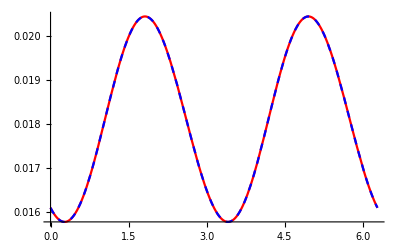

```mathematica
Plot[{J2[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}],J2HZ[{Cos[ϕ],Sin[ϕ]},{0.0,0.0},{0.9237949693169148,0.9933558220768413},{0.8906088551297885,0.5034137135325174},{1.0671192399522245,0.2037332952522504},{0.1152369628812383,0.9584092012785702}]},{ϕ,0,2π},PlotStyle->{{Red},{Blue,Dashed}}]
```

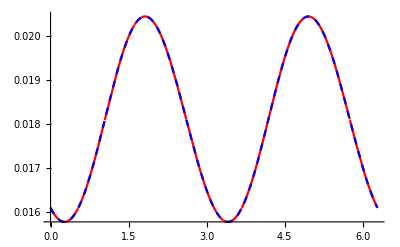
```mathematica
0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000-Graphics-
```

## Dipole Cross Section

```mathematica
dσ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
amp=J[{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4},{kT Cos[ϕ],kT Sin[ϕ]}];
amp.Conjugate[amp]
]
```

```mathematica
dσHZ[{x1_,y1_},{x2_,y2_},{x3_,y3_},{x4_,y4_},{kT_,ϕ_}]:=Module[{amp},
J2HZ[{kT Cos[ϕ],kT Sin[ϕ]},{0,0},{x1,y1},{x2,y2},{x3,y3},{x4,y4}]
]
```

```mathematica
showdσ[bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,v2},
x2u=-x1u;x4u=-x3u;
Print[Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"]];
Print[""];
Print[Plot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]];
Print[ParametricPlot[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16},PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"]];
v2=NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
Print["v_2=",v2];
v2
]
```

```mathematica
showdσHZ[bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[2(ϕ)],Sin[2(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3},
x2u=-x1u;x4u=-x3u;
If[showQ,
p1=Show[Graphics[{Orange,Opacity[0.3],Disk[{0,0},0.6]}],Graphics[{Orange,Opacity[0.3],Disk[bu,0.6]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{x3u,x4u}]}],Graphics[{PointSize[0.05],Blue,Point[x3u]}],Graphics[{PointSize[0.05],Red,Point[x4u]}],Graphics[{Dashing[0.025],RGBColor[0,0.5,0],Thickness[0.01],Line[{bu+x1u,bu+x2u}]}],Graphics[{PointSize[0.05],Blue,Point[bu+x1u]}],Graphics[{PointSize[0.05],Red,Point[bu+x2u]}],Axes->True,LabelStyle->{Black,16},PlotLabel->"Dipole Orientation"];
p2=Plot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
p3=ParametricPlot[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}]{Cos[ϕ],Sin[ϕ]},{ϕ,0,2π},PlotStyle->Red,AxesLabel->{x,y},LabelStyle->{Black,16}(*,PlotLabel->"dσ/d^2{Cos[ϕ],Sin[ϕ]}"*)];
Print[GraphicsRow[{p1,p3,p2},ImageSize->1000]];
];
NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}]/NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}]
]
```

```mathematica
ParallelEvaluate[
ClearAll[showdσHZ];
showdσHZ[n_,bu_,x1u_,x3u_,kT_,showQ_:True]:=Module[{ϕ,x2u,x4u,p1,p2,p3,num,den},
x2u=-x1u;x4u=-x3u;
num=NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}];
den=NIntegrate[dσHZ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
num/den
]
];
```

## b=2 r_dp

```mathematica
Getv2kT[b_,θA_:π/2,θB_:π/2]:=Module[{v2kTb05,i,kT,x1u,x3u,bu,ti},
ti=AbsoluteTime[];
x1u=1/2{Cos[θA],Sin[θA]};
x3u=1/2{Cos[θB],Sin[θB]};
bu={b,0};
v2kTb05=ParallelTable[{kT,showdσHZ[2,bu,x1u,x3u,kT,False]},{kT,0.1,10,0.1}];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
Print["Computatino time: ", AbsoluteTime[]-ti];
Print["b=",b, ", θA=",θA,", θB=",θB];
v2kTb05
]
```

## b=1.5 r_dp

```mathematica
LaunchKernels[20];
$KernelCount
```

20

```mathematica
ParallelEvaluate[
ClearAll[showdσ];
showdσ[n_,bu_,x1u_,x3u_,kT_]:=Module[{ϕ,x2u,x4u,p1,p2,p3,num,den},
x2u=-x1u;x4u=-x3u;
num=NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}] {Cos[n(ϕ)],Sin[n(ϕ)]},{ϕ,0,2π}];
den=NIntegrate[dσ[x1u+bu/2,x2u+bu/2,x3u-bu/2,x4u-bu/2,{kT,ϕ}],{ϕ,0,2π}];
num/den
]
];
```

```mathematica
Getv2kT[b_,rA_,θA_,rB_,θB_]:=Module[{v2kTb05,i,kT,x1u,x3u,bu,ti},
ti=AbsoluteTime[];
x1u=rA/2{Cos[θA],Sin[θA]};
x3u=rB/2{Cos[θB],Sin[θB]};
bu={b,0};
v2kTb05=ParallelTable[{kT,showdσ[2,bu,x1u,x3u,kT]},{kT,0.25,30,0.25}];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,1]]]}]},PlotStyle->{Red,Blue}]];
Print["Computatino time: ", AbsoluteTime[]-ti];
Print["b=",b, ", r_A=",rA, ", θ_A=",θA, ", r_B=",rB,", θ_B=",θB];
v2kTb05
]
```

```mathematica
rdp=1.5;Getv2kT[1.0,rdp,π/2,rdp,π/2]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1913262 near {ϕ$1913262} = {5.63268}. NIntegrate obtained -1.17751×10^-6+0. ⅈ and 1.97695×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1787974 near {ϕ$1787974} = {0.539864}. NIntegrate obtained -1.63647×10^-18+0. ⅈ and 1.04375×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1928472 near {ϕ$1928472} = {0.601223}. NIntegrate obtained -4.82003×10^-15+0. ⅈ and 5.77047×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2078872 near {ϕ$2078872} = {2.57699}. NIntegrate obtained -4.02479×10^-14+0. ⅈ and 3.7712×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1664107 near {ϕ$1664107} = {2.42973}. NIntegrate obtained 4.96022×10^-18+0. ⅈ and 4.74623×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1708192 near {ϕ$1708192} = {2.14748}. NIntegrate obtained -1.78677×10^-16+0. ⅈ and 2.24405×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1758359 near {ϕ$1758359} = {0.723941}. NIntegrate obtained -1.73465×10^-16+0. ⅈ and 1.57928×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2160738 near {ϕ$2160738} = {0.0000241858}. NIntegrate obtained -5.47522×10^-18+0. ⅈ and 4.96196×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1765086 near {ϕ$1765086} = {1.20254}. NIntegrate obtained 1.6263×10^-19+0. ⅈ and 1.64709×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2052774 near {ϕ$2052774} = {0.601223}. NIntegrate obtained 8.64651×10^-18+0. ⅈ and 5.72034×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1868649 near {ϕ$1868649} = {0.748485}. NIntegrate obtained -2.82735×10^-17+0. ⅈ and 3.30279×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2015289 near {ϕ$2015289} = {0.613495}. NIntegrate obtained 1.78276×10^-13+0. ⅈ and 7.51789×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1815404 near {ϕ$1815404} = {0.527592}. NIntegrate obtained 2.49666×10^-13+0. ⅈ and 7.29207×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1807870 near {ϕ$1807870} = {2.41746}. NIntegrate obtained -3.48124×10^-17+0. ⅈ and 7.50585×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1532437 near {ϕ$1532437} = {0.601223}. NIntegrate obtained 1.00255×10^-17+0. ⅈ and 1.17262×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1768170 near {ϕ$1768170} = {2.442}. NIntegrate obtained 2.40769×10^-17+0. ⅈ and 1.90308×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2070994 near {ϕ$2070994} = {0.539864}. NIntegrate obtained 9.51552×10^-14+0. ⅈ and 1.45942×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1723430 near {ϕ$1723430} = {2.63835}. NIntegrate obtained -6.57088×10^-16+0. ⅈ and 8.4716×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1884206 near {ϕ$1884206} = {2.60153}. NIntegrate obtained -2.81163×10^-16+0. ⅈ and 4.74747×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1791556 near {ϕ$1791556} = {0.478504}. NIntegrate obtained -6.02368×10^-15+0. ⅈ and 2.5355×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1913262 near {ϕ$1913262} = {2.49109}. NIntegrate obtained 7.35636×10^-12+0. ⅈ and 1.99625×10^-12 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (6.875 Cos[ϕ$2015289]-10.3125 Sin[ϕ$2015289])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+13.75 ⅈ) Cos[«1»]-(0.+20.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (6.875 Cos[ϕ$2015289]-10.3125 Sin[ϕ$2015289])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+13.75 ⅈ) Cos[«1»]-(0.+20.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (6.875 Cos[ϕ$2015289]+10.3125 Sin[ϕ$2015289])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (6.875 Cos[ϕ$2015289]+10.3125 Sin[ϕ$2015289])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (13.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-13.75 Cos[ϕ$2015289])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-13.75 Cos[ϕ$2015289])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+13.75 Cos[«1»])]))/Abs[0.+13.75 Sin[ϕ$2015289]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (13.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-13.75 Cos[ϕ$2015289])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-13.75 Cos[ϕ$2015289])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+13.75 Cos[«1»])]))/Abs[0.+13.75 Sin[ϕ$2015289]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (6.5 Cos[ϕ$2070994]-9.75 Sin[ϕ$2070994])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (6.5 Cos[ϕ$2070994]-9.75 Sin[ϕ$2070994])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (6.5 Cos[ϕ$2070994]+9.75 Sin[ϕ$2070994])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (6.5 Cos[ϕ$2070994]+9.75 Sin[ϕ$2070994])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (13. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-13. Cos[ϕ$2070994])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-13. Cos[ϕ$2070994])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+13. Cos[«1»])]))/Abs[0.+13. Sin[ϕ$2070994]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (13. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-13. Cos[ϕ$2070994])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-13. Cos[ϕ$2070994])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+13. Cos[«1»])]))/Abs[0.+13. Sin[ϕ$2070994]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (7.25 Cos[ϕ$1913262]-10.875 Sin[ϕ$1913262])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (7.25 Cos[ϕ$1913262]-10.875 Sin[ϕ$1913262])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (7.25 Cos[ϕ$1913262]+10.875 Sin[ϕ$1913262])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (7.25 Cos[ϕ$1913262]+10.875 Sin[ϕ$1913262])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (14.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-14.5 Cos[ϕ$1913262])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-14.5 Cos[ϕ$1913262])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+14.5 Cos[«1»])]))/Abs[0.+14.5 Sin[ϕ$1913262]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (14.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-14.5 Cos[ϕ$1913262])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-14.5 Cos[ϕ$1913262])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+14.5 Cos[«1»])]))/Abs[0.+14.5 Sin[ϕ$1913262]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1894027 near {ϕ$1894027} = {0.0000241858}. NIntegrate obtained -2.62919×10^-18+0. ⅈ and 2.1928×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1798042 near {ϕ$1798042} = {0.0000241858}. NIntegrate obtained -6.60279×10^-17+0. ⅈ and 1.65764×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1867458 near {ϕ$1867458} = {0.687126}. NIntegrate obtained 2.57498×10^-18+0. ⅈ and 1.18957×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2045186 near {ϕ$2045186} = {2.55245}. NIntegrate obtained -1.43273×10^-14+0. ⅈ and 1.00987×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1744226 near {ϕ$1744226} = {0.0000241858}. NIntegrate obtained 5.96311×10^-18+0. ⅈ and 5.49548×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2201398 near {ϕ$2201398} = {2.57699}. NIntegrate obtained -1.82182×10^-13+0. ⅈ and 4.83193×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2257742 near {ϕ$2257742} = {0.0000241858}. NIntegrate obtained 3.55923×10^-18+0. ⅈ and 5.18471×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1963419 near {ϕ$1963419} = {0.674854}. NIntegrate obtained -4.86133×10^-17+0. ⅈ and 4.13169×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1861895 near {ϕ$1861895} = {2.50336}. NIntegrate obtained 4.60157×10^-17+0. ⅈ and 2.83876×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2148989 near {ϕ$2148989} = {2.62608}. NIntegrate obtained -1.41954×10^-17+0. ⅈ and 6.73392×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1997182 near {ϕ$1997182} = {2.47882}. NIntegrate obtained -1.45806×10^-15+0. ⅈ and 5.29679×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1904247 near {ϕ$1904247} = {2.40518}. NIntegrate obtained -1.08284×10^-16+0. ⅈ and 8.80024×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2055820 near {ϕ$2055820} = {0.613495}. NIntegrate obtained -5.28078×10^-7+0. ⅈ and 2.01241×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1875552 near {ϕ$1875552} = {2.34382}. NIntegrate obtained -1.42522×10^-17+0. ⅈ and 1.91069×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1848470 near {ϕ$1848470} = {2.69971}. NIntegrate obtained -1.68322×10^-15+0. ⅈ and 1.164×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1628413 near {ϕ$1628413} = {0.404873}. NIntegrate obtained -4.13242×10^-17+0. ⅈ and 1.00417×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1925342 near {ϕ$1925342} = {0.723941}. NIntegrate obtained -5.05882×10^-13+0. ⅈ and 1.21318×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2128409 near {ϕ$2128409} = {2.51563}. NIntegrate obtained -1.83137×10^-12+0. ⅈ and 7.44811×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2188943 near {ϕ$2188943} = {0.662582}. NIntegrate obtained 4.57956×10^-13+0. ⅈ and 2.49991×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1911077 near {ϕ$1911077} = {0.883475}. NIntegrate obtained -2.80248×10^-15+0. ⅈ and 3.31006×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2003976 near {ϕ$2003976} = {0.0000241858}. NIntegrate obtained 4.65445×10^-19+0. ⅈ and 3.22681×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1968019 near {ϕ$1968019} = {0.920291}. NIntegrate obtained 1.89735×10^-19+0. ⅈ and 8.92273×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1874966 near {ϕ$1874966} = {0.944835}. NIntegrate obtained 2.42861×10^-17+0. ⅈ and 1.04491×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1837711 near {ϕ$1837711} = {2.40518}. NIntegrate obtained 3.80826×10^-18+0. ⅈ and 1.73616×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2352043 near {ϕ$2352043} = {0.0000241858}. NIntegrate obtained 4.81284×10^-18+0. ⅈ and 5.62636×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2322553 near {ϕ$2322553} = {2.57699}. NIntegrate obtained 7.00084×10^-15+0. ⅈ and 5.90522×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2154341 near {ϕ$2154341} = {0.552135}. NIntegrate obtained -6.65737×10^-14+0. ⅈ and 2.25319×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2058155 near {ϕ$2058155} = {2.45427}. NIntegrate obtained -7.74209×10^-17+0. ⅈ and 7.59569×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1969678 near {ϕ$1969678} = {0.699398}. NIntegrate obtained -9.57812×10^-16+0. ⅈ and 3.5459×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2097727 near {ϕ$2097727} = {0.503048}. NIntegrate obtained -2.43221×10^-16+0. ⅈ and 5.61873×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1994751 near {ϕ$1994751} = {0.625767}. NIntegrate obtained 3.62022×10^-18+0. ⅈ and 1.44439×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1963479 near {ϕ$1963479} = {2.42973}. NIntegrate obtained 5.13817×10^-15+0. ⅈ and 1.5916×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1985348 near {ϕ$1985348} = {2.45427}. NIntegrate obtained 4.82809×10^-19+0. ⅈ and 2.9476×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2249888 near {ϕ$2249888} = {0.453961}. NIntegrate obtained 4.48885×10^-18+0. ⅈ and 6.68451×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2044740 near {ϕ$2044740} = {0.564407}. NIntegrate obtained 1.50449×10^-13+0. ⅈ and 9.69287×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1731689 near {ϕ$1731689} = {2.73652}. NIntegrate obtained 1.28357×10^-17+0. ⅈ and 1.29196×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2097162 near {ϕ$2097162} = {0.564407}. NIntegrate obtained 5.16738×10^-7+0. ⅈ and 4.93229×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2244629 near {ϕ$2244629} = {2.36837}. NIntegrate obtained 1.71943×10^-12+0. ⅈ and 1.26047×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2035932 near {ϕ$2035932} = {0.503048}. NIntegrate obtained 1.12626×10^-14+0. ⅈ and 6.97369×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (6.375 Cos[ϕ$2044740]-9.5625 Sin[ϕ$2044740])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (6.375 Cos[ϕ$2044740]-9.5625 Sin[ϕ$2044740])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (6.375 Cos[ϕ$2044740]+9.5625 Sin[ϕ$2044740])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (6.375 Cos[ϕ$2044740]+9.5625 Sin[ϕ$2044740])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (12.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-12.75 Cos[ϕ$2044740])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-12.75 Cos[ϕ$2044740])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+12.75 Cos[«1»])]))/Abs[0.+12.75 Sin[ϕ$2044740]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (12.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-12.75 Cos[ϕ$2044740])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-12.75 Cos[ϕ$2044740])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+12.75 Cos[«1»])]))/Abs[0.+12.75 Sin[ϕ$2044740]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2301338 near {ϕ$2301338} = {0.674854}. NIntegrate obtained 1.2368×10^-13+0. ⅈ and 3.2727×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1927705 near {ϕ$1927705} = {2.82243}. NIntegrate obtained -6.66303×10^-8+0. ⅈ and 1.93142×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2066457 near {ϕ$2066457} = {5.71858}. NIntegrate obtained 1.06257×10^-6+0. ⅈ and 1.77317×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2433700 near {ϕ$2433700} = {5.82903}. NIntegrate obtained -2.37003×10^-7+0. ⅈ and 1.75435×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2287577 near {ϕ$2287577} = {0.503048}. NIntegrate obtained -9.51326×10^-8+0. ⅈ and 2.43044×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2078765 near {ϕ$2078765} = {2.68744}. NIntegrate obtained -4.18395×10^-7+0. ⅈ and 1.03311×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1971671 near {ϕ$1971671} = {2.82243}. NIntegrate obtained 5.68303×10^-7+0. ⅈ and 4.313×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2217816 near {ϕ$2217816} = {3.71827}. NIntegrate obtained 2.82775×10^-6+0. ⅈ and 2.26961×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2146944 near {ϕ$2146944} = {2.58926}. NIntegrate obtained -3.27087×10^-7+0. ⅈ and 4.18939×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2097162 near {ϕ$2097162} = {0.564407}. NIntegrate obtained -2.90051×10^-12+0. ⅈ and 5.91621×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2455253 near {ϕ$2455253} = {5.74313}. NIntegrate obtained -2.69552×10^-7+0. ⅈ and 6.06768×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2364209 near {ϕ$2364209} = {0.588951}. NIntegrate obtained 0.00773795+0. ⅈ and 0.000271316 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2089021 near {ϕ$2089021} = {2.60153}. NIntegrate obtained 0.000624877+0. ⅈ and 0.0000268639 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2096174 near {ϕ$2096174} = {2.67516}. NIntegrate obtained 0.0971207+0. ⅈ and 0.00777475 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2076734 near {ϕ$2076734} = {5.70631}. NIntegrate obtained 0.000041338+0. ⅈ and 4.39414×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1927705 near {ϕ$1927705} = {0.552135}. NIntegrate obtained -2.23527×10^-10+0. ⅈ and 1.39837×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2066457 near {ϕ$2066457} = {0.613495}. NIntegrate obtained -3.30566×10^-11+0. ⅈ and 1.70044×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1844619 near {ϕ$1844619} = {0.51532}. NIntegrate obtained 0.853706+0. ⅈ and 0.108798 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2433700 near {ϕ$2433700} = {3.60783}. NIntegrate obtained -2.31864×10^-9+0. ⅈ and 1.76904×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2287577 near {ϕ$2287577} = {3.77963}. NIntegrate obtained 3.25464×10^-8+0. ⅈ and 6.56448×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2078765 near {ϕ$2078765} = {0.699398}. NIntegrate obtained -5.16326×10^-9+0. ⅈ and 1.74623×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2154794 near {ϕ$2154794} = {5.77994}. NIntegrate obtained 14.1179+0. ⅈ and 1.5623 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2217816 near {ϕ$2217816} = {3.80417}. NIntegrate obtained -7.15517×10^-8+0. ⅈ and 4.31563×10^-7 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (7.625 Cos[ϕ$2097162]-11.4375 Sin[ϕ$2097162])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+15.25 ⅈ) Cos[«1»]-(0.+22.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (7.625 Cos[ϕ$2097162]-11.4375 Sin[ϕ$2097162])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+15.25 ⅈ) Cos[«1»]-(0.+22.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (7.625 Cos[ϕ$2097162]+11.4375 Sin[ϕ$2097162])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (7.625 Cos[ϕ$2097162]+11.4375 Sin[ϕ$2097162])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (15.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-15.25 Cos[ϕ$2097162])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-15.25 Cos[ϕ$2097162])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+15.25 Cos[«1»])]))/Abs[0.+15.25 Sin[ϕ$2097162]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (15.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-15.25 Cos[ϕ$2097162])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-15.25 Cos[ϕ$2097162])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+15.25 Cos[«1»])]))/Abs[0.+15.25 Sin[ϕ$2097162]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2146944 near {ϕ$2146944} = {5.63268}. NIntegrate obtained -6.14732×10^-10+0. ⅈ and 4.04639×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1971671 near {ϕ$1971671} = {2.29474}. NIntegrate obtained 4.68793×10^-11+0. ⅈ and 5.67366×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2138649 near {ϕ$2138649} = {2.60153}. NIntegrate obtained 147.995+0. ⅈ and 10.2382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2364209 near {ϕ$2364209} = {0.588951}. NIntegrate obtained -0.00265189+0. ⅈ and 0.000556784 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2455253 near {ϕ$2455253} = {0.539864}. NIntegrate obtained -1.79684×10^-9+0. ⅈ and 5.80442×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2076734 near {ϕ$2076734} = {0.65031}. NIntegrate obtained -7.05428×10^-6+0. ⅈ and 6.41901×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::levmaxord: ⅇ^(-ⅈ (8.75 Cos[ϕ$1927705]-13.125 Sin[ϕ$1927705])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (8.75 Cos[ϕ$1927705]-13.125 Sin[ϕ$1927705])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (8.75 Cos[ϕ$1927705]+13.125 Sin[ϕ$1927705])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (8.75 Cos[ϕ$1927705]+13.125 Sin[ϕ$1927705])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (8. Cos[ϕ$2066457]-12. Sin[ϕ$2066457])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (8. Cos[ϕ$2066457]-12. Sin[ϕ$2066457])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: (17.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$1927705])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$1927705])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+17.5 Cos[«1»])]))/Abs[0.+17.5 Sin[ϕ$1927705]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (17.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$1927705])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-17.5 Cos[ϕ$1927705])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+17.5 Cos[«1»])]))/Abs[0.+17.5 Sin[ϕ$1927705]] as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (8. Cos[ϕ$2066457]+12. Sin[ϕ$2066457])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (8. Cos[ϕ$2066457]+12. Sin[ϕ$2066457])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2089021 near {ϕ$2089021} = {3.74282}. NIntegrate obtained -0.000363481+0. ⅈ and 0.0000453142 for the integral and error estimates.

NIntegrate::levmaxord: (16. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$2066457])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$2066457])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+16. Cos[«1»])]))/Abs[0.+16. Sin[ϕ$2066457]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$2066457])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16. Cos[ϕ$2066457])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+16. Cos[«1»])]))/Abs[0.+16. Sin[ϕ$2066457]] as a non-Levin function.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2355781 near {ϕ$2355781} = {5.69404}. NIntegrate obtained 2599.73+0. ⅈ and 179.002 for the integral and error estimates.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2096174 near {ϕ$2096174} = {3.71827}. NIntegrate obtained 0.0186218+0. ⅈ and 0.0124697 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (9.5 Cos[ϕ$2433700]-14.25 Sin[ϕ$2433700])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (9.5 Cos[ϕ$2433700]-14.25 Sin[ϕ$2433700])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (9.5 Cos[ϕ$2433700]+14.25 Sin[ϕ$2433700])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (9.5 Cos[ϕ$2433700]+14.25 Sin[ϕ$2433700])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (19. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-19. Cos[ϕ$2433700])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-19. Cos[ϕ$2433700])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+19. Cos[«1»])]))/Abs[0.+19. Sin[ϕ$2433700]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (19. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-19. Cos[ϕ$2433700])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-19. Cos[ϕ$2433700])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+19. Cos[«1»])]))/Abs[0.+19. Sin[ϕ$2433700]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.25 Cos[ϕ$2078765]-15.375 Sin[ϕ$2078765])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.25 Cos[ϕ$2078765]-15.375 Sin[ϕ$2078765])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.25 Cos[ϕ$2078765]+15.375 Sin[ϕ$2078765])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.25 Cos[ϕ$2078765]+15.375 Sin[ϕ$2078765])) («1») as a non-Levin function.

NIntegrate::levmaxord: (20.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-20.5 Cos[ϕ$2078765])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-20.5 Cos[ϕ$2078765])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+20.5 Cos[«1»])]))/Abs[0.+20.5 Sin[ϕ$2078765]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (20.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-20.5 Cos[ϕ$2078765])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-20.5 Cos[ϕ$2078765])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+20.5 Cos[«1»])]))/Abs[0.+20.5 Sin[ϕ$2078765]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11. Cos[ϕ$2217816]-16.5 Sin[ϕ$2217816])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11. Cos[ϕ$2217816]-16.5 Sin[ϕ$2217816])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.625 Cos[ϕ$2287577]-15.9375 Sin[ϕ$2287577])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+21.25 ⅈ) Cos[«1»]-(0.+31.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.625 Cos[ϕ$2287577]-15.9375 Sin[ϕ$2287577])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+21.25 ⅈ) Cos[«1»]-(0.+31.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11. Cos[ϕ$2217816]+16.5 Sin[ϕ$2217816])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11. Cos[ϕ$2217816]+16.5 Sin[ϕ$2217816])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.625 Cos[ϕ$2287577]+15.9375 Sin[ϕ$2287577])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+21.25 ⅈ) Cos[«1»]+(0.+31.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.625 Cos[ϕ$2287577]+15.9375 Sin[ϕ$2287577])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+21.25 ⅈ) Cos[«1»]+(0.+31.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: (22. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2217816])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2217816])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22. Cos[«1»])]))/Abs[0.+22. Sin[ϕ$2217816]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (22. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2217816])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2217816])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22. Cos[«1»])]))/Abs[0.+22. Sin[ϕ$2217816]] as a non-Levin function.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::levmaxord: (21.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$2287577])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$2287577])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+21.25 Cos[«1»])]))/Abs[0.+21.25 Sin[ϕ$2287577]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (21.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$2287577])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$2287577])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+21.25 Cos[«1»])]))/Abs[0.+21.25 Sin[ϕ$2287577]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2422724 near {ϕ$2422724} = {5.76767}. NIntegrate obtained 31401.3+0. ⅈ and 2910.55 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1844619 near {ϕ$1844619} = {0.687126}. NIntegrate obtained 0.112144+0. ⅈ and 0.21832 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2097162 near {ϕ$2097162} = {0.582864}. NIntegrate obtained 8.29234×10^-6+0. ⅈ and 1.14958×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2154794 near {ϕ$2154794} = {0.687126}. NIntegrate obtained -0.314151+0. ⅈ and 2.30933 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::levmaxord: ⅇ^(-ⅈ (9.875 Cos[ϕ$2146944]-14.8125 Sin[ϕ$2146944])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+19.75 ⅈ) Cos[«1»]-(0.+29.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (9.875 Cos[ϕ$2146944]-14.8125 Sin[ϕ$2146944])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+19.75 ⅈ) Cos[«1»]-(0.+29.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (9.875 Cos[ϕ$2146944]+14.8125 Sin[ϕ$2146944])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (9.875 Cos[ϕ$2146944]+14.8125 Sin[ϕ$2146944])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (8.375 Cos[ϕ$1971671]-12.5625 Sin[ϕ$1971671])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+16.75 ⅈ) Cos[«1»]-(0.+25.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (8.375 Cos[ϕ$1971671]-12.5625 Sin[ϕ$1971671])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+16.75 ⅈ) Cos[«1»]-(0.+25.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: (19.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-19.75 Cos[ϕ$2146944])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-19.75 Cos[ϕ$2146944])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+19.75 Cos[«1»])]))/Abs[0.+19.75 Sin[ϕ$2146944]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (19.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-19.75 Cos[ϕ$2146944])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-19.75 Cos[ϕ$2146944])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+19.75 Cos[«1»])]))/Abs[0.+19.75 Sin[ϕ$2146944]] as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (8.375 Cos[ϕ$1971671]+12.5625 Sin[ϕ$1971671])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (8.375 Cos[ϕ$1971671]+12.5625 Sin[ϕ$1971671])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2370507 near {ϕ$2370507} = {0.552135}. NIntegrate obtained 446322.+0. ⅈ and 13707.9 for the integral and error estimates.

NIntegrate::levmaxord: (16.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$1971671])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$1971671])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+16.75 Cos[«1»])]))/Abs[0.+16.75 Sin[ϕ$1971671]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (16.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$1971671])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-16.75 Cos[ϕ$1971671])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+16.75 Cos[«1»])]))/Abs[0.+16.75 Sin[ϕ$1971671]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.125 Cos[ϕ$2364209]-18.1875 Sin[ϕ$2364209])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+24.25 ⅈ) Cos[«1»]-(0.+36.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.125 Cos[ϕ$2364209]-18.1875 Sin[ϕ$2364209])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+24.25 ⅈ) Cos[«1»]-(0.+36.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.125 Cos[ϕ$2364209]+18.1875 Sin[ϕ$2364209])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+24.25 ⅈ) Cos[«1»]+(0.+36.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.125 Cos[ϕ$2364209]+18.1875 Sin[ϕ$2364209])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+24.25 ⅈ) Cos[«1»]+(0.+36.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: (24.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2364209])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2364209])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+24.25 Cos[«1»])]))/Abs[0.+24.25 Sin[ϕ$2364209]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (24.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2364209])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2364209])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+24.25 Cos[«1»])]))/Abs[0.+24.25 Sin[ϕ$2364209]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.375 Cos[ϕ$2076734]-17.0625 Sin[ϕ$2076734])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+22.75 ⅈ) Cos[«1»]-(0.+34.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.375 Cos[ϕ$2076734]-17.0625 Sin[ϕ$2076734])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+22.75 ⅈ) Cos[«1»]-(0.+34.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.375 Cos[ϕ$2076734]+17.0625 Sin[ϕ$2076734])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+22.75 ⅈ) Cos[«1»]+(0.+34.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.375 Cos[ϕ$2076734]+17.0625 Sin[ϕ$2076734])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+22.75 ⅈ) Cos[«1»]+(0.+34.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: (22.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2076734])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2076734])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22.75 Cos[«1»])]))/Abs[0.+22.75 Sin[ϕ$2076734]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (22.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2076734])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2076734])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22.75 Cos[«1»])]))/Abs[0.+22.75 Sin[ϕ$2076734]] as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (9.125 Cos[ϕ$2455253]-13.6875 Sin[ϕ$2455253])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+18.25 ⅈ) Cos[«1»]-(0.+27.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (9.125 Cos[ϕ$2455253]-13.6875 Sin[ϕ$2455253])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+18.25 ⅈ) Cos[«1»]-(0.+27.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (9.125 Cos[ϕ$2455253]+13.6875 Sin[ϕ$2455253])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (9.125 Cos[ϕ$2455253]+13.6875 Sin[ϕ$2455253])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (18.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-18.25 Cos[ϕ$2455253])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18.25 Cos[ϕ$2455253])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+18.25 Cos[«1»])]))/Abs[0.+18.25 Sin[ϕ$2455253]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (18.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-18.25 Cos[ϕ$2455253])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-18.25 Cos[ϕ$2455253])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+18.25 Cos[«1»])]))/Abs[0.+18.25 Sin[ϕ$2455253]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.75 Cos[ϕ$2089021]-17.625 Sin[ϕ$2089021])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.75 Cos[ϕ$2089021]-17.625 Sin[ϕ$2089021])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.75 Cos[ϕ$2089021]+17.625 Sin[ϕ$2089021])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.75 Cos[ϕ$2089021]+17.625 Sin[ϕ$2089021])) («1») as a non-Levin function.

NIntegrate::levmaxord: (23.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$2089021])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$2089021])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+23.5 Cos[«1»])]))/Abs[0.+23.5 Sin[ϕ$2089021]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (23.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$2089021])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$2089021])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+23.5 Cos[«1»])]))/Abs[0.+23.5 Sin[ϕ$2089021]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.5 Cos[ϕ$2096174]-18.75 Sin[ϕ$2096174])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25. ⅈ) Cos[«1»]-(0.+37.5 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.5 Cos[ϕ$2096174]-18.75 Sin[ϕ$2096174])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25. ⅈ) Cos[«1»]-(0.+37.5 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.5 Cos[ϕ$2096174]+18.75 Sin[ϕ$2096174])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«18» («1»)+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25. ⅈ) Cos[«1»]+(0.+37.5 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.5 Cos[ϕ$2096174]+18.75 Sin[ϕ$2096174])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«18» («1»)+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25. ⅈ) Cos[«1»]+(0.+37.5 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: (25. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2096174])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2096174])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25. Cos[«1»])]))/Abs[0.+25. Sin[ϕ$2096174]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (25. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2096174])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2096174])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25. Cos[«1»])]))/Abs[0.+25. Sin[ϕ$2096174]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2138649 near {ϕ$2138649} = {0.748485}. NIntegrate obtained 21.1489+0. ⅈ and 14.4443 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2066457 near {ϕ$2066457} = {3.75514}. NIntegrate obtained 7.15945×10^-6+0. ⅈ and 3.02684×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2217816 near {ϕ$2217816} = {2.62308}. NIntegrate obtained 0.000010979-7.27596×10^-12 ⅈ and 1.10769×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2355781 near {ϕ$2355781} = {0.576679}. NIntegrate obtained 1038.38+0. ⅈ and 269.209 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2287577 near {ϕ$2287577} = {3.75823}. NIntegrate obtained 3.57338×10^-6+2.50111×10^-12 ⅈ and 1.07141×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1927705 near {ϕ$1927705} = {3.92694}. NIntegrate obtained 6.15223×10^-6+0. ⅈ and 3.72435×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2433700 near {ϕ$2433700} = {5.71866}. NIntegrate obtained 2.63532×10^-6+0. ⅈ and 3.62073×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.875 Cos[ϕ$1844619]-19.3125 Sin[ϕ$1844619])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25.75 ⅈ) Cos[«1»]-(0.+38.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.875 Cos[ϕ$1844619]-19.3125 Sin[ϕ$1844619])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25.75 ⅈ) Cos[«1»]-(0.+38.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.875 Cos[ϕ$1844619]+19.3125 Sin[ϕ$1844619])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25.75 ⅈ) Cos[«1»]+(0.+38.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.875 Cos[ϕ$1844619]+19.3125 Sin[ϕ$1844619])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25.75 ⅈ) Cos[«1»]+(0.+38.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: (25.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$1844619])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$1844619])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25.75 Cos[«1»])]))/Abs[0.+25.75 Sin[ϕ$1844619]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (25.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$1844619])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$1844619])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25.75 Cos[«1»])]))/Abs[0.+25.75 Sin[ϕ$1844619]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2078765 near {ϕ$2078765} = {0.57982}. NIntegrate obtained 2.33226×10^-6+1.47793×10^-12 ⅈ and 2.60475×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.25 Cos[ϕ$2154794]-19.875 Sin[ϕ$2154794])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.25 Cos[ϕ$2154794]-19.875 Sin[ϕ$2154794])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.25 Cos[ϕ$2154794]+19.875 Sin[ϕ$2154794])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.25 Cos[ϕ$2154794]+19.875 Sin[ϕ$2154794])) («1») as a non-Levin function.

NIntegrate::levmaxord: (26.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$2154794])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$2154794])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+26.5 Cos[«1»])]))/Abs[0.+26.5 Sin[ϕ$2154794]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (26.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$2154794])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$2154794])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+26.5 Cos[«1»])]))/Abs[0.+26.5 Sin[ϕ$2154794]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2422724 near {ϕ$2422724} = {5.6695}. NIntegrate obtained -19143.5+0. ⅈ and 5782.11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2370507 near {ϕ$2370507} = {0.552135}. NIntegrate obtained -314974.+0. ⅈ and 33286.5 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.625 Cos[ϕ$2138649]-20.4375 Sin[ϕ$2138649])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+27.25 ⅈ) Cos[«1»]-(0.+40.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.625 Cos[ϕ$2138649]-20.4375 Sin[ϕ$2138649])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+27.25 ⅈ) Cos[«1»]-(0.+40.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.625 Cos[ϕ$2138649]+20.4375 Sin[ϕ$2138649])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+27.25 ⅈ) Cos[«1»]+(0.+40.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.625 Cos[ϕ$2138649]+20.4375 Sin[ϕ$2138649])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+27.25 ⅈ) Cos[«1»]+(0.+40.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::levmaxord: (27.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2138649])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2138649])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+27.25 Cos[«1»])]))/Abs[0.+27.25 Sin[ϕ$2138649]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (27.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2138649])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2138649])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+27.25 Cos[«1»])]))/Abs[0.+27.25 Sin[ϕ$2138649]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2076734 near {ϕ$2076734} = {2.54945}. NIntegrate obtained 0.000112735+0. ⅈ and 0.0000121923 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14. Cos[ϕ$2355781]-21. Sin[ϕ$2355781])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14. Cos[ϕ$2355781]-21. Sin[ϕ$2355781])) («1») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14. Cos[ϕ$2355781]+21. Sin[ϕ$2355781])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14. Cos[ϕ$2355781]+21. Sin[ϕ$2355781])) («1») as a non-Levin function.

NIntegrate::levmaxord: (28. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$2355781])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$2355781])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28. Cos[«1»])]))/Abs[0.+28. Sin[ϕ$2355781]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (28. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$2355781])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$2355781])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28. Cos[«1»])]))/Abs[0.+28. Sin[ϕ$2355781]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2364209 near {ϕ$2364209} = {3.69994}. NIntegrate obtained 0.0186161-3.63798×10^-11 ⅈ and 0.00164506 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1971671 near {ϕ$1971671} = {5.93952}. NIntegrate obtained 6.82057×10^-6+0. ⅈ and 1.09483×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2096174 near {ϕ$2096174} = {2.50957}. NIntegrate obtained 0.225944+5.82077×10^-11 ⅈ and 0.0240786 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2146944 near {ϕ$2146944} = {5.62969}. NIntegrate obtained 1.93181×10^-6+0. ⅈ and 8.36974×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2089021 near {ϕ$2089021} = {3.75516}. NIntegrate obtained 0.00148025-5.45697×10^-12 ⅈ and 0.000120135 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.375 Cos[ϕ$2422724]-21.5625 Sin[ϕ$2422724])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+28.75 ⅈ) Cos[«1»]-(0.+43.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.375 Cos[ϕ$2422724]-21.5625 Sin[ϕ$2422724])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+28.75 ⅈ) Cos[«1»]-(0.+43.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.375 Cos[ϕ$2422724]+21.5625 Sin[ϕ$2422724])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+28.75 ⅈ) Cos[«1»]+(0.+43.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.375 Cos[ϕ$2422724]+21.5625 Sin[ϕ$2422724])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+28.75 ⅈ) Cos[«1»]+(0.+43.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+Times[«2»]+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: (28.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$2422724])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$2422724])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28.75 Cos[«1»])]))/Abs[0.+28.75 Sin[ϕ$2422724]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (28.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$2422724])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$2422724])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28.75 Cos[«1»])]))/Abs[0.+28.75 Sin[ϕ$2422724]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.75 Cos[ϕ$2370507]-22.125 Sin[ϕ$2370507])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.75 Cos[ϕ$2370507]-22.125 Sin[ϕ$2370507])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.75 Cos[ϕ$2370507]+22.125 Sin[ϕ$2370507])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.75 Cos[ϕ$2370507]+22.125 Sin[ϕ$2370507])) («1») as a non-Levin function.

NIntegrate::levmaxord: (29.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$2370507])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$2370507])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+29.5 Cos[«1»])]))/Abs[0.+29.5 Sin[ϕ$2370507]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (29.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$2370507])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$2370507])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+29.5 Cos[«1»])]))/Abs[0.+29.5 Sin[ϕ$2370507]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2455253 near {ϕ$2455253} = {2.59547}. NIntegrate obtained 4.45191×10^-6+0. ⅈ and 1.14233×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2154794 near {ϕ$2154794} = {0.575231}. NIntegrate obtained 38.1974+0. ⅈ and 3.74976 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2355781 near {ϕ$2355781} = {0.607444}. NIntegrate obtained 6326.59+0. ⅈ and 525.399 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2370507 near {ϕ$2370507} = {0.552221}. NIntegrate obtained 1.19462×10^6+0. ⅈ and 119592. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1844619 near {ϕ$1844619} = {3.71682}. NIntegrate obtained 2.81189+0. ⅈ and 0.334032 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2138649 near {ϕ$2138649} = {3.71529}. NIntegrate obtained 481.088+0. ⅈ and 53.1391 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2422724 near {ϕ$2422724} = {2.53259}. NIntegrate obtained 82341.1+0. ⅈ and 8842.25 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-Graphics-

Computatino time: 188.64436

b=1., r_A=1.5, θ_A=π/2, r_B=1.5, θ_B=π/2

{{0.25,{-0.014228+0. ⅈ,-5.70111×10^-17+0. ⅈ}},{0.5,{-0.0580642+0. ⅈ,-1.05423×10^-16+0. ⅈ}},{0.75,{-0.131696+0. ⅈ,1.143×10^-16}},{1.,{-0.233549+0. ⅈ,5.57365×10^-17}},{1.25,{-0.359845+0. ⅈ,1.41013×10^-16}},{1.5,{-0.496985+0. ⅈ,1.68401×10^-16}},{1.75,{-0.60921+0. ⅈ,1.15543×10^-17}},{2.,{-0.655019+0. ⅈ,2.45456×10^-16}},{2.25,{-0.635753+0. ⅈ,2.08258×10^-17}},{2.5,{-0.588455+0. ⅈ,-1.90197×10^-16+0. ⅈ}},{2.75,{-0.540455+0. ⅈ,-3.16363×10^-16+0. ⅈ}},{3.,{-0.499933+0. ⅈ,5.87438×10^-17}},{3.25,{-0.466155+0. ⅈ,-7.46643×10^-16+0. ⅈ}},{3.5,{-0.436266+0. ⅈ,5.44026×10^-16}},{3.75,{-0.407478+0. ⅈ,8.57869×10^-16}},{4.,{-0.377392+0. ⅈ,1.87271×10^-15}},{4.25,{-0.343829+0. ⅈ,-3.89756×10^-15+0. ⅈ}},{4.5,{-0.304593+0. ⅈ,1.63247×10^-15}},{4.75,{-0.257322+0. ⅈ,5.05442×10^-15}},{5.,{-0.199673+0. ⅈ,-3.02677×10^-14+0. ⅈ}},{5.25,{-0.130578+0. ⅈ,1.42991×10^-14}},{5.5,{-0.0546257+0. ⅈ,4.23574×10^-14}},{5.75,{0.00657318,-4.00556×10^-14+0. ⅈ}},{6.,{0.000281032,2.06774×10^-15}},{6.25,{-0.126996+0. ⅈ,-1.61757×10^-13+0. ⅈ}},{6.5,{-0.33142+0. ⅈ,-3.1218×10^-13+0. ⅈ}},{6.75,{-0.502445+0. ⅈ,-4.93378×10^-13+0. ⅈ}},{7.,{-0.59715+0. ⅈ,-2.11769×10^-13+0. ⅈ}},{7.25,{-0.63193+0. ⅈ,-6.39251×10^-13+0. ⅈ}},{7.5,{-0.628973+0. ⅈ,2.15862×10^-14}},{7.75,{-0.600636+0. ⅈ,-1.09407×10^-12+0. ⅈ}},{8.,{-0.550928+0. ⅈ,3.21006×10^-13}},{8.25,{-0.478768+0. ⅈ,-7.68413×10^-12+0. ⅈ}},{8.5,{-0.380759+0. ⅈ,-2.6727×10^-12+0. ⅈ}},{8.75,{-0.254778+0. ⅈ,-1.66977×10^-11+0. ⅈ}},{9.,{-0.105632+0. ⅈ,-3.35185×10^-12+0. ⅈ}},{9.25,{0.0489743,-1.0667×10^-11+0. ⅈ}},{9.5,{0.179634,-3.09848×10^-11+0. ⅈ}},{9.75,{0.259564,1.02647×10^-10}},{10.,{0.281151,-1.25987×10^-10+0. ⅈ}},{10.25,{0.256617,-6.02135×10^-11+0. ⅈ}},{10.5,{0.205262,2.48377×10^-10}},{10.75,{0.142757,-1.10589×10^-10+0. ⅈ}},{11.,{0.0781437,-3.49889×10^-10+0. ⅈ}},{11.25,{0.0151721,-1.77911×10^-9+0. ⅈ}},{11.5,{-0.0455792+0. ⅈ,-1.21163×10^-9+0. ⅈ}},{11.75,{-0.105031+0. ⅈ,-6.34794×10^-9+0. ⅈ}},{12.,{-0.164317+0. ⅈ,2.88592×10^-10}},{12.25,{-0.22346+0. ⅈ,1.23319×10^-8}},{12.5,{-0.279843+0. ⅈ,-2.99228×10^-8+0. ⅈ}},{12.75,{-0.327116+0. ⅈ,1.04794×10^-8}},{13.,{-0.356404+0. ⅈ,7.56113×10^-9}},{13.25,{-0.360746+0. ⅈ,3.9904×10^-8}},{13.5,{-0.339557+0. ⅈ,1.13939×10^-8}},{13.75,{-0.298375+0. ⅈ,1.69399×10^-8}},{14.,{-0.244651+0. ⅈ,-1.77689×10^-7+0. ⅈ}},{14.25,{-0.184262+0. ⅈ,1.70723×10^-7}},{14.5,{-0.120816+0. ⅈ,7.54781×10^-7}},{14.75,{-0.0566807+0. ⅈ,-3.94031×10^-7+0. ⅈ}},{15.,{0.00560948,-2.54887×10^-7+0. ⅈ}},{15.25,{0.062315,-3.49782×10^-7+0. ⅈ}},{15.5,{0.108308,2.48829×10^-6}},{15.75,{0.138174,-5.34898×10^-6+0. ⅈ}},{16.,{0.148415,-4.61721×10^-6+0. ⅈ}},{16.25,{0.139419,-8.81324×10^-6+0. ⅈ}},{16.5,{0.115559,2.20037×10^-7}},{16.75,{0.083322,6.87323×10^-6}},{17.,{0.0488614,-0.0000176331+0. ⅈ}},{17.25,{0.0166696,-5.59489×10^-7+0. ⅈ}},{17.5,{-0.0108303+0. ⅈ,-0.0000363327+0. ⅈ}},{17.75,{-0.032522+0. ⅈ,-0.000180758+0. ⅈ}},{18.,{-0.0487868+0. ⅈ,0.000207569}},{18.25,{-0.0605476+0. ⅈ,-0.000403611+0. ⅈ}},{18.5,{-0.0688713+0. ⅈ,0.000928264}},{18.75,{-0.0774331+0. ⅈ,0.00089149}},{19.,{-0.0899331+0. ⅈ,-0.000879832+0. ⅈ}},{19.25,{-0.111314+0. ⅈ,0.0025427}},{19.5,{-0.13624+0. ⅈ,0.0102143}},{19.75,{-0.169316+0. ⅈ,-0.000318215+0. ⅈ}},{20.,{-0.191555-4.39978×10^-8 ⅈ,-0.000912368-2.0956×10^-10 ⅈ}},{20.25,{-0.19864+0. ⅈ,-0.0111679+0. ⅈ}},{20.5,{-0.179395+1.13681×10^-7 ⅈ,-0.00221384+1.40289×10^-9 ⅈ}},{20.75,{-0.100216-5.82204×10^-8 ⅈ,0.00223063+1.29588×10^-9 ⅈ}},{21.,{-0.0185204-5.19052×10^-9 ⅈ,-0.0076678-2.14898×10^-9 ⅈ}},{21.25,{-0.0266226+1.86339×10^-8 ⅈ,0.00910801-6.37496×10^-9 ⅈ}},{21.5,{0.135847+1.16887×10^-7 ⅈ,0.00100658+8.66092×10^-10 ⅈ}},{21.75,{0.210159,-0.104374+0. ⅈ}},{22.,{0.25756+1.70689×10^-7 ⅈ,-0.00651713-4.31899×10^-9 ⅈ}},{22.25,{0.279208,-0.0633521+0. ⅈ}},{22.5,{0.309862-4.47436×10^-8 ⅈ,0.0459379-6.63336×10^-9 ⅈ}},{22.75,{0.366682,-0.0625738+0. ⅈ}},{23.,{0.345821,0.0110309}},{23.25,{0.360227,-0.174337+0. ⅈ}},{23.5,{0.422143,-0.245554+0. ⅈ}},{23.75,{0.317182,-0.124102+0. ⅈ}},{24.,{0.401006,-0.0634952+0. ⅈ}},{24.25,{0.415659,-0.142452+0. ⅈ}},{24.5,{0.330336,-0.063698+0. ⅈ}},{24.75,{0.423255,-0.145733+0. ⅈ}},{25.,{0.429845,0.0824177}},{25.25,{0.331976,0.157919}},{25.5,{0.363007,-0.0577307+0. ⅈ}},{25.75,{0.303606,0.039882}},{26.,{0.363503,0.0934999}},{26.25,{0.323256,0.023913}},{26.5,{0.369605,-0.00822441+0. ⅈ}},{26.75,{0.32839,-0.246962+0. ⅈ}},{27.,{0.253016,0.0677744}},{27.25,{0.307626,0.0439605}},{27.5,{0.31694,0.0327406}},{27.75,{0.199029,-0.184109+0. ⅈ}},{28.,{0.410921,0.164129}},{28.25,{0.279155,0.088896}},{28.5,{0.337494,-0.0564798+0. ⅈ}},{28.75,{0.381356,-0.23249+0. ⅈ}},{29.,{0.445887,-0.61811+0. ⅈ}},{29.25,{0.361182,-0.00815654+0. ⅈ}},{29.5,{0.37361,-0.26366+0. ⅈ}},{29.75,{0.374025,0.0618985}},{30.,{0.365712,0.168846}}}

```mathematica
rdp=1.0;Getv2kT[1.0,rdp,π/2,rdp,π/2]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$604270 near {ϕ$604270} = {0.0000241858}. NIntegrate obtained 1.27855×10^-16+0. ⅈ and 1.24687×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$661407 near {ϕ$661407} = {1.04301}. NIntegrate obtained -2.1684×10^-19+0. ⅈ and 1.05762×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$839058 near {ϕ$839058} = {2.50336}. NIntegrate obtained -6.25534×10^-19+0. ⅈ and 4.52167×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$601171 near {ϕ$601171} = {0.0000241858}. NIntegrate obtained 7.07442×10^-18+0. ⅈ and 7.34122×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$730761 near {ϕ$730761} = {1.81614}. NIntegrate obtained -1.06303×10^-19+0. ⅈ and 4.98511×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$616470 near {ϕ$616470} = {0.638038}. NIntegrate obtained 1.79717×10^-15+0. ⅈ and 1.37551×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$808979 near {ϕ$808979} = {1.00619}. NIntegrate obtained 1.43657×10^-18+0. ⅈ and 1.44778×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$660277 near {ϕ$660277} = {2.08612}. NIntegrate obtained -1.45283×10^-17+0. ⅈ and 8.98817×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$759823 near {ϕ$759823} = {0.613495}. NIntegrate obtained -4.47233×10^-19+0. ⅈ and 9.25797×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$782411 near {ϕ$782411} = {2.18429}. NIntegrate obtained -6.30193×10^-19+0. ⅈ and 6.1762×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$687746 near {ϕ$687746} = {0.993922}. NIntegrate obtained -9.14796×10^-19+0. ⅈ and 4.66665×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$651593 near {ϕ$651593} = {0.895747}. NIntegrate obtained -2.1242×10^-18+0. ⅈ and 7.76619×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$799213 near {ϕ$799213} = {2.30701}. NIntegrate obtained 9.97805×10^-19+0. ⅈ and 1.3323×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$675283 near {ϕ$675283} = {0.0000241858}. NIntegrate obtained -8.39198×10^-19+0. ⅈ and 6.81874×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$805269 near {ϕ$805269} = {0.0000241858}. NIntegrate obtained -1.40872×10^-18+0. ⅈ and 1.00126×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$904813 near {ϕ$904813} = {0.932563}. NIntegrate obtained -9.67566×10^-18+0. ⅈ and 3.21788×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$901669 near {ϕ$901669} = {0.625767}. NIntegrate obtained -3.59396×10^-18+0. ⅈ and 2.21484×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$888851 near {ϕ$888851} = {2.18429}. NIntegrate obtained -6.91179×10^-19+0. ⅈ and 1.73907×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$851768 near {ϕ$851768} = {0.748485}. NIntegrate obtained -4.97462×10^-18+0. ⅈ and 2.96926×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$829420 near {ϕ$829420} = {2.40518}. NIntegrate obtained 2.93836×10^-18+0. ⅈ and 2.05242×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$691547 near {ϕ$691547} = {0.0000241858}. NIntegrate obtained 1.27665×10^-17+0. ⅈ and 7.50358×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$939498 near {ϕ$939498} = {0.748485}. NIntegrate obtained 3.14419×10^-18+0. ⅈ and 4.15739×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$757573 near {ϕ$757573} = {2.24565}. NIntegrate obtained 7.2506×10^-19+0. ⅈ and 1.06845×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$712847 near {ϕ$712847} = {0.0000241858}. NIntegrate obtained -8.30092×10^-20+0. ⅈ and 5.84346×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$710929 near {ϕ$710929} = {0.503048}. NIntegrate obtained 1.38778×10^-17+0. ⅈ and 2.22938×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$769407 near {ϕ$769407} = {0.0000241858}. NIntegrate obtained 7.24383×10^-18+0. ⅈ and 1.81087×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$912163 near {ϕ$912163} = {2.58926}. NIntegrate obtained -7.28448×10^-20+0. ⅈ and 7.03033×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$851905 near {ϕ$851905} = {0.478504}. NIntegrate obtained 1.4569×10^-19+0. ⅈ and 1.01162×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$775707 near {ϕ$775707} = {0.0000241858}. NIntegrate obtained -1.58194×10^-18+0. ⅈ and 7.44116×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$773065 near {ϕ$773065} = {1.05528}. NIntegrate obtained 3.45589×10^-19+0. ⅈ and 4.57604×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$740043 near {ϕ$740043} = {1.178}. NIntegrate obtained -3.13741×10^-18+0. ⅈ and 6.01715×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$886288 near {ϕ$886288} = {2.442}. NIntegrate obtained 1.16213×10^-18+0. ⅈ and 1.2372×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1020449 near {ϕ$1020449} = {2.49109}. NIntegrate obtained 7.99536×10^-18+0. ⅈ and 3.27638×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$894865 near {ϕ$894865} = {3.9269908451597596520323736587854910598180402381274234357988461852}. NIntegrate obtained -7.31836×10^-19+0. ⅈ and 6.5723×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$959553 near {ϕ$959553} = {0.736213}. NIntegrate obtained 1.32095×10^-18+0. ⅈ and 2.7782×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$939417 near {ϕ$939417} = {2.22111}. NIntegrate obtained 3.95395×10^-18+0. ⅈ and 3.03461×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$819667 near {ϕ$819667} = {0.7853981635344437013310338254255653911892177086728761281619881629}. NIntegrate obtained 3.854×10^-19+0. ⅈ and 1.26275×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$875093 near {ϕ$875093} = {5.4977871436451427527094971061159238945621340229064077931298015756}. NIntegrate obtained 2.37169×10^-20+0. ⅈ and 1.60316×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$840847 near {ϕ$840847} = {1.23936}. NIntegrate obtained 1.69407×10^-20+0. ⅈ and 6.37756×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1030430 near {ϕ$1030430} = {1.01847}. NIntegrate obtained -1.21193×10^-17+0. ⅈ and 2.90872×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$799545 near {ϕ$799545} = {2.33155}. NIntegrate obtained -2.33103×10^-18+0. ⅈ and 1.90327×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$777243 near {ϕ$777243} = {5.4977871156096196959615167468470644249536882774975765642011538148}. NIntegrate obtained 3.84892×10^-18+0. ⅈ and 7.47576×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$856182 near {ϕ$856182} = {2.3561944620198265799636790097559873235696925597437711985548958182}. NIntegrate obtained 2.69695×10^-18+0. ⅈ and 2.57336×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1007015 near {ϕ$1007015} = {2.27019}. NIntegrate obtained -2.56482×10^-18+0. ⅈ and 7.6637×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$938444 near {ϕ$938444} = {0.723941}. NIntegrate obtained -2.52416×10^-19+0. ⅈ and 1.06805×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$830323 near {ϕ$830323} = {1.05528}. NIntegrate obtained -1.11808×10^-18+0. ⅈ and 6.3397×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$859707 near {ϕ$859707} = {2.01249}. NIntegrate obtained 1.11808×10^-19+0. ⅈ and 4.40947×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$974231 near {ϕ$974231} = {0.65031}. NIntegrate obtained 1.79105×10^-18+0. ⅈ and 1.63542×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1128026 near {ϕ$1128026} = {2.39291}. NIntegrate obtained 6.63523×10^-18+0. ⅈ and 3.64163×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1032288 near {ϕ$1032288} = {1.0921}. NIntegrate obtained 1.96512×10^-19+0. ⅈ and 5.16022×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1038211 near {ϕ$1038211} = {2.41746}. NIntegrate obtained 6.96769×10^-18+0. ⅈ and 2.55178×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1056465 near {ϕ$1056465} = {0.84666}. NIntegrate obtained -2.23235×10^-18+0. ⅈ and 3.17947×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$799623 near {ϕ$799623} = {2.3561945042786039655158048771464355088459119436095079436199739575}. NIntegrate obtained 4.92228×10^-17+0. ⅈ and 1.82623×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1100437 near {ϕ$1100437} = {0.78539819156996675807882651809295189264392700323469398426823318005}. NIntegrate obtained -2.64274×10^-19+0. ⅈ and 5.15173×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$884875 near {ϕ$884875} = {5.497787143645143}. NIntegrate obtained -4.40457×10^-19+0. ⅈ and 1.21343×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$935938 near {ϕ$935938} = {0.736213}. NIntegrate obtained 1.99053×10^-18+0. ⅈ and 6.14731×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1126884 near {ϕ$1126884} = {2.50336}. NIntegrate obtained 4.17143×10^-18+0. ⅈ and 3.9918×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$894951 near {ϕ$894951} = {2.19656}. NIntegrate obtained -9.52489×10^-19+0. ⅈ and 3.91358×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1002718 near {ϕ$1002718} = {3.9269908029009822664801220599419348143352404001404920563800260425}. NIntegrate obtained 1.73642×10^-19+0. ⅈ and 3.07376×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$994353 near {ϕ$994353} = {2.45427}. NIntegrate obtained -1.10114×10^-18+0. ⅈ and 4.25812×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1111395 near {ϕ$1111395} = {0.822116}. NIntegrate obtained -1.82006×10^-18+0. ⅈ and 4.43977×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1108006 near {ϕ$1108006} = {0.895747}. NIntegrate obtained -1.70598×10^-18+0. ⅈ and 5.00079×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1032531 near {ϕ$1032531} = {0.944835}. NIntegrate obtained 2.21671×10^-17+0. ⅈ and 5.19969×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1059844 near {ϕ$1059844} = {0.822116}. NIntegrate obtained 2.09372×10^-17+0. ⅈ and 1.14389×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$913519 near {ϕ$913519} = {0.895747}. NIntegrate obtained 5.52689×10^-18+0. ⅈ and 5.81629×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$949293 near {ϕ$949293} = {2.24565}. NIntegrate obtained 1.07826×10^-17+0. ⅈ and 6.82038×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1228689 near {ϕ$1228689} = {2.30701}. NIntegrate obtained -1.65533×10^-17+0. ⅈ and 1.31804×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1117636 near {ϕ$1117636} = {0.908019}. NIntegrate obtained -2.81095×10^-17+0. ⅈ and 1.55973×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1067315 near {ϕ$1067315} = {2.22111}. NIntegrate obtained 1.27463×10^-17+0. ⅈ and 3.89375×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1160893 near {ϕ$1160893} = {2.29474}. NIntegrate obtained -1.23973×10^-17+0. ⅈ and 3.23177×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1130841 near {ϕ$1130841} = {2.27019}. NIntegrate obtained -4.80239×10^-17+0. ⅈ and 2.3961×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1135994 near {ϕ$1135994} = {0.809844}. NIntegrate obtained -6.83301×10^-17+0. ⅈ and 4.47329×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1365026 near {ϕ$1365026} = {0.773029}. NIntegrate obtained -2.74096×10^-17+0. ⅈ and 5.26195×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$994352 near {ϕ$994352} = {3.9269908029009822664801220599419348143352404001404920563800260425}. NIntegrate obtained -4.27328×10^-19+0. ⅈ and 3.3799×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1231392 near {ϕ$1231392} = {0.711669}. NIntegrate obtained -5.12857×10^-18+0. ⅈ and 5.44236×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1004903 near {ϕ$1004903} = {0.625767}. NIntegrate obtained 7.15605×10^-18+0. ⅈ and 4.5751×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1095358 near {ϕ$1095358} = {0.84666}. NIntegrate obtained -3.85993×10^-18+0. ⅈ and 3.91875×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1282763 near {ϕ$1282763} = {2.56472}. NIntegrate obtained 1.4569×10^-18+0. ⅈ and 2.20372×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1209747 near {ϕ$1209747} = {2.23338}. NIntegrate obtained -2.0856×10^-17+0. ⅈ and 4.1472×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1171207 near {ϕ$1171207} = {2.36837}. NIntegrate obtained -6.47991×10^-18+0. ⅈ and 9.89637×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1137817 near {ϕ$1137817} = {2.30701}. NIntegrate obtained 1.79275×10^-18+0. ⅈ and 4.77468×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1009845 near {ϕ$1009845} = {2.17202}. NIntegrate obtained -4.45133×10^-18+0. ⅈ and 6.42469×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1212576 near {ϕ$1212576} = {0.993922}. NIntegrate obtained -2.32405×10^-18+0. ⅈ and 3.8824×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1226682 near {ϕ$1226682} = {2.30701}. NIntegrate obtained -2.27686×10^-18+0. ⅈ and 1.97206×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1135306 near {ϕ$1135306} = {3.9269908029009822664801220599419348143352404001404920563800260425}. NIntegrate obtained -6.36757×10^-19+0. ⅈ and 3.8116×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1041134 near {ϕ$1041134} = {2.14748}. NIntegrate obtained -7.28957×10^-18+0. ⅈ and 9.17119×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1332561 near {ϕ$1332561} = {0.809844}. NIntegrate obtained -3.37363×10^-17+0. ⅈ and 1.3067×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1161231 near {ϕ$1161231} = {0.748485}. NIntegrate obtained -1.45946×10^-16+0. ⅈ and 4.25253×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1237245 near {ϕ$1237245} = {2.3561}. NIntegrate obtained -3.1348×10^-17+0. ⅈ and 2.56571×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1238054 near {ϕ$1238054} = {2.3561}. NIntegrate obtained 3.02802×10^-17+0. ⅈ and 4.55718×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1460462 near {ϕ$1460462} = {0.969378}. NIntegrate obtained -8.21703×10^-17+0. ⅈ and 3.85509×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1354428 near {ϕ$1354428} = {2.5279}. NIntegrate obtained 2.56651×10^-19+0. ⅈ and 1.77855×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1331058 near {ϕ$1331058} = {0.797572}. NIntegrate obtained 4.72333×10^-17+0. ⅈ and 5.93099×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1109234 near {ϕ$1109234} = {2.33155}. NIntegrate obtained -1.08449×10^-16+0. ⅈ and 7.06698×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1378748 near {ϕ$1378748} = {2.25792}. NIntegrate obtained 2.19934×10^-17+0. ⅈ and 8.81579×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1048806 near {ϕ$1048806} = {0.938772}. NIntegrate obtained 7.33636×10^-19+0. ⅈ and 5.86154×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1256626 near {ϕ$1256626} = {4.08343}. NIntegrate obtained -3.83382×10^-18+0. ⅈ and 3.78137×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1214808 near {ϕ$1214808} = {0.858932}. NIntegrate obtained -1.56385×10^-16+0. ⅈ and 6.87386×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1433935 near {ϕ$1433935} = {0.920291}. NIntegrate obtained -3.93479×10^-18+0. ⅈ and 7.34235×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$1485789 near {ϕ$1485789} = {2.23338}. NIntegrate obtained -1.56668×10^-16+0. ⅈ and 8.52211×10^-17 for the integral and error estimates.

-Graphics-

Computatino time: 143.51755

b=1., θA=π/2, θB=π/2

{{0.1,{-0.00243754+0. ⅈ,2.40029×10^-16}},{0.2,{-0.0098084+0. ⅈ,7.74829×10^-18}},{0.3,{-0.0221919+0. ⅈ,6.5492×10^-17}},{0.4,{-0.0396154+0. ⅈ,3.23207×10^-16}},{0.5,{-0.0620339+0. ⅈ,5.42375×10^-17}},{0.6,{-0.0893263+0. ⅈ,2.54448×10^-17}},{0.7,{-0.121298+0. ⅈ,-1.41747×10^-16+0. ⅈ}},{0.8,{-0.157685+0. ⅈ,1.00332×10^-16}},{0.9,{-0.198149+0. ⅈ,5.14637×10^-17}},{1.,{-0.242273+0. ⅈ,1.81543×10^-16}},{1.1,{-0.289532+0. ⅈ,-2.807×10^-18+0. ⅈ}},{1.2,{-0.339263+0. ⅈ,-1.02031×10^-16+0. ⅈ}},{1.3,{-0.390612+0. ⅈ,8.00649×10^-17}},{1.4,{-0.442491+0. ⅈ,-5.11229×10^-17+0. ⅈ}},{1.5,{-0.493546+0. ⅈ,-2.27777×10^-17+0. ⅈ}},{1.6,{-0.542167+0. ⅈ,-2.26901×10^-17+0. ⅈ}},{1.7,{-0.586561+0. ⅈ,9.05722×10^-17}},{1.8,{-0.62492+0. ⅈ,2.48215×10^-18}},{1.9,{-0.655646+0. ⅈ,-3.58472×10^-16+0. ⅈ}},{2.,{-0.677618+0. ⅈ,-5.9864×10^-16+0. ⅈ}},{2.1,{-0.690387+0. ⅈ,-2.36859×10^-16+0. ⅈ}},{2.2,{-0.694281+0. ⅈ,-2.45719×10^-17+0. ⅈ}},{2.3,{-0.690307+0. ⅈ,9.56657×10^-17}},{2.4,{-0.679955+0. ⅈ,5.1649×10^-17}},{2.5,{-0.664932+0. ⅈ,-2.51555×10^-16+0. ⅈ}},{2.6,{-0.646913+0. ⅈ,9.84646×10^-17}},{2.7,{-0.627366+0. ⅈ,3.27585×10^-17}},{2.8,{-0.607463+0. ⅈ,-2.51441×10^-16+0. ⅈ}},{2.9,{-0.588062+0. ⅈ,-4.82884×10^-16+0. ⅈ}},{3.,{-0.569738+0. ⅈ,-1.36665×10^-16+0. ⅈ}},{3.1,{-0.552836+0. ⅈ,-4.43858×10^-16+0. ⅈ}},{3.2,{-0.537525+0. ⅈ,-2.33076×10^-17+0. ⅈ}},{3.3,{-0.523855+0. ⅈ,-8.34074×10^-16+0. ⅈ}},{3.4,{-0.511795+0. ⅈ,-2.08605×10^-16+0. ⅈ}},{3.5,{-0.501266+0. ⅈ,8.00738×10^-18}},{3.6,{-0.492163+0. ⅈ,-2.19803×10^-16+0. ⅈ}},{3.7,{-0.484373+0. ⅈ,-1.58272×10^-16+0. ⅈ}},{3.8,{-0.477781+0. ⅈ,5.30144×10^-17}},{3.9,{-0.472278+0. ⅈ,-9.47411×10^-17+0. ⅈ}},{4.,{-0.467766+0. ⅈ,3.87568×10^-16}},{4.1,{-0.464157+0. ⅈ,4.68713×10^-16}},{4.2,{-0.461373+0. ⅈ,7.52694×10^-16}},{4.3,{-0.459349+0. ⅈ,-3.03735×10^-16+0. ⅈ}},{4.4,{-0.458032+0. ⅈ,-1.97071×10^-16+0. ⅈ}},{4.5,{-0.457377+0. ⅈ,1.24665×10^-16}},{4.6,{-0.457349+0. ⅈ,-1.84552×10^-15+0. ⅈ}},{4.7,{-0.457923+0. ⅈ,9.46161×10^-17}},{4.8,{-0.45908+0. ⅈ,8.45566×10^-16}},{4.9,{-0.46081+0. ⅈ,1.82345×10^-15}},{5.,{-0.463108+0. ⅈ,2.63375×10^-15}},{5.1,{-0.465977+0. ⅈ,5.00146×10^-15}},{5.2,{-0.469425+0. ⅈ,-3.86337×10^-15+0. ⅈ}},{5.3,{-0.473466+0. ⅈ,1.11443×10^-15}},{5.4,{-0.478118+0. ⅈ,-2.05442×10^-15+0. ⅈ}},{5.5,{-0.483405+0. ⅈ,-6.30614×10^-16+0. ⅈ}},{5.6,{-0.489353+0. ⅈ,3.48721×10^-15}},{5.7,{-0.495995+0. ⅈ,-1.4853×10^-14+0. ⅈ}},{5.8,{-0.503361+0. ⅈ,-1.31622×10^-14+0. ⅈ}},{5.9,{-0.511486+0. ⅈ,1.21282×10^-14}},{6.,{-0.520401+0. ⅈ,1.12763×10^-14}},{6.1,{-0.530133+0. ⅈ,3.80814×10^-15}},{6.2,{-0.540699+0. ⅈ,1.58776×10^-15}},{6.3,{-0.552097+0. ⅈ,1.02638×10^-14}},{6.4,{-0.564299+0. ⅈ,-1.44185×10^-14+0. ⅈ}},{6.5,{-0.577233+0. ⅈ,-3.07521×10^-15+0. ⅈ}},{6.6,{-0.590762+0. ⅈ,2.66653×10^-14}},{6.7,{-0.604653+0. ⅈ,-4.75865×10^-15+0. ⅈ}},{6.8,{-0.618535+0. ⅈ,-1.94347×10^-14+0. ⅈ}},{6.9,{-0.631846+0. ⅈ,-1.0721×10^-14+0. ⅈ}},{7.,{-0.643758+0. ⅈ,-1.4422×10^-13+0. ⅈ}},{7.1,{-0.653096+0. ⅈ,-1.38819×10^-14+0. ⅈ}},{7.2,{-0.658261+0. ⅈ,-2.22737×10^-14+0. ⅈ}},{7.3,{-0.657183+0. ⅈ,2.49941×10^-13}},{7.4,{-0.647364+0. ⅈ,2.36905×10^-14}},{7.5,{-0.626094+0. ⅈ,8.49897×10^-14}},{7.6,{-0.590927+0. ⅈ,-7.87794×10^-14+0. ⅈ}},{7.7,{-0.540418+0. ⅈ,2.16315×10^-13}},{7.8,{-0.474967+0. ⅈ,-1.62631×10^-13+0. ⅈ}},{7.9,{-0.39738+0. ⅈ,5.081×10^-13}},{8.,{-0.312699+0. ⅈ,-1.67062×10^-13+0. ⅈ}},{8.1,{-0.227186+0. ⅈ,-4.4299×10^-13+0. ⅈ}},{8.2,{-0.146816+0. ⅈ,-9.17642×10^-13+0. ⅈ}},{8.3,{-0.0760209+0. ⅈ,-7.63612×10^-13+0. ⅈ}},{8.4,{-0.017139+0. ⅈ,-6.09484×10^-14+0. ⅈ}},{8.5,{0.0293956,-1.25497×10^-12+0. ⅈ}},{8.6,{0.064471,-7.95232×10^-13+0. ⅈ}},{8.7,{0.0896647,-3.04515×10^-13+0. ⅈ}},{8.8,{0.106758,-9.11692×10^-14+0. ⅈ}},{8.9,{0.11744,2.93938×10^-13}},{9.,{0.12317,-3.27346×10^-12+0. ⅈ}},{9.1,{0.125139,-1.49638×10^-12+0. ⅈ}},{9.2,{0.124278,6.50323×10^-13}},{9.3,{0.1213,-5.80098×10^-13+0. ⅈ}},{9.4,{0.116734,-1.72233×10^-12+0. ⅈ}},{9.5,{0.110969,9.85508×10^-13}},{9.6,{0.104283,-8.21394×10^-14+0. ⅈ}},{9.7,{0.0968679,-2.27645×10^-12+0. ⅈ}},{9.8,{0.0888536,-3.31716×10^-12+0. ⅈ}},{9.9,{0.0803195,4.73683×10^-13}},{10.,{0.071308,-3.44203×10^-12+0. ⅈ}}}

```mathematica
rdp=0.5;Getv2kT[1.0,rdp,π/2,rdp,π/2]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2680222 near {ϕ$2680222} = {2.20883}. NIntegrate obtained -3.2102×10^-18+0. ⅈ and 1.38258×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2594734 near {ϕ$2594734} = {2.29474}. NIntegrate obtained 1.76725×10^-17+0. ⅈ and 3.15724×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2522390 near {ϕ$2522390} = {1.06755}. NIntegrate obtained -9.57147×10^-20+0. ⅈ and 1.03439×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2642060 near {ϕ$2642060} = {0.871203}. NIntegrate obtained 3.35425×10^-19+0. ⅈ and 3.09629×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2586119 near {ϕ$2586119} = {2.39291}. NIntegrate obtained -3.28649×10^-19+0. ⅈ and 2.80492×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3125778 near {ϕ$3125778} = {0.809844}. NIntegrate obtained 2.40997×10^-18+0. ⅈ and 8.75362×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2681774 near {ϕ$2681774} = {2.06157}. NIntegrate obtained 1.92405×10^-18+0. ⅈ and 1.63383×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2828323 near {ϕ$2828323} = {2.28247}. NIntegrate obtained -5.61773×10^-17+0. ⅈ and 1.3466×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2684094 near {ϕ$2684094} = {1.10437}. NIntegrate obtained -1.20914×10^-19+0. ⅈ and 2.08457×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3154882 near {ϕ$3154882} = {1.2639}. NIntegrate obtained -1.21973×10^-19+0. ⅈ and 1.94384×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2735219 near {ϕ$2735219} = {2.18429}. NIntegrate obtained -1.16172×10^-17+0. ⅈ and 5.5098×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2705268 near {ϕ$2705268} = {2.23338}. NIntegrate obtained -4.30944×10^-18+0. ⅈ and 3.17941×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2652050 near {ϕ$2652050} = {2.11066}. NIntegrate obtained -4.68939×10^-19+0. ⅈ and 3.26872×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2588208 near {ϕ$2588208} = {2.12293}. NIntegrate obtained -3.71161×10^-18+0. ⅈ and 2.38562×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2779807 near {ϕ$2779807} = {1.10437}. NIntegrate obtained -2.09344×10^-18+0. ⅈ and 6.03969×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2907908 near {ϕ$2907908} = {1.11664}. NIntegrate obtained -1.32498×10^-17+0. ⅈ and 6.44257×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2593826 near {ϕ$2593826} = {0.0000241858}. NIntegrate obtained 2.60526×10^-18+0. ⅈ and 1.92496×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2775379 near {ϕ$2775379} = {1.07982}. NIntegrate obtained 8.97855×10^-20+0. ⅈ and 2.05106×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3031156 near {ϕ$3031156} = {0.98165}. NIntegrate obtained -1.00095×10^-17+0. ⅈ and 2.59243×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2923289 near {ϕ$2923289} = {2.27019}. NIntegrate obtained -2.71945×10^-16+0. ⅈ and 4.10265×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2778437 near {ϕ$2778437} = {2.23338}. NIntegrate obtained 1.66961×10^-18+0. ⅈ and 1.55083×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2621687 near {ϕ$2621687} = {2.22111}. NIntegrate obtained -5.5253×10^-19+0. ⅈ and 1.17759×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2784575 near {ϕ$2784575} = {0.944835}. NIntegrate obtained 1.81318×10^-18+0. ⅈ and 1.60031×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2739325 near {ϕ$2739325} = {1.9634}. NIntegrate obtained -8.24163×10^-19+0. ⅈ and 2.33323×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2938825 near {ϕ$2938825} = {2.0493}. NIntegrate obtained 4.40195×10^-18+0. ⅈ and 1.70609×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2675448 near {ϕ$2675448} = {0.0000241858}. NIntegrate obtained -1.16891×10^-18+0. ⅈ and 1.20325×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2687495 near {ϕ$2687495} = {2.47882}. NIntegrate obtained 6.47345×10^-19+0. ⅈ and 2.86243×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2798896 near {ϕ$2798896} = {2.14748}. NIntegrate obtained -2.52939×10^-18+0. ⅈ and 4.07341×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2769361 near {ϕ$2769361} = {1.0921}. NIntegrate obtained 5.43795×10^-19+0. ⅈ and 1.71343×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2884657 near {ϕ$2884657} = {1.80386}. NIntegrate obtained 1.27055×10^-19+0. ⅈ and 2.30553×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3243901 near {ϕ$3243901} = {1.88977}. NIntegrate obtained 4.17799×10^-19+0. ⅈ and 2.08618×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2744607 near {ϕ$2744607} = {0.822116}. NIntegrate obtained 9.45606×10^-19+0. ⅈ and 5.05567×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2698860 near {ϕ$2698860} = {0.0000241858}. NIntegrate obtained 4.42786×10^-19+0. ⅈ and 7.64327×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2874023 near {ϕ$2874023} = {2.07384}. NIntegrate obtained 6.87367×10^-19+0. ⅈ and 6.95646×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2837331 near {ϕ$2837331} = {0.809844}. NIntegrate obtained -8.51739×10^-18+0. ⅈ and 5.52115×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2680581 near {ϕ$2680581} = {1.07982}. NIntegrate obtained -2.98482×10^-18+0. ⅈ and 2.63859×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3232308 near {ϕ$3232308} = {0.920291}. NIntegrate obtained 1.14417×10^-17+0. ⅈ and 1.15985×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3138237 near {ϕ$3138237} = {2.25792}. NIntegrate obtained 1.7878×10^-17+0. ⅈ and 3.24291×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3015397 near {ϕ$3015397} = {1.95113}. NIntegrate obtained -9.31113×10^-17+0. ⅈ and 9.00361×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3036075 near {ϕ$3036075} = {1.07982}. NIntegrate obtained -4.36363×10^-17+0. ⅈ and 7.11953×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2881189 near {ϕ$2881189} = {1.16573}. NIntegrate obtained 3.62627×10^-18+0. ⅈ and 1.59159×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2717311 near {ϕ$2717311} = {2.07384}. NIntegrate obtained -1.79995×10^-18+0. ⅈ and 1.0124×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2874793 near {ϕ$2874793} = {1.91431}. NIntegrate obtained -2.80304×10^-18+0. ⅈ and 2.12004×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3044298 near {ϕ$3044298} = {0.858932}. NIntegrate obtained -4.44551×10^-17+0. ⅈ and 2.24649×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2825544 near {ϕ$2825544} = {2.15975}. NIntegrate obtained -3.30343×10^-19+0. ⅈ and 1.66352×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2781440 near {ϕ$2781440} = {2.56472}. NIntegrate obtained 6.01732×10^-18+0. ⅈ and 2.89037×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2788104 near {ϕ$2788104} = {1.01847}. NIntegrate obtained -1.15747×10^-18+0. ⅈ and 3.93175×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2969340 near {ϕ$2969340} = {2.02476}. NIntegrate obtained -1.10284×10^-18+0. ⅈ and 2.43729×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2938700 near {ϕ$2938700} = {2.18429}. NIntegrate obtained 3.56856×10^-18+0. ⅈ and 6.35842×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2860206 near {ϕ$2860206} = {1.04301}. NIntegrate obtained -3.08744×10^-19+0. ⅈ and 1.47069×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2883589 near {ϕ$2883589} = {0.98165}. NIntegrate obtained -4.894×10^-18+0. ⅈ and 5.13931×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2792552 near {ϕ$2792552} = {2.20883}. NIntegrate obtained -1.52297×10^-18+0. ⅈ and 3.11583×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3335730 near {ϕ$3335730} = {1.11664}. NIntegrate obtained 3.44954×10^-19+0. ⅈ and 1.75358×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2831257 near {ϕ$2831257} = {2.23338}. NIntegrate obtained -1.275×10^-18+0. ⅈ and 5.75498×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2961706 near {ϕ$2961706} = {2.19656}. NIntegrate obtained -5.90329×10^-19+0. ⅈ and 9.76016×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3340362 near {ϕ$3340362} = {2.42973}. NIntegrate obtained -3.04355×10^-17+0. ⅈ and 9.06669×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2771173 near {ϕ$2771173} = {1.03074}. NIntegrate obtained 4.49555×10^-18+0. ⅈ and 2.96059×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3243114 near {ϕ$3243114} = {2.14748}. NIntegrate obtained 1.01847×10^-16+0. ⅈ and 2.35404×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3137081 near {ϕ$3137081} = {1.16573}. NIntegrate obtained 3.20848×10^-16+0. ⅈ and 1.07263×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3143126 near {ϕ$3143126} = {2.07384}. NIntegrate obtained 1.01648×10^-16+0. ⅈ and 6.7201×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2966794 near {ϕ$2966794} = {1.9634}. NIntegrate obtained -2.93758×10^-16+0. ⅈ and 2.1291×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2979993 near {ϕ$2979993} = {2.06157}. NIntegrate obtained 3.30485×10^-16+0. ⅈ and 1.33273×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2811675 near {ϕ$2811675} = {2.03703}. NIntegrate obtained 3.09619×10^-16+0. ⅈ and 4.20732×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3157683 near {ϕ$3157683} = {1.05528}. NIntegrate obtained 2.24932×10^-15+0. ⅈ and 1.66243×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3426965 near {ϕ$3426965} = {1.0921}. NIntegrate obtained 5.58483×10^-8+0. ⅈ and 3.36801×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2983483 near {ϕ$2983483} = {1.27617}. NIntegrate obtained 2.0888×10^-8+0. ⅈ and 7.9485×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2951441 near {ϕ$2951441} = {4.25823}. NIntegrate obtained -4.7786×10^-8+0. ⅈ and 9.99139×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2874677 near {ϕ$2874677} = {2.08612}. NIntegrate obtained 4.07279×10^-8+0. ⅈ and 1.83436×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3345774 near {ϕ$3345774} = {1.33753}. NIntegrate obtained 4.36117×10^-8+0. ⅈ and 1.87986×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2909353 near {ϕ$2909353} = {1.20254}. NIntegrate obtained 1.32934×10^-15+0. ⅈ and 9.27658×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3444172 near {ϕ$3444172} = {1.0921}. NIntegrate obtained -2.5714×10^-8+0. ⅈ and 5.55116×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3049983 near {ϕ$3049983} = {1.32526}. NIntegrate obtained -4.13007×10^-8+0. ⅈ and 2.74177×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2918563 near {ϕ$2918563} = {5.00682}. NIntegrate obtained -2.25993×10^-8+0. ⅈ and 1.30292×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2865329 near {ϕ$2865329} = {1.80386}. NIntegrate obtained 1.05596×10^-8+0. ⅈ and 1.2119×10^-11 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2889065 near {ϕ$2889065} = {1.15346}. NIntegrate obtained 4.8227×10^-15+0. ⅈ and 4.16096×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2882457 near {ϕ$2882457} = {2.11066}. NIntegrate obtained 3.29671×10^-14+0. ⅈ and 8.51928×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3248936 near {ϕ$3248936} = {4.30732}. NIntegrate obtained 5.47194×10^-8+0. ⅈ and 5.38256×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3061406 near {ϕ$3061406} = {1.06755}. NIntegrate obtained 6.31097×10^-14+0. ⅈ and 1.60154×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3248785 near {ϕ$3248785} = {4.29505}. NIntegrate obtained 3.96346×10^-8+0. ⅈ and 8.67595×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3038458 near {ϕ$3038458} = {1.10437}. NIntegrate obtained 2.98407×10^-15+0. ⅈ and 3.98811×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3345774 near {ϕ$3345774} = {1.07982}. NIntegrate obtained 3.4263×10^-11+0. ⅈ and 1.1306×10^-11 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3426965 near {ϕ$3426965} = {1.0921}. NIntegrate obtained -4.0692×10^-13+0. ⅈ and 2.01187×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2983483 near {ϕ$2983483} = {2.17202}. NIntegrate obtained 1.72323×10^-12+0. ⅈ and 5.38196×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2874677 near {ϕ$2874677} = {2.08612}. NIntegrate obtained 2.67687×10^-15+0. ⅈ and 1.65247×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2951441 near {ϕ$2951441} = {2.01249}. NIntegrate obtained -1.42513×10^-14+0. ⅈ and 6.70286×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3444172 near {ϕ$3444172} = {1.0921}. NIntegrate obtained -1.61012×10^-11+0. ⅈ and 4.2971×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3049983 near {ϕ$3049983} = {1.06755}. NIntegrate obtained -5.43192×10^-12+0. ⅈ and 1.8599×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2918563 near {ϕ$2918563} = {1.01847}. NIntegrate obtained 8.5435×10^-13+0. ⅈ and 7.49949×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2865329 near {ϕ$2865329} = {1.05528}. NIntegrate obtained -1.24348×10^-11+0. ⅈ and 5.74852×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3248936 near {ϕ$3248936} = {1.07982}. NIntegrate obtained 8.57353×10^-12+0. ⅈ and 2.48309×10^-11 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.625 Cos[ϕ$3038458]-5.3125 Sin[ϕ$3038458])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+21.25 ⅈ) Cos[«1»]-(0.+10.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.625 Cos[ϕ$3038458]-5.3125 Sin[ϕ$3038458])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+21.25 ⅈ) Cos[«1»]-(0.+10.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.625 Cos[ϕ$3038458]+5.3125 Sin[ϕ$3038458])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.625 Cos[ϕ$3038458]+5.3125 Sin[ϕ$3038458])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (21.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$3038458])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$3038458])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+21.25 Cos[«1»])]))/Abs[0.+21.25 Sin[ϕ$3038458]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (21.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$3038458])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-21.25 Cos[ϕ$3038458])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+21.25 Cos[«1»])]))/Abs[0.+21.25 Sin[ϕ$3038458]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3248785 near {ϕ$3248785} = {2.00021}. NIntegrate obtained 2.04839×10^-10+0. ⅈ and 5.10604×10^-11 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14. Cos[ϕ$3345774]-7. Sin[ϕ$3345774])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14. Cos[ϕ$3345774]-7. Sin[ϕ$3345774])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14. Cos[ϕ$3345774]+7. Sin[ϕ$3345774])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14. Cos[ϕ$3345774]+7. Sin[ϕ$3345774])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (28. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$3345774])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$3345774])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28. Cos[«1»])]))/Abs[0.+28. Sin[ϕ$3345774]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (28. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$3345774])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28. Cos[ϕ$3345774])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28. Cos[«1»])]))/Abs[0.+28. Sin[ϕ$3345774]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.75 Cos[ϕ$3426965]-5.875 Sin[ϕ$3426965])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.75 Cos[ϕ$3426965]-5.875 Sin[ϕ$3426965])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.125 Cos[ϕ$2983483]-6.0625 Sin[ϕ$2983483])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+24.25 ⅈ) Cos[«1»]-(0.+12.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.125 Cos[ϕ$2983483]-6.0625 Sin[ϕ$2983483])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+24.25 ⅈ) Cos[«1»]-(0.+12.125 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.75 Cos[ϕ$3426965]+5.875 Sin[ϕ$3426965])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.75 Cos[ϕ$3426965]+5.875 Sin[ϕ$3426965])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.125 Cos[ϕ$2983483]+6.0625 Sin[ϕ$2983483])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.125 Cos[ϕ$2983483]+6.0625 Sin[ϕ$2983483])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (23.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$3426965])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$3426965])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+23.5 Cos[«1»])]))/Abs[0.+23.5 Sin[ϕ$3426965]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (23.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$3426965])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-23.5 Cos[ϕ$3426965])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+23.5 Cos[«1»])]))/Abs[0.+23.5 Sin[ϕ$3426965]] as a non-Levin function.

NIntegrate::levmaxord: (24.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2983483])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2983483])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+24.25 Cos[«1»])]))/Abs[0.+24.25 Sin[ϕ$2983483]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (24.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2983483])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-24.25 Cos[ϕ$2983483])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+24.25 Cos[«1»])]))/Abs[0.+24.25 Sin[ϕ$2983483]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.375 Cos[ϕ$2874677]-5.6875 Sin[ϕ$2874677])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+22.75 ⅈ) Cos[«1»]-(0.+11.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.375 Cos[ϕ$2874677]-5.6875 Sin[ϕ$2874677])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+22.75 ⅈ) Cos[«1»]-(0.+11.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11.375 Cos[ϕ$2874677]+5.6875 Sin[ϕ$2874677])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11.375 Cos[ϕ$2874677]+5.6875 Sin[ϕ$2874677])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (22.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2874677])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2874677])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22.75 Cos[«1»])]))/Abs[0.+22.75 Sin[ϕ$2874677]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (22.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2874677])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22.75 Cos[ϕ$2874677])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22.75 Cos[«1»])]))/Abs[0.+22.75 Sin[ϕ$2874677]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11. Cos[ϕ$2951441]-5.5 Sin[ϕ$2951441])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11. Cos[ϕ$2951441]-5.5 Sin[ϕ$2951441])) («1») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (11. Cos[ϕ$2951441]+5.5 Sin[ϕ$2951441])) («1») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (11. Cos[ϕ$2951441]+5.5 Sin[ϕ$2951441])) («1») as a non-Levin function.

NIntegrate::levmaxord: (22. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2951441])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2951441])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22. Cos[«1»])]))/Abs[0.+22. Sin[ϕ$2951441]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (22. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2951441])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-22. Cos[ϕ$2951441])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+22. Cos[«1»])]))/Abs[0.+22. Sin[ϕ$2951441]] as a non-Levin function.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.25 Cos[ϕ$3444172]-6.625 Sin[ϕ$3444172])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.25 Cos[ϕ$3444172]-6.625 Sin[ϕ$3444172])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.25 Cos[ϕ$3444172]+6.625 Sin[ϕ$3444172])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.25 Cos[ϕ$3444172]+6.625 Sin[ϕ$3444172])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (26.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$3444172])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$3444172])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+26.5 Cos[«1»])]))/Abs[0.+26.5 Sin[ϕ$3444172]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (26.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$3444172])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-26.5 Cos[ϕ$3444172])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+26.5 Cos[«1»])]))/Abs[0.+26.5 Sin[ϕ$3444172]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.875 Cos[ϕ$3049983]-6.4375 Sin[ϕ$3049983])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25.75 ⅈ) Cos[«1»]-(0.+12.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.875 Cos[ϕ$3049983]-6.4375 Sin[ϕ$3049983])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+25.75 ⅈ) Cos[«1»]-(0.+12.875 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.875 Cos[ϕ$3049983]+6.4375 Sin[ϕ$3049983])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.875 Cos[ϕ$3049983]+6.4375 Sin[ϕ$3049983])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (25.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$3049983])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$3049983])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25.75 Cos[«1»])]))/Abs[0.+25.75 Sin[ϕ$3049983]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (25.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$3049983])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25.75 Cos[ϕ$3049983])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25.75 Cos[«1»])]))/Abs[0.+25.75 Sin[ϕ$3049983]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.5 Cos[ϕ$2918563]-6.25 Sin[ϕ$2918563])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.5 Cos[ϕ$2918563]-6.25 Sin[ϕ$2918563])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (12.5 Cos[ϕ$2918563]+6.25 Sin[ϕ$2918563])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (12.5 Cos[ϕ$2918563]+6.25 Sin[ϕ$2918563])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (25. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2918563])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2918563])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25. Cos[«1»])]))/Abs[0.+25. Sin[ϕ$2918563]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (25. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2918563])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-25. Cos[ϕ$2918563])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+25. Cos[«1»])]))/Abs[0.+25. Sin[ϕ$2918563]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.625 Cos[ϕ$2865329]-6.8125 Sin[ϕ$2865329])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+27.25 ⅈ) Cos[«1»]-(0.+13.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.625 Cos[ϕ$2865329]-6.8125 Sin[ϕ$2865329])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+27.25 ⅈ) Cos[«1»]-(0.+13.625 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (13.625 Cos[ϕ$2865329]+6.8125 Sin[ϕ$2865329])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (13.625 Cos[ϕ$2865329]+6.8125 Sin[ϕ$2865329])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (27.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2865329])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2865329])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+27.25 Cos[«1»])]))/Abs[0.+27.25 Sin[ϕ$2865329]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (27.25 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2865329])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-27.25 Cos[ϕ$2865329])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+27.25 Cos[«1»])]))/Abs[0.+27.25 Sin[ϕ$2865329]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3072456 near {ϕ$3072456} = {1.16573}. NIntegrate obtained 4.8607×10^-17+0. ⅈ and 3.5299×10^-16 for the integral and error estimates.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.375 Cos[ϕ$3248936]-7.1875 Sin[ϕ$3248936])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+28.75 ⅈ) Cos[«1»]-(0.+14.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.375 Cos[ϕ$3248936]-7.1875 Sin[ϕ$3248936])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«1»+«1»-ⅇ^(1/2 (-Abs[«1»]+(0.+28.75 ⅈ) Cos[«1»]-(0.+14.375 ⅈ) Sin[«1»])) (CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]+CosIntegral[1/2 (Times[«2»]+Times[«2»]+Times[«2»])]-«1»+SinhIntegral[1/2 (Abs[«1»]+«1»+Times[«2»])]+ⅇ^Abs[Plus[«2»]] (CosIntegral[Times[«2»]]+CosIntegral[Times[«2»]]-SinhIntegral[«1»]+ⅈ SinIntegral[«1»]))) as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.375 Cos[ϕ$3248936]+7.1875 Sin[ϕ$3248936])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.375 Cos[ϕ$3248936]+7.1875 Sin[ϕ$3248936])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (28.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$3248936])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$3248936])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28.75 Cos[«1»])]))/Abs[0.+28.75 Sin[ϕ$3248936]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (28.75 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$3248936])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-28.75 Cos[ϕ$3248936])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+28.75 Cos[«1»])]))/Abs[0.+28.75 Sin[ϕ$3248936]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.75 Cos[ϕ$3248785]-7.375 Sin[ϕ$3248785])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.75 Cos[ϕ$3248785]-7.375 Sin[ϕ$3248785])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (14.75 Cos[ϕ$3248785]+7.375 Sin[ϕ$3248785])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (14.75 Cos[ϕ$3248785]+7.375 Sin[ϕ$3248785])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (29.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$3248785])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$3248785])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+29.5 Cos[«1»])]))/Abs[0.+29.5 Sin[ϕ$3248785]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (29.5 «3» (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$3248785])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-29.5 Cos[ϕ$3248785])]-SinhIntegral[1/2 («1»+«1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+29.5 Cos[«1»])]))/Abs[0.+29.5 Sin[ϕ$3248785]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3087099 near {ϕ$3087099} = {1.97567}. NIntegrate obtained 4.48491×10^-16+0. ⅈ and 1.6443×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2917324 near {ϕ$2917324} = {1.0921}. NIntegrate obtained -1.72816×10^-15+0. ⅈ and 5.16682×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3286297 near {ϕ$3286297} = {1.97567}. NIntegrate obtained 1.02604×10^-15+0. ⅈ and 2.62553×10^-15 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3426965 near {ϕ$3426965} = {4.20306}. NIntegrate obtained 5.85804×10^-7+0. ⅈ and 2.00751×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2983483 near {ϕ$2983483} = {5.27685}. NIntegrate obtained 4.34362×10^-7+0. ⅈ and 3.18494×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3009658 near {ϕ$3009658} = {1.16573}. NIntegrate obtained -4.62358×10^-16+0. ⅈ and 1.11343×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2918563 near {ϕ$2918563} = {4.17238}. NIntegrate obtained 2.86073×10^-7+0. ⅈ and 1.60514×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2997049 near {ϕ$2997049} = {1.06755}. NIntegrate obtained 9.6809×10^-15+0. ⅈ and 6.12523×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3444172 near {ϕ$3444172} = {4.2399}. NIntegrate obtained 1.48449×10^-7-1.61421×10^-9 ⅈ and 4.74254×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3098524 near {ϕ$3098524} = {4.28278}. NIntegrate obtained -1.02409×10^-8+0. ⅈ and 1.41751×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$2984268 near {ϕ$2984268} = {1.0921}. NIntegrate obtained 3.62562×10^-14+0. ⅈ and 1.10488×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3171450 near {ϕ$3171450} = {2.07384}. NIntegrate obtained 6.82314×10^-15+0. ⅈ and 1.52308×10^-14 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3013898 near {ϕ$3013898} = {5.20317}. NIntegrate obtained 5.3455×10^-8+0. ⅈ and 2.00518×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3153258 near {ϕ$3153258} = {2.07384}. NIntegrate obtained 2.60892×10^-13+0. ⅈ and 3.87691×10^-14 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3173366 near {ϕ$3173366} = {1.10437}. NIntegrate obtained -6.83552×10^-16+0. ⅈ and 3.19692×10^-16 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3391843 near {ϕ$3391843} = {1.20254}. NIntegrate obtained 6.22602×10^-15+0. ⅈ and 3.55176×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3031808 near {ϕ$3031808} = {1.15346}. NIntegrate obtained -9.07297×10^-16+0. ⅈ and 7.1417×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3186835 near {ϕ$3186835} = {1.10437}. NIntegrate obtained 4.63305×10^-16+0. ⅈ and 1.90267×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3153258 near {ϕ$3153258} = {4.20919}. NIntegrate obtained 6.76134×10^-7+0. ⅈ and 1.89782×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3124673 near {ϕ$3124673} = {2.00021}. NIntegrate obtained -3.94949×10^-15+0. ⅈ and 1.54906×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3099965 near {ϕ$3099965} = {1.05528}. NIntegrate obtained 1.40904×10^-14+0. ⅈ and 4.97354×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3282934 near {ϕ$3282934} = {2.08612}. NIntegrate obtained -7.2636×10^-14+0. ⅈ and 2.27989×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3091113 near {ϕ$3091113} = {1.15346}. NIntegrate obtained -4.21714×10^-15+0. ⅈ and 1.35422×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.5 Cos[ϕ$3282934]-5.25 Sin[ϕ$3282934])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.5 Cos[ϕ$3282934]-5.25 Sin[ϕ$3282934])) (-1.72195 (1+ⅇ^(ⅈ (0.+Times[«2»])))+«4») as a non-Levin function.

NIntegrate::levmaxord: ⅇ^(-ⅈ (10.5 Cos[ϕ$3282934]+5.25 Sin[ϕ$3282934])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») is a Levin function of differential order 51 which exceeds value of option "MaxOrder" -> 50. Treating ⅇ^(-ⅈ (10.5 Cos[ϕ$3282934]+5.25 Sin[ϕ$3282934])) (1.72195 (-1-ⅇ^(ⅈ Plus[«2»]))+«4») as a non-Levin function.

NIntegrate::levmaxord: (21. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-21. Cos[ϕ$3282934])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-21. Cos[ϕ$3282934])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+21. Cos[«1»])]))/Abs[0.+21. Sin[ϕ$3282934]] is a Levin function of differential order 72 which exceeds value of option "MaxOrder" -> 50. Treating (21. ⅇ^(«1») «1»«1»(«1») (CosIntegral[1/2 (0.-ⅈ Abs[Plus[«2»]]-21. Cos[ϕ$3282934])]+CosIntegral[1/2 (0.+ⅈ Abs[Plus[«2»]]-21. Cos[ϕ$3282934])]-SinhIntegral[1/2 («1»)]+ⅈ SinIntegral[1/2 (0.+ⅈ Abs[«1»]+21. Cos[«1»])]))/Abs[0.+21. Sin[ϕ$3282934]] as a non-Levin function.

General::stop: Further output of NIntegrate::levmaxord will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate::errprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3596225 near {ϕ$3596225} = {4.4914}. NIntegrate obtained 5.03024×10^-8+0. ⅈ and 2.46968×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3475080 near {ϕ$3475080} = {1.15346}. NIntegrate obtained 3.02231×10^-8+0. ⅈ and 1.14432×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3474814 near {ϕ$3474814} = {5.14181}. NIntegrate obtained 5.2276×10^-8+0. ⅈ and 4.93499×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3295267 near {ϕ$3295267} = {4.4914}. NIntegrate obtained -3.96314×10^-8+0. ⅈ and 3.22158×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ϕ$3094430 near {ϕ$3094430} = {1.85295}. NIntegrate obtained 2.3116×10^-8+0. ⅈ and 1.39366×10^-11 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::inumr: The integrand (Conjugate[(1.7706 (Times[«2»]+Times[«2»]) Sin[ϕ$3098524])/Plus[«2»]-(1.7706 Sin[ϕ$3098524] (Times[«2»]+Times[«2»]))/Plus[«2»]]+ⅈ Conjugate[Power[«2»] Plus[«2»]-Power[«2»] Plus[«2»]]) ((1.7706 (ⅇ^Times[«2»] (0.+Log[«1»])+ⅇ^Times[«2»] (Log[«1»]+Times[«2»])) Sin[ϕ$3098524])/(495.063 Power[«2»]+495.063 Power[«2»])-(«1»)/(«1»)-ⅈ (ⅇ^Times[«2»] (Times[«4»]+Times[«4»])-ⅇ^Times[«2»] (Times[«4»]+«1»)))+«1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

NIntegrate::inumr: The integrand (Conjugate[(1.88996 (Times[«2»]+Times[«2»]) Sin[ϕ$3592861])/Plus[«2»]-(1.88996 Sin[ϕ$3592861] (Times[«2»]+Times[«2»]))/Plus[«2»]]+ⅈ Conjugate[Power[«2»] Plus[«2»]-Power[«2»] Plus[«2»]]) ((1.88996 (ⅇ^Times[«2»] (0.+Log[«1»])+ⅇ^Times[«2»] (Log[«1»]+Times[«2»])) Sin[ϕ$3592861])/(564.063 Power[«2»]+564.063 Power[«2»])-(«1»)/(«1»)-ⅈ (ⅇ^Times[«2»] (Times[«4»]+Times[«4»])-ⅇ^Times[«2»] (Times[«4»]+«1»)))+«1» has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
rdp=4.0;Getv2kT[1.0,rdp,π/2,rdp,π/2]
```

## Dipole v_2

```mathematica
ParallelEvaluate[
ClearAll[v2HZ];
v2HZ[kT_,b_,rA_,rB_]:=Module[{num,den,n},
n=2;
Print[kT, " starts to run on kern ", $KernelID];
num=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"MonteCarlo"}];
Print[kT, "finishes num on kern ", $KernelID];
den=NIntegrate[dσHZ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"MonteCarlo"}];
Print["Main calculation is done on kern ", $KernelID, " with k_T=",kT];
{num,den,num/den}
]
];
```

```mathematica
ParallelEvaluate[
ClearAll[v2HZ];
v2HZ[kT_,b_,rA_,rB_, nMC_:10^4]:=Module[{num,den,n},
n=2;
Print[kT, " starts to run on kern ", $KernelID, " at ", Now];
num=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}] Cos[n(ϕ)],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
Print[kT, " finishes num on kern ", $KernelID, " at ", Now];
den=NIntegrate[dσ[{b/2+1/2 rA Cos[ϕA],1/2 rA Sin[ϕA]},{b/2-1/2 rA Cos[ϕA],-1/2 rA Sin[ϕA]},{-b/2+1/2 rB Cos[ϕB],1/2 rB Sin[ϕB]},{-b/2-1/2 rB Cos[ϕB],-1/2 rB Sin[ϕB]},{kT,ϕ}],{ϕ,0,2π},{ϕA,0,2π},{ϕB,0,2π},Method->{"AdaptiveMonteCarlo",Method->{"MonteCarloRule","Points"->nMC}}];
Print["Main calculation is done on kern ", $KernelID, " with k_T=",kT, " at ", Now];
{num,den,num/den}
]
];
```

```mathematica
{$MaxLicenseProcesses, $MaxLicenseSubprocesses}
```

{∞,∞}

```mathematica
ParallelTable[{k,v2HZ[k,2.0,1.0,1.0]},{k,0.1,10,0.2}]
```

0.1 starts to run on kern 100 at Fri 3 Feb 2023 20:22:16GMT+1

0.3 starts to run on kern 99 at Fri 3 Feb 2023 20:22:16GMT+1

0.5 starts to run on kern 98 at Fri 3 Feb 2023 20:22:16GMT+1

0.7 starts to run on kern 97 at Fri 3 Feb 2023 20:22:16GMT+1

0.9 starts to run on kern 96 at Fri 3 Feb 2023 20:22:16GMT+1

1.1 starts to run on kern 95 at Fri 3 Feb 2023 20:22:16GMT+1

1.3 starts to run on kern 94 at Fri 3 Feb 2023 20:22:16GMT+1

1.5 starts to run on kern 93 at Fri 3 Feb 2023 20:22:16GMT+1

1.7 starts to run on kern 92 at Fri 3 Feb 2023 20:22:16GMT+1

1.9 starts to run on kern 91 at Fri 3 Feb 2023 20:22:16GMT+1

2.1 starts to run on kern 90 at Fri 3 Feb 2023 20:22:16GMT+1

2.3 starts to run on kern 89 at Fri 3 Feb 2023 20:22:16GMT+1

2.5 starts to run on kern 88 at Fri 3 Feb 2023 20:22:16GMT+1

2.7 starts to run on kern 87 at Fri 3 Feb 2023 20:22:16GMT+1

2.9 starts to run on kern 86 at Fri 3 Feb 2023 20:22:16GMT+1

3.1 starts to run on kern 85 at Fri 3 Feb 2023 20:22:16GMT+1

3.3 starts to run on kern 84 at Fri 3 Feb 2023 20:22:16GMT+1

3.5 starts to run on kern 83 at Fri 3 Feb 2023 20:22:16GMT+1

3.7 starts to run on kern 82 at Fri 3 Feb 2023 20:22:16GMT+1

3.9 starts to run on kern 81 at Fri 3 Feb 2023 20:22:16GMT+1

4.1 starts to run on kern 80 at Fri 3 Feb 2023 20:22:16GMT+1

4.3 starts to run on kern 79 at Fri 3 Feb 2023 20:22:16GMT+1

4.5 starts to run on kern 78 at Fri 3 Feb 2023 20:22:16GMT+1

4.7 starts to run on kern 77 at Fri 3 Feb 2023 20:22:16GMT+1

4.9 starts to run on kern 76 at Fri 3 Feb 2023 20:22:16GMT+1

5.1 starts to run on kern 75 at Fri 3 Feb 2023 20:22:16GMT+1

5.3 starts to run on kern 74 at Fri 3 Feb 2023 20:22:16GMT+1

5.5 starts to run on kern 73 at Fri 3 Feb 2023 20:22:16GMT+1

5.7 starts to run on kern 72 at Fri 3 Feb 2023 20:22:16GMT+1

5.9 starts to run on kern 71 at Fri 3 Feb 2023 20:22:16GMT+1

6.1 starts to run on kern 70 at Fri 3 Feb 2023 20:22:16GMT+1

6.3 starts to run on kern 69 at Fri 3 Feb 2023 20:22:16GMT+1

6.5 starts to run on kern 68 at Fri 3 Feb 2023 20:22:16GMT+1

6.7 starts to run on kern 67 at Fri 3 Feb 2023 20:22:16GMT+1

6.9 starts to run on kern 66 at Fri 3 Feb 2023 20:22:16GMT+1

7.1 starts to run on kern 65 at Fri 3 Feb 2023 20:22:16GMT+1

7.3 starts to run on kern 64 at Fri 3 Feb 2023 20:22:16GMT+1

7.5 starts to run on kern 63 at Fri 3 Feb 2023 20:22:16GMT+1

7.7 starts to run on kern 62 at Fri 3 Feb 2023 20:22:16GMT+1

7.9 starts to run on kern 61 at Fri 3 Feb 2023 20:22:16GMT+1

8.1 starts to run on kern 60 at Fri 3 Feb 2023 20:22:16GMT+1

8.3 starts to run on kern 59 at Fri 3 Feb 2023 20:22:16GMT+1

8.5 starts to run on kern 58 at Fri 3 Feb 2023 20:22:16GMT+1

8.7 starts to run on kern 57 at Fri 3 Feb 2023 20:22:16GMT+1

8.9 starts to run on kern 56 at Fri 3 Feb 2023 20:22:16GMT+1

9.1 starts to run on kern 55 at Fri 3 Feb 2023 20:22:16GMT+1

9.3 starts to run on kern 54 at Fri 3 Feb 2023 20:22:16GMT+1

9.5 starts to run on kern 53 at Fri 3 Feb 2023 20:22:16GMT+1

9.7 starts to run on kern 52 at Fri 3 Feb 2023 20:22:16GMT+1

9.9 starts to run on kern 51 at Fri 3 Feb 2023 20:22:16GMT+1

3.9 finishes num on kern 81 at Fri 3 Feb 2023 20:30:08GMT+1

Main calculation is done on kern 81 with k_T=3.9 at Fri 3 Feb 2023 20:30:53GMT+1

3.3 finishes num on kern 84 at Fri 3 Feb 2023 20:31:52GMT+1

4.7 finishes num on kern 77 at Fri 3 Feb 2023 20:31:55GMT+1

4.5 finishes num on kern 78 at Fri 3 Feb 2023 20:31:55GMT+1

Main calculation is done on kern 84 with k_T=3.3 at Fri 3 Feb 2023 20:32:30GMT+1

4.9 finishes num on kern 76 at Fri 3 Feb 2023 20:32:30GMT+1

Main calculation is done on kern 77 with k_T=4.7 at Fri 3 Feb 2023 20:32:39GMT+1

Main calculation is done on kern 78 with k_T=4.5 at Fri 3 Feb 2023 20:32:39GMT+1

5.1 finishes num on kern 75 at Fri 3 Feb 2023 20:33:10GMT+1

Main calculation is done on kern 76 with k_T=4.9 at Fri 3 Feb 2023 20:33:16GMT+1

2.5 finishes num on kern 88 at Fri 3 Feb 2023 20:33:21GMT+1

5.3 finishes num on kern 74 at Fri 3 Feb 2023 20:33:42GMT+1

3.1 finishes num on kern 85 at Fri 3 Feb 2023 20:33:43GMT+1

6.1 finishes num on kern 70 at Fri 3 Feb 2023 20:33:54GMT+1

Main calculation is done on kern 88 with k_T=2.5 at Fri 3 Feb 2023 20:33:58GMT+1

Main calculation is done on kern 75 with k_T=5.1 at Fri 3 Feb 2023 20:34:01GMT+1

4.3 finishes num on kern 79 at Fri 3 Feb 2023 20:34:18GMT+1

Main calculation is done on kern 85 with k_T=3.1 at Fri 3 Feb 2023 20:34:21GMT+1

Main calculation is done on kern 74 with k_T=5.3 at Fri 3 Feb 2023 20:34:34GMT+1

Main calculation is done on kern 79 with k_T=4.3 at Fri 3 Feb 2023 20:34:56GMT+1

5.5 finishes num on kern 73 at Fri 3 Feb 2023 20:35:42GMT+1

2.9 finishes num on kern 86 at Fri 3 Feb 2023 20:36:12GMT+1

5.7 finishes num on kern 72 at Fri 3 Feb 2023 20:36:22GMT+1

Main calculation is done on kern 70 with k_T=6.1 at Fri 3 Feb 2023 20:36:40GMT+1

4.1 finishes num on kern 80 at Fri 3 Feb 2023 20:36:42GMT+1

Main calculation is done on kern 86 with k_T=2.9 at Fri 3 Feb 2023 20:36:47GMT+1

2.7 finishes num on kern 87 at Fri 3 Feb 2023 20:37:05GMT+1

Main calculation is done on kern 80 with k_T=4.1 at Fri 3 Feb 2023 20:37:20GMT+1

Main calculation is done on kern 87 with k_T=2.7 at Fri 3 Feb 2023 20:37:40GMT+1

5.9 finishes num on kern 71 at Fri 3 Feb 2023 20:37:42GMT+1

Main calculation is done on kern 73 with k_T=5.5 at Fri 3 Feb 2023 20:38:07GMT+1

Main calculation is done on kern 72 with k_T=5.7 at Fri 3 Feb 2023 20:38:52GMT+1

3.7 finishes num on kern 82 at Fri 3 Feb 2023 20:38:59GMT+1

Main calculation is done on kern 82 with k_T=3.7 at Fri 3 Feb 2023 20:39:31GMT+1

Main calculation is done on kern 71 with k_T=5.9 at Fri 3 Feb 2023 20:40:12GMT+1

3.5 finishes num on kern 83 at Fri 3 Feb 2023 20:41:00GMT+1

Main calculation is done on kern 83 with k_T=3.5 at Fri 3 Feb 2023 20:41:32GMT+1

6.9 finishes num on kern 66 at Fri 3 Feb 2023 20:42:03GMT+1

Main calculation is done on kern 66 with k_T=6.9 at Fri 3 Feb 2023 20:43:02GMT+1

6.3 finishes num on kern 69 at Fri 3 Feb 2023 20:43:30GMT+1

6.5 finishes num on kern 68 at Fri 3 Feb 2023 20:44:30GMT+1

Main calculation is done on kern 69 with k_T=6.3 at Fri 3 Feb 2023 20:46:03GMT+1

Main calculation is done on kern 68 with k_T=6.5 at Fri 3 Feb 2023 20:47:03GMT+1

2.1 finishes num on kern 90 at Fri 3 Feb 2023 20:48:28GMT+1

Main calculation is done on kern 90 with k_T=2.1 at Fri 3 Feb 2023 20:48:57GMT+1

7.5 finishes num on kern 63 at Fri 3 Feb 2023 20:49:32GMT+1

Main calculation is done on kern 63 with k_T=7.5 at Fri 3 Feb 2023 20:50:32GMT+1

6.7 finishes num on kern 67 at Fri 3 Feb 2023 20:53:30GMT+1

Main calculation is done on kern 67 with k_T=6.7 at Fri 3 Feb 2023 20:54:23GMT+1

7.9 finishes num on kern 61 at Fri 3 Feb 2023 20:57:16GMT+1

Main calculation is done on kern 61 with k_T=7.9 at Fri 3 Feb 2023 20:58:18GMT+1

2.3 finishes num on kern 89 at Fri 3 Feb 2023 20:59:06GMT+1

7.1 finishes num on kern 65 at Fri 3 Feb 2023 20:59:14GMT+1

Main calculation is done on kern 89 with k_T=2.3 at Fri 3 Feb 2023 20:59:35GMT+1

Main calculation is done on kern 65 with k_T=7.1 at Fri 3 Feb 2023 21:00:10GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0594753+0. ⅈ and 0.00270183 for the integral and error estimates.

0.3 finishes num on kern 99 at Fri 3 Feb 2023 21:06:19GMT+1

Main calculation is done on kern 99 with k_T=0.3 at Fri 3 Feb 2023 21:06:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0748892+0. ⅈ and 0.023912 for the integral and error estimates.

0.1 finishes num on kern 100 at Fri 3 Feb 2023 21:07:01GMT+1

8.1 finishes num on kern 60 at Fri 3 Feb 2023 21:07:15GMT+1

Main calculation is done on kern 100 with k_T=0.1 at Fri 3 Feb 2023 21:07:25GMT+1

7.3 finishes num on kern 64 at Fri 3 Feb 2023 21:07:29GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0218069+0. ⅈ and 0.000611931 for the integral and error estimates.

0.5 finishes num on kern 98 at Fri 3 Feb 2023 21:07:56GMT+1

Main calculation is done on kern 60 with k_T=8.1 at Fri 3 Feb 2023 21:08:16GMT+1

Main calculation is done on kern 98 with k_T=0.5 at Fri 3 Feb 2023 21:08:20GMT+1

Main calculation is done on kern 64 with k_T=7.3 at Fri 3 Feb 2023 21:08:25GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0122469+0. ⅈ and 0.000211282 for the integral and error estimates.

1.1 finishes num on kern 95 at Fri 3 Feb 2023 21:10:03GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00024595+0. ⅈ and 0.000407189 for the integral and error estimates.

0.7 finishes num on kern 97 at Fri 3 Feb 2023 21:10:13GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00999454+0. ⅈ and 0.000172592 for the integral and error estimates.

0.9 finishes num on kern 96 at Fri 3 Feb 2023 21:10:21GMT+1

Main calculation is done on kern 95 with k_T=1.1 at Fri 3 Feb 2023 21:10:29GMT+1

Main calculation is done on kern 97 with k_T=0.7 at Fri 3 Feb 2023 21:10:39GMT+1

Main calculation is done on kern 96 with k_T=0.9 at Fri 3 Feb 2023 21:10:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00593628+0. ⅈ and 0.0000934312 for the integral and error estimates.

1.5 finishes num on kern 93 at Fri 3 Feb 2023 21:10:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00996087+0. ⅈ and 0.000150595 for the integral and error estimates.

1.3 finishes num on kern 94 at Fri 3 Feb 2023 21:11:11GMT+1

Main calculation is done on kern 93 with k_T=1.5 at Fri 3 Feb 2023 21:11:21GMT+1

Main calculation is done on kern 94 with k_T=1.3 at Fri 3 Feb 2023 21:11:37GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00155203+0. ⅈ and 0.0000388981 for the integral and error estimates.

1.7 finishes num on kern 92 at Fri 3 Feb 2023 21:12:08GMT+1

Main calculation is done on kern 92 with k_T=1.7 at Fri 3 Feb 2023 21:12:34GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00196139+0. ⅈ and 0.0000409027 for the integral and error estimates.

1.9 finishes num on kern 91 at Fri 3 Feb 2023 21:12:56GMT+1

Main calculation is done on kern 91 with k_T=1.9 at Fri 3 Feb 2023 21:13:23GMT+1

7.7 finishes num on kern 62 at Fri 3 Feb 2023 21:33:03GMT+1

Main calculation is done on kern 62 with k_T=7.7 at Fri 3 Feb 2023 21:34:02GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000476783+0. ⅈ and 4.91879×10^-7 for the integral and error estimates.

8.3 finishes num on kern 59 at Fri 3 Feb 2023 22:08:19GMT+1

Main calculation is done on kern 59 with k_T=8.3 at Fri 3 Feb 2023 22:09:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000365845+0. ⅈ and 4.4251×10^-7 for the integral and error estimates.

8.5 finishes num on kern 58 at Fri 3 Feb 2023 22:09:39GMT+1

Main calculation is done on kern 58 with k_T=8.5 at Fri 3 Feb 2023 22:10:41GMT+1

8.7 finishes num on kern 57 at Fri 3 Feb 2023 22:11:14GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000127897+0. ⅈ and 2.98976×10^-7 for the integral and error estimates.

9.1 finishes num on kern 55 at Fri 3 Feb 2023 22:11:45GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000196992+0. ⅈ and 3.28143×10^-7 for the integral and error estimates.

8.9 finishes num on kern 56 at Fri 3 Feb 2023 22:12:04GMT+1

Main calculation is done on kern 57 with k_T=8.7 at Fri 3 Feb 2023 22:12:17GMT+1

Main calculation is done on kern 55 with k_T=9.1 at Fri 3 Feb 2023 22:12:48GMT+1

Main calculation is done on kern 56 with k_T=8.9 at Fri 3 Feb 2023 22:13:06GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.61563×10^-6+0. ⅈ and 3.17622×10^-7 for the integral and error estimates.

9.9 finishes num on kern 51 at Fri 3 Feb 2023 22:14:10GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -8.26193×10^-6+0. ⅈ and 3.46704×10^-7 for the integral and error estimates.

9.3 finishes num on kern 54 at Fri 3 Feb 2023 22:14:26GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -4.24565×10^-6+0. ⅈ and 3.71048×10^-7 for the integral and error estimates.

9.5 finishes num on kern 53 at Fri 3 Feb 2023 22:14:48GMT+1

Main calculation is done on kern 51 with k_T=9.9 at Fri 3 Feb 2023 22:15:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.53223×10^-6+0. ⅈ and 2.04554×10^-7 for the integral and error estimates.

9.7 finishes num on kern 52 at Fri 3 Feb 2023 22:15:29GMT+1

Main calculation is done on kern 54 with k_T=9.3 at Fri 3 Feb 2023 22:15:31GMT+1

Main calculation is done on kern 53 with k_T=9.5 at Fri 3 Feb 2023 22:15:53GMT+1

Main calculation is done on kern 52 with k_T=9.7 at Fri 3 Feb 2023 22:16:33GMT+1

{{0.1,{-0.0748892+0. ⅈ,19.8464,-0.00377343+0. ⅈ}},{0.3,{-0.0594753+0. ⅈ,2.35323,-0.0252739+0. ⅈ}},{0.5,{-0.0218069+0. ⅈ,0.934382,-0.0233383+0. ⅈ}},{0.7,{-0.00024595+0. ⅈ,0.501825,-0.000490112+0. ⅈ}},{0.9,{0.00999454,0.300852,0.0332208}},{1.1,{0.0122469,0.193588,0.0632626}},{1.3,{0.00996087,0.129536,0.0768963}},{1.5,{0.00593628,0.0926492,0.0640727}},{1.7,{0.00155203,0.0709838,0.0218645}},{1.9,{-0.00196139+0. ⅈ,0.0571568,-0.034316+0. ⅈ}},{2.1,{-0.00450695+0. ⅈ,0.0491802,-0.0916416+0. ⅈ}},{2.3,{-0.00611682+0. ⅈ,0.0440188,-0.138959+0. ⅈ}},{2.5,{-0.00693593+0. ⅈ,0.0403643,-0.171833+0. ⅈ}},{2.7,{-0.00685237+0. ⅈ,0.0372249,-0.18408+0. ⅈ}},{2.9,{-0.0065558+0. ⅈ,0.0341194,-0.192143+0. ⅈ}},{3.1,{-0.00606003+0. ⅈ,0.0302729,-0.20018+0. ⅈ}},{3.3,{-0.00571284+0. ⅈ,0.0267204,-0.213801+0. ⅈ}},{3.5,{-0.00533167+0. ⅈ,0.0230326,-0.231484+0. ⅈ}},{3.7,{-0.00479833+0. ⅈ,0.019654,-0.24414+0. ⅈ}},{3.9,{-0.00440562+0. ⅈ,0.0163074,-0.27016+0. ⅈ}},{4.1,{-0.00387913+0. ⅈ,0.0132127,-0.293591+0. ⅈ}},{4.3,{-0.00351564+0. ⅈ,0.0108143,-0.325091+0. ⅈ}},{4.5,{-0.00307986+0. ⅈ,0.00873833,-0.352454+0. ⅈ}},{4.7,{-0.00269278+0. ⅈ,0.00682635,-0.394468+0. ⅈ}},{4.9,{-0.00230651+0. ⅈ,0.00551419,-0.418286+0. ⅈ}},{5.1,{-0.00191156+0. ⅈ,0.00437253,-0.437176+0. ⅈ}},{5.3,{-0.00157484+0. ⅈ,0.00360597,-0.43673+0. ⅈ}},{5.5,{-0.0012651+0. ⅈ,0.00293109,-0.431614+0. ⅈ}},{5.7,{-0.00103034+0. ⅈ,0.00240324,-0.428728+0. ⅈ}},{5.9,{-0.000798267+0. ⅈ,0.0020069,-0.397762+0. ⅈ}},{6.1,{-0.000623011+0. ⅈ,0.00167014,-0.373029+0. ⅈ}},{6.3,{-0.000497946+0. ⅈ,0.00140457,-0.354518+0. ⅈ}},{6.5,{-0.000387693+0. ⅈ,0.00118507,-0.327147+0. ⅈ}},{6.7,{-0.000307078+0. ⅈ,0.00100695,-0.304958+0. ⅈ}},{6.9,{-0.000240255+0. ⅈ,0.000890999,-0.269647+0. ⅈ}},{7.1,{-0.000196729+0. ⅈ,0.000766972,-0.256501+0. ⅈ}},{7.3,{-0.000154554+0. ⅈ,0.000674458,-0.229153+0. ⅈ}},{7.5,{-0.00012421+0. ⅈ,0.000599616,-0.207149+0. ⅈ}},{7.7,{-0.0000980534+0. ⅈ,0.000540577,-0.181387+0. ⅈ}},{7.9,{-0.0000779855+0. ⅈ,0.000506156,-0.154074+0. ⅈ}},{8.1,{-0.000059652+0. ⅈ,0.000460217,-0.129617+0. ⅈ}},{8.3,{-0.0000476783+0. ⅈ,0.000433519,-0.10998+0. ⅈ}},{8.5,{-0.0000365845+0. ⅈ,0.000405836,-0.0901462+0. ⅈ}},{8.7,{-0.0000271208+0. ⅈ,0.000379634,-0.0714395+0. ⅈ}},{8.9,{-0.0000196992+0. ⅈ,0.00035805,-0.0550181+0. ⅈ}},{9.1,{-0.0000127897+0. ⅈ,0.000338532,-0.0377799+0. ⅈ}},{9.3,{-8.26193×10^-6+0. ⅈ,0.000322019,-0.0256566+0. ⅈ}},{9.5,{-4.24565×10^-6+0. ⅈ,0.000307882,-0.0137899+0. ⅈ}},{9.7,{-3.53223×10^-6+0. ⅈ,0.000285533,-0.0123706+0. ⅈ}},{9.9,{-3.61563×10^-6+0. ⅈ,0.000268393,-0.0134714+0. ⅈ}}}

```mathematica
Export["b20.dat",%]
```

b20.dat

```mathematica
(*AdapativeMonteCarlo*)
ParallelTable[{k,v2HZ[k,2.0,1.0,1.0]},{k,0.1,10,0.1}]
```

0.2 starts to run on kern 99 at Fri 3 Feb 2023 16:25:26GMT+1

0.3 starts to run on kern 98 at Fri 3 Feb 2023 16:25:26GMT+1

1.2 starts to run on kern 89 at Fri 3 Feb 2023 16:25:26GMT+1

2.1 starts to run on kern 80 at Fri 3 Feb 2023 16:25:26GMT+1

2.3 starts to run on kern 78 at Fri 3 Feb 2023 16:25:26GMT+1

2.5 starts to run on kern 76 at Fri 3 Feb 2023 16:25:26GMT+1

2.6 starts to run on kern 75 at Fri 3 Feb 2023 16:25:26GMT+1

2.7 starts to run on kern 74 at Fri 3 Feb 2023 16:25:26GMT+1

2.8 starts to run on kern 73 at Fri 3 Feb 2023 16:25:26GMT+1

2.9 starts to run on kern 72 at Fri 3 Feb 2023 16:25:26GMT+1

3. starts to run on kern 71 at Fri 3 Feb 2023 16:25:26GMT+1

3.1 starts to run on kern 70 at Fri 3 Feb 2023 16:25:26GMT+1

3.2 starts to run on kern 69 at Fri 3 Feb 2023 16:25:26GMT+1

3.3 starts to run on kern 68 at Fri 3 Feb 2023 16:25:26GMT+1

3.4 starts to run on kern 67 at Fri 3 Feb 2023 16:25:26GMT+1

3.5 starts to run on kern 66 at Fri 3 Feb 2023 16:25:26GMT+1

3.6 starts to run on kern 65 at Fri 3 Feb 2023 16:25:26GMT+1

3.7 starts to run on kern 64 at Fri 3 Feb 2023 16:25:26GMT+1

3.8 starts to run on kern 63 at Fri 3 Feb 2023 16:25:26GMT+1

3.9 starts to run on kern 62 at Fri 3 Feb 2023 16:25:26GMT+1

4. starts to run on kern 61 at Fri 3 Feb 2023 16:25:26GMT+1

4.1 starts to run on kern 60 at Fri 3 Feb 2023 16:25:26GMT+1

4.2 starts to run on kern 59 at Fri 3 Feb 2023 16:25:26GMT+1

4.3 starts to run on kern 58 at Fri 3 Feb 2023 16:25:26GMT+1

4.4 starts to run on kern 57 at Fri 3 Feb 2023 16:25:26GMT+1

4.5 starts to run on kern 56 at Fri 3 Feb 2023 16:25:26GMT+1

4.6 starts to run on kern 55 at Fri 3 Feb 2023 16:25:26GMT+1

4.7 starts to run on kern 54 at Fri 3 Feb 2023 16:25:26GMT+1

4.8 starts to run on kern 53 at Fri 3 Feb 2023 16:25:26GMT+1

4.9 starts to run on kern 52 at Fri 3 Feb 2023 16:25:26GMT+1

5. starts to run on kern 51 at Fri 3 Feb 2023 16:25:26GMT+1

5.1 starts to run on kern 50 at Fri 3 Feb 2023 16:25:26GMT+1

5.2 starts to run on kern 49 at Fri 3 Feb 2023 16:25:26GMT+1

5.3 starts to run on kern 48 at Fri 3 Feb 2023 16:25:26GMT+1

5.4 starts to run on kern 47 at Fri 3 Feb 2023 16:25:26GMT+1

5.5 starts to run on kern 46 at Fri 3 Feb 2023 16:25:26GMT+1

5.6 starts to run on kern 45 at Fri 3 Feb 2023 16:25:26GMT+1

5.7 starts to run on kern 44 at Fri 3 Feb 2023 16:25:26GMT+1

5.8 starts to run on kern 43 at Fri 3 Feb 2023 16:25:26GMT+1

5.9 starts to run on kern 42 at Fri 3 Feb 2023 16:25:26GMT+1

6. starts to run on kern 41 at Fri 3 Feb 2023 16:25:26GMT+1

6.1 starts to run on kern 40 at Fri 3 Feb 2023 16:25:26GMT+1

6.2 starts to run on kern 39 at Fri 3 Feb 2023 16:25:26GMT+1

6.3 starts to run on kern 38 at Fri 3 Feb 2023 16:25:26GMT+1

6.4 starts to run on kern 37 at Fri 3 Feb 2023 16:25:26GMT+1

6.5 starts to run on kern 36 at Fri 3 Feb 2023 16:25:26GMT+1

6.6 starts to run on kern 35 at Fri 3 Feb 2023 16:25:26GMT+1

6.7 starts to run on kern 34 at Fri 3 Feb 2023 16:25:26GMT+1

6.8 starts to run on kern 33 at Fri 3 Feb 2023 16:25:26GMT+1

6.9 starts to run on kern 32 at Fri 3 Feb 2023 16:25:26GMT+1

7. starts to run on kern 31 at Fri 3 Feb 2023 16:25:26GMT+1

7.1 starts to run on kern 30 at Fri 3 Feb 2023 16:25:26GMT+1

7.2 starts to run on kern 29 at Fri 3 Feb 2023 16:25:26GMT+1

7.3 starts to run on kern 28 at Fri 3 Feb 2023 16:25:26GMT+1

7.4 starts to run on kern 27 at Fri 3 Feb 2023 16:25:26GMT+1

7.5 starts to run on kern 26 at Fri 3 Feb 2023 16:25:26GMT+1

7.6 starts to run on kern 25 at Fri 3 Feb 2023 16:25:26GMT+1

7.7 starts to run on kern 24 at Fri 3 Feb 2023 16:25:26GMT+1

7.8 starts to run on kern 23 at Fri 3 Feb 2023 16:25:26GMT+1

7.9 starts to run on kern 22 at Fri 3 Feb 2023 16:25:26GMT+1

8. starts to run on kern 21 at Fri 3 Feb 2023 16:25:26GMT+1

8.1 starts to run on kern 20 at Fri 3 Feb 2023 16:25:26GMT+1

8.2 starts to run on kern 19 at Fri 3 Feb 2023 16:25:26GMT+1

8.3 starts to run on kern 18 at Fri 3 Feb 2023 16:25:26GMT+1

8.4 starts to run on kern 17 at Fri 3 Feb 2023 16:25:26GMT+1

8.5 starts to run on kern 16 at Fri 3 Feb 2023 16:25:26GMT+1

8.6 starts to run on kern 15 at Fri 3 Feb 2023 16:25:26GMT+1

8.7 starts to run on kern 14 at Fri 3 Feb 2023 16:25:26GMT+1

8.8 starts to run on kern 13 at Fri 3 Feb 2023 16:25:26GMT+1

8.9 starts to run on kern 12 at Fri 3 Feb 2023 16:25:26GMT+1

9. starts to run on kern 11 at Fri 3 Feb 2023 16:25:26GMT+1

9.1 starts to run on kern 10 at Fri 3 Feb 2023 16:25:26GMT+1

9.2 starts to run on kern 9 at Fri 3 Feb 2023 16:25:26GMT+1

9.3 starts to run on kern 8 at Fri 3 Feb 2023 16:25:26GMT+1

9.4 starts to run on kern 7 at Fri 3 Feb 2023 16:25:26GMT+1

9.5 starts to run on kern 6 at Fri 3 Feb 2023 16:25:26GMT+1

9.6 starts to run on kern 5 at Fri 3 Feb 2023 16:25:26GMT+1

9.7 starts to run on kern 4 at Fri 3 Feb 2023 16:25:26GMT+1

9.8 starts to run on kern 3 at Fri 3 Feb 2023 16:25:26GMT+1

9.9 starts to run on kern 2 at Fri 3 Feb 2023 16:25:26GMT+1

10. starts to run on kern 1 at Fri 3 Feb 2023 16:25:26GMT+1

0.1 starts to run on kern 100 at Fri 3 Feb 2023 16:25:26GMT+1

0.4 starts to run on kern 97 at Fri 3 Feb 2023 16:25:26GMT+1

0.5 starts to run on kern 96 at Fri 3 Feb 2023 16:25:26GMT+1

0.6 starts to run on kern 95 at Fri 3 Feb 2023 16:25:26GMT+1

0.7 starts to run on kern 94 at Fri 3 Feb 2023 16:25:26GMT+1

0.8 starts to run on kern 93 at Fri 3 Feb 2023 16:25:26GMT+1

0.9 starts to run on kern 92 at Fri 3 Feb 2023 16:25:26GMT+1

1. starts to run on kern 91 at Fri 3 Feb 2023 16:25:26GMT+1

1.1 starts to run on kern 90 at Fri 3 Feb 2023 16:25:26GMT+1

1.3 starts to run on kern 88 at Fri 3 Feb 2023 16:25:26GMT+1

1.4 starts to run on kern 87 at Fri 3 Feb 2023 16:25:26GMT+1

1.5 starts to run on kern 86 at Fri 3 Feb 2023 16:25:26GMT+1

1.6 starts to run on kern 85 at Fri 3 Feb 2023 16:25:26GMT+1

1.7 starts to run on kern 84 at Fri 3 Feb 2023 16:25:26GMT+1

1.8 starts to run on kern 83 at Fri 3 Feb 2023 16:25:26GMT+1

1.9 starts to run on kern 82 at Fri 3 Feb 2023 16:25:26GMT+1

2. starts to run on kern 81 at Fri 3 Feb 2023 16:25:26GMT+1

2.2 starts to run on kern 79 at Fri 3 Feb 2023 16:25:26GMT+1

2.4 starts to run on kern 77 at Fri 3 Feb 2023 16:25:26GMT+1

4.8 finishes num on kern 53 at Fri 3 Feb 2023 16:36:24GMT+1

Main calculation is done on kern 53 with k_T=4.8 at Fri 3 Feb 2023 16:37:46GMT+1

3.8 finishes num on kern 63 at Fri 3 Feb 2023 16:37:57GMT+1

5.3 finishes num on kern 48 at Fri 3 Feb 2023 16:38:37GMT+1

Main calculation is done on kern 63 with k_T=3.8 at Fri 3 Feb 2023 16:39:08GMT+1

3.1 finishes num on kern 70 at Fri 3 Feb 2023 16:39:32GMT+1

4.9 finishes num on kern 52 at Fri 3 Feb 2023 16:39:53GMT+1

Main calculation is done on kern 48 with k_T=5.3 at Fri 3 Feb 2023 16:40:00GMT+1

Main calculation is done on kern 70 with k_T=3.1 at Fri 3 Feb 2023 16:40:33GMT+1

4. finishes num on kern 61 at Fri 3 Feb 2023 16:40:38GMT+1

5.2 finishes num on kern 49 at Fri 3 Feb 2023 16:40:53GMT+1

4.6 finishes num on kern 55 at Fri 3 Feb 2023 16:40:59GMT+1

Main calculation is done on kern 52 with k_T=4.9 at Fri 3 Feb 2023 16:41:15GMT+1

2.8 finishes num on kern 73 at Fri 3 Feb 2023 16:41:38GMT+1

3.2 finishes num on kern 69 at Fri 3 Feb 2023 16:41:42GMT+1

Main calculation is done on kern 61 with k_T=4. at Fri 3 Feb 2023 16:41:45GMT+1

4.7 finishes num on kern 54 at Fri 3 Feb 2023 16:41:47GMT+1

Main calculation is done on kern 55 with k_T=4.6 at Fri 3 Feb 2023 16:42:03GMT+1

Main calculation is done on kern 49 with k_T=5.2 at Fri 3 Feb 2023 16:42:14GMT+1

5. finishes num on kern 51 at Fri 3 Feb 2023 16:42:22GMT+1

Main calculation is done on kern 73 with k_T=2.8 at Fri 3 Feb 2023 16:42:42GMT+1

Main calculation is done on kern 69 with k_T=3.2 at Fri 3 Feb 2023 16:42:47GMT+1

4.3 finishes num on kern 58 at Fri 3 Feb 2023 16:42:54GMT+1

4.5 finishes num on kern 56 at Fri 3 Feb 2023 16:42:54GMT+1

Main calculation is done on kern 54 with k_T=4.7 at Fri 3 Feb 2023 16:42:59GMT+1

4.4 finishes num on kern 57 at Fri 3 Feb 2023 16:43:00GMT+1

5.8 finishes num on kern 43 at Fri 3 Feb 2023 16:43:00GMT+1

5.1 finishes num on kern 50 at Fri 3 Feb 2023 16:43:22GMT+1

6.1 finishes num on kern 40 at Fri 3 Feb 2023 16:43:42GMT+1

Main calculation is done on kern 51 with k_T=5. at Fri 3 Feb 2023 16:43:43GMT+1

Main calculation is done on kern 57 with k_T=4.4 at Fri 3 Feb 2023 16:43:55GMT+1

Main calculation is done on kern 56 with k_T=4.5 at Fri 3 Feb 2023 16:44:01GMT+1

3. finishes num on kern 71 at Fri 3 Feb 2023 16:44:03GMT+1

Main calculation is done on kern 58 with k_T=4.3 at Fri 3 Feb 2023 16:44:03GMT+1

5.4 finishes num on kern 47 at Fri 3 Feb 2023 16:44:15GMT+1

Main calculation is done on kern 50 with k_T=5.1 at Fri 3 Feb 2023 16:44:35GMT+1

Main calculation is done on kern 71 with k_T=3. at Fri 3 Feb 2023 16:45:11GMT+1

5.7 finishes num on kern 44 at Fri 3 Feb 2023 16:45:17GMT+1

Main calculation is done on kern 47 with k_T=5.4 at Fri 3 Feb 2023 16:45:36GMT+1

6. finishes num on kern 41 at Fri 3 Feb 2023 16:45:46GMT+1

4.2 finishes num on kern 59 at Fri 3 Feb 2023 16:46:49GMT+1

5.5 finishes num on kern 46 at Fri 3 Feb 2023 16:46:51GMT+1

Main calculation is done on kern 43 with k_T=5.8 at Fri 3 Feb 2023 16:47:01GMT+1

4.1 finishes num on kern 60 at Fri 3 Feb 2023 16:47:13GMT+1

6.4 finishes num on kern 37 at Fri 3 Feb 2023 16:47:19GMT+1

5.6 finishes num on kern 45 at Fri 3 Feb 2023 16:47:43GMT+1

Main calculation is done on kern 59 with k_T=4.2 at Fri 3 Feb 2023 16:47:53GMT+1

Main calculation is done on kern 40 with k_T=6.1 at Fri 3 Feb 2023 16:48:03GMT+1

Main calculation is done on kern 60 with k_T=4.1 at Fri 3 Feb 2023 16:48:17GMT+1

Main calculation is done on kern 44 with k_T=5.7 at Fri 3 Feb 2023 16:49:09GMT+1

Main calculation is done on kern 41 with k_T=6. at Fri 3 Feb 2023 16:50:01GMT+1

Main calculation is done on kern 46 with k_T=5.5 at Fri 3 Feb 2023 16:50:16GMT+1

3.9 finishes num on kern 62 at Fri 3 Feb 2023 16:50:23GMT+1

6.3 finishes num on kern 38 at Fri 3 Feb 2023 16:50:32GMT+1

2.6 finishes num on kern 75 at Fri 3 Feb 2023 16:50:47GMT+1

5.9 finishes num on kern 42 at Fri 3 Feb 2023 16:50:49GMT+1

Main calculation is done on kern 45 with k_T=5.6 at Fri 3 Feb 2023 16:51:09GMT+1

Main calculation is done on kern 62 with k_T=3.9 at Fri 3 Feb 2023 16:51:14GMT+1

3.7 finishes num on kern 64 at Fri 3 Feb 2023 16:51:37GMT+1

Main calculation is done on kern 75 with k_T=2.6 at Fri 3 Feb 2023 16:51:38GMT+1

Main calculation is done on kern 37 with k_T=6.4 at Fri 3 Feb 2023 16:51:41GMT+1

Main calculation is done on kern 64 with k_T=3.7 at Fri 3 Feb 2023 16:52:33GMT+1

3.6 finishes num on kern 65 at Fri 3 Feb 2023 16:53:31GMT+1

2.4 finishes num on kern 77 at Fri 3 Feb 2023 16:53:48GMT+1

Main calculation is done on kern 65 with k_T=3.6 at Fri 3 Feb 2023 16:54:19GMT+1

Main calculation is done on kern 38 with k_T=6.3 at Fri 3 Feb 2023 16:54:29GMT+1

Main calculation is done on kern 77 with k_T=2.4 at Fri 3 Feb 2023 16:54:33GMT+1

Main calculation is done on kern 42 with k_T=5.9 at Fri 3 Feb 2023 16:54:33GMT+1

3.5 finishes num on kern 66 at Fri 3 Feb 2023 16:55:12GMT+1

7.1 finishes num on kern 30 at Fri 3 Feb 2023 16:55:19GMT+1

Main calculation is done on kern 66 with k_T=3.5 at Fri 3 Feb 2023 16:55:57GMT+1

3.3 finishes num on kern 68 at Fri 3 Feb 2023 16:56:07GMT+1

Main calculation is done on kern 30 with k_T=7.1 at Fri 3 Feb 2023 16:56:39GMT+1

6.2 finishes num on kern 39 at Fri 3 Feb 2023 16:56:52GMT+1

Main calculation is done on kern 68 with k_T=3.3 at Fri 3 Feb 2023 16:57:03GMT+1

3.4 finishes num on kern 67 at Fri 3 Feb 2023 16:57:48GMT+1

7. finishes num on kern 31 at Fri 3 Feb 2023 16:58:04GMT+1

Main calculation is done on kern 67 with k_T=3.4 at Fri 3 Feb 2023 16:58:27GMT+1

2.9 finishes num on kern 72 at Fri 3 Feb 2023 16:58:51GMT+1

Main calculation is done on kern 31 with k_T=7. at Fri 3 Feb 2023 16:59:24GMT+1

Main calculation is done on kern 72 with k_T=2.9 at Fri 3 Feb 2023 16:59:30GMT+1

7.3 finishes num on kern 28 at Fri 3 Feb 2023 16:59:44GMT+1

Main calculation is done on kern 39 with k_T=6.2 at Fri 3 Feb 2023 17:00:11GMT+1

2.7 finishes num on kern 74 at Fri 3 Feb 2023 17:00:58GMT+1

Main calculation is done on kern 28 with k_T=7.3 at Fri 3 Feb 2023 17:01:06GMT+1

6.6 finishes num on kern 35 at Fri 3 Feb 2023 17:01:34GMT+1

Main calculation is done on kern 74 with k_T=2.7 at Fri 3 Feb 2023 17:01:41GMT+1

6.5 finishes num on kern 36 at Fri 3 Feb 2023 17:02:29GMT+1

Main calculation is done on kern 35 with k_T=6.6 at Fri 3 Feb 2023 17:02:46GMT+1

2.5 finishes num on kern 76 at Fri 3 Feb 2023 17:04:13GMT+1

Main calculation is done on kern 76 with k_T=2.5 at Fri 3 Feb 2023 17:04:51GMT+1

7.5 finishes num on kern 26 at Fri 3 Feb 2023 17:05:12GMT+1

2.1 finishes num on kern 80 at Fri 3 Feb 2023 17:05:16GMT+1

Main calculation is done on kern 36 with k_T=6.5 at Fri 3 Feb 2023 17:05:43GMT+1

Main calculation is done on kern 80 with k_T=2.1 at Fri 3 Feb 2023 17:05:52GMT+1

Main calculation is done on kern 26 with k_T=7.5 at Fri 3 Feb 2023 17:06:34GMT+1

7.6 finishes num on kern 25 at Fri 3 Feb 2023 17:08:25GMT+1

6.7 finishes num on kern 34 at Fri 3 Feb 2023 17:09:41GMT+1

Main calculation is done on kern 25 with k_T=7.6 at Fri 3 Feb 2023 17:09:46GMT+1

1.4 finishes num on kern 87 at Fri 3 Feb 2023 17:10:20GMT+1

Main calculation is done on kern 34 with k_T=6.7 at Fri 3 Feb 2023 17:10:47GMT+1

Main calculation is done on kern 87 with k_T=1.4 at Fri 3 Feb 2023 17:10:56GMT+1

2.3 finishes num on kern 78 at Fri 3 Feb 2023 17:13:00GMT+1

6.8 finishes num on kern 33 at Fri 3 Feb 2023 17:13:15GMT+1

Main calculation is done on kern 78 with k_T=2.3 at Fri 3 Feb 2023 17:13:38GMT+1

6.9 finishes num on kern 32 at Fri 3 Feb 2023 17:14:12GMT+1

Main calculation is done on kern 33 with k_T=6.8 at Fri 3 Feb 2023 17:14:20GMT+1

Main calculation is done on kern 32 with k_T=6.9 at Fri 3 Feb 2023 17:15:18GMT+1

1.5 finishes num on kern 86 at Fri 3 Feb 2023 17:18:46GMT+1

Main calculation is done on kern 86 with k_T=1.5 at Fri 3 Feb 2023 17:19:20GMT+1

7.2 finishes num on kern 29 at Fri 3 Feb 2023 17:22:59GMT+1

Main calculation is done on kern 29 with k_T=7.2 at Fri 3 Feb 2023 17:24:06GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0697736+0. ⅈ and 0.00374444 for the integral and error estimates.

0.2 finishes num on kern 99 at Fri 3 Feb 2023 17:25:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0535654+0. ⅈ and 0.00164494 for the integral and error estimates.

0.3 finishes num on kern 98 at Fri 3 Feb 2023 17:25:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0212967+0. ⅈ and 0.000622331 for the integral and error estimates.

0.5 finishes num on kern 96 at Fri 3 Feb 2023 17:26:01GMT+1

Main calculation is done on kern 99 with k_T=0.2 at Fri 3 Feb 2023 17:26:10GMT+1

Main calculation is done on kern 98 with k_T=0.3 at Fri 3 Feb 2023 17:26:13GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0370279+0. ⅈ and 0.000942661 for the integral and error estimates.

0.4 finishes num on kern 97 at Fri 3 Feb 2023 17:26:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0648776+0. ⅈ and 0.0227567 for the integral and error estimates.

0.1 finishes num on kern 100 at Fri 3 Feb 2023 17:26:17GMT+1

Main calculation is done on kern 96 with k_T=0.5 at Fri 3 Feb 2023 17:26:29GMT+1

Main calculation is done on kern 97 with k_T=0.4 at Fri 3 Feb 2023 17:26:42GMT+1

Main calculation is done on kern 100 with k_T=0.1 at Fri 3 Feb 2023 17:26:45GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00997658+0. ⅈ and 0.000424427 for the integral and error estimates.

0.6 finishes num on kern 95 at Fri 3 Feb 2023 17:28:32GMT+1

Main calculation is done on kern 95 with k_T=0.6 at Fri 3 Feb 2023 17:29:02GMT+1

2.2 finishes num on kern 79 at Fri 3 Feb 2023 17:29:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000598204+0. ⅈ and 0.000567032 for the integral and error estimates.

0.7 finishes num on kern 94 at Fri 3 Feb 2023 17:29:38GMT+1

Main calculation is done on kern 94 with k_T=0.7 at Fri 3 Feb 2023 17:30:07GMT+1

Main calculation is done on kern 79 with k_T=2.2 at Fri 3 Feb 2023 17:30:08GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00571479+0. ⅈ and 0.000223841 for the integral and error estimates.

0.8 finishes num on kern 93 at Fri 3 Feb 2023 17:30:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00974811+0. ⅈ and 0.000150709 for the integral and error estimates.

1.3 finishes num on kern 88 at Fri 3 Feb 2023 17:31:18GMT+1

Main calculation is done on kern 93 with k_T=0.8 at Fri 3 Feb 2023 17:31:23GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0114679+0. ⅈ and 0.000190807 for the integral and error estimates.

1. finishes num on kern 91 at Fri 3 Feb 2023 17:31:37GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00366282+0. ⅈ and 0.0000662042 for the integral and error estimates.

1.6 finishes num on kern 85 at Fri 3 Feb 2023 17:31:39GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00934917+0. ⅈ and 0.000173677 for the integral and error estimates.

0.9 finishes num on kern 92 at Fri 3 Feb 2023 17:31:39GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.011229+0. ⅈ and 0.000181079 for the integral and error estimates.

1.2 finishes num on kern 89 at Fri 3 Feb 2023 17:31:46GMT+1

Main calculation is done on kern 88 with k_T=1.3 at Fri 3 Feb 2023 17:31:47GMT+1

Main calculation is done on kern 91 with k_T=1. at Fri 3 Feb 2023 17:32:05GMT+1

Main calculation is done on kern 92 with k_T=0.9 at Fri 3 Feb 2023 17:32:08GMT+1

Main calculation is done on kern 85 with k_T=1.6 at Fri 3 Feb 2023 17:32:08GMT+1

Main calculation is done on kern 89 with k_T=1.2 at Fri 3 Feb 2023 17:32:14GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0117541+0. ⅈ and 0.000209483 for the integral and error estimates.

1.1 finishes num on kern 90 at Fri 3 Feb 2023 17:32:21GMT+1

7.4 finishes num on kern 27 at Fri 3 Feb 2023 17:32:51GMT+1

Main calculation is done on kern 90 with k_T=1.1 at Fri 3 Feb 2023 17:32:51GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000309375+0. ⅈ and 0.0000362167 for the integral and error estimates.

1.8 finishes num on kern 83 at Fri 3 Feb 2023 17:33:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00345405+0. ⅈ and 0.000048978 for the integral and error estimates.

2. finishes num on kern 81 at Fri 3 Feb 2023 17:33:41GMT+1

Main calculation is done on kern 83 with k_T=1.8 at Fri 3 Feb 2023 17:33:43GMT+1

Main calculation is done on kern 27 with k_T=7.4 at Fri 3 Feb 2023 17:33:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00152339+0. ⅈ and 0.000074854 for the integral and error estimates.

1.7 finishes num on kern 84 at Fri 3 Feb 2023 17:34:07GMT+1

Main calculation is done on kern 81 with k_T=2. at Fri 3 Feb 2023 17:34:09GMT+1

Main calculation is done on kern 84 with k_T=1.7 at Fri 3 Feb 2023 17:34:35GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0020572+0. ⅈ and 0.0000605515 for the integral and error estimates.

1.9 finishes num on kern 82 at Fri 3 Feb 2023 17:34:50GMT+1

Main calculation is done on kern 82 with k_T=1.9 at Fri 3 Feb 2023 17:35:20GMT+1

8. finishes num on kern 21 at Fri 3 Feb 2023 17:45:41GMT+1

7.7 finishes num on kern 24 at Fri 3 Feb 2023 17:46:20GMT+1

Main calculation is done on kern 21 with k_T=8. at Fri 3 Feb 2023 17:46:42GMT+1

Main calculation is done on kern 24 with k_T=7.7 at Fri 3 Feb 2023 17:47:21GMT+1

8.4 finishes num on kern 17 at Fri 3 Feb 2023 17:49:41GMT+1

Main calculation is done on kern 17 with k_T=8.4 at Fri 3 Feb 2023 17:50:47GMT+1

7.9 finishes num on kern 22 at Fri 3 Feb 2023 17:51:10GMT+1

Main calculation is done on kern 22 with k_T=7.9 at Fri 3 Feb 2023 17:52:10GMT+1

7.8 finishes num on kern 23 at Fri 3 Feb 2023 17:52:19GMT+1

Main calculation is done on kern 23 with k_T=7.8 at Fri 3 Feb 2023 17:53:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000613516+0. ⅈ and 6.13973×10^-7 for the integral and error estimates.

8.1 finishes num on kern 20 at Fri 3 Feb 2023 18:31:12GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000541757+0. ⅈ and 6.05733×10^-7 for the integral and error estimates.

8.2 finishes num on kern 19 at Fri 3 Feb 2023 18:31:26GMT+1

Main calculation is done on kern 20 with k_T=8.1 at Fri 3 Feb 2023 18:32:16GMT+1

Main calculation is done on kern 19 with k_T=8.2 at Fri 3 Feb 2023 18:32:29GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000369178+0. ⅈ and 4.22703×10^-7 for the integral and error estimates.

8.5 finishes num on kern 16 at Fri 3 Feb 2023 18:32:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000475786+0. ⅈ and 5.26168×10^-7 for the integral and error estimates.

8.3 finishes num on kern 18 at Fri 3 Feb 2023 18:32:55GMT+1

Main calculation is done on kern 16 with k_T=8.5 at Fri 3 Feb 2023 18:33:50GMT+1

Main calculation is done on kern 18 with k_T=8.3 at Fri 3 Feb 2023 18:33:58GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000312168+0. ⅈ and 4.22021×10^-7 for the integral and error estimates.

8.6 finishes num on kern 15 at Fri 3 Feb 2023 18:34:01GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000231502+0. ⅈ and 2.64246×10^-7 for the integral and error estimates.

8.8 finishes num on kern 13 at Fri 3 Feb 2023 18:34:53GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000271193+0. ⅈ and 3.2089×10^-7 for the integral and error estimates.

8.7 finishes num on kern 14 at Fri 3 Feb 2023 18:34:54GMT+1

Main calculation is done on kern 15 with k_T=8.6 at Fri 3 Feb 2023 18:35:04GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000191696+0. ⅈ and 2.51749×10^-7 for the integral and error estimates.

8.9 finishes num on kern 12 at Fri 3 Feb 2023 18:35:13GMT+1

Main calculation is done on kern 13 with k_T=8.8 at Fri 3 Feb 2023 18:35:56GMT+1

Main calculation is done on kern 14 with k_T=8.7 at Fri 3 Feb 2023 18:35:58GMT+1

Main calculation is done on kern 12 with k_T=8.9 at Fri 3 Feb 2023 18:36:17GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000015816+0. ⅈ and 4.43828×10^-7 for the integral and error estimates.

9. finishes num on kern 11 at Fri 3 Feb 2023 18:36:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000110136+0. ⅈ and 3.30258×10^-7 for the integral and error estimates.

9.2 finishes num on kern 9 at Fri 3 Feb 2023 18:37:03GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -8.08231×10^-6+0. ⅈ and 3.98241×10^-7 for the integral and error estimates.

9.3 finishes num on kern 8 at Fri 3 Feb 2023 18:37:06GMT+1

Main calculation is done on kern 11 with k_T=9. at Fri 3 Feb 2023 18:37:40GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -6.18636×10^-6+0. ⅈ and 2.66056×10^-7 for the integral and error estimates.

9.4 finishes num on kern 7 at Fri 3 Feb 2023 18:37:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.69341×10^-6+0. ⅈ and 3.48047×10^-7 for the integral and error estimates.

9.7 finishes num on kern 4 at Fri 3 Feb 2023 18:37:47GMT+1

Main calculation is done on kern 9 with k_T=9.2 at Fri 3 Feb 2023 18:38:11GMT+1

Main calculation is done on kern 8 with k_T=9.3 at Fri 3 Feb 2023 18:38:12GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.9982×10^-6+0. ⅈ and 3.62966×10^-7 for the integral and error estimates.

9.6 finishes num on kern 5 at Fri 3 Feb 2023 18:38:46GMT+1

Main calculation is done on kern 7 with k_T=9.4 at Fri 3 Feb 2023 18:38:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000128876+0. ⅈ and 2.40423×10^-7 for the integral and error estimates.

9.1 finishes num on kern 10 at Fri 3 Feb 2023 18:38:51GMT+1

Main calculation is done on kern 4 with k_T=9.7 at Fri 3 Feb 2023 18:38:52GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -5.4009×10^-6+0. ⅈ and 2.70587×10^-7 for the integral and error estimates.

9.5 finishes num on kern 6 at Fri 3 Feb 2023 18:39:19GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -4.18744×10^-6+0. ⅈ and 2.77076×10^-7 for the integral and error estimates.

10. finishes num on kern 1 at Fri 3 Feb 2023 18:39:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.16433×10^-6+0. ⅈ and 3.27093×10^-7 for the integral and error estimates.

9.9 finishes num on kern 2 at Fri 3 Feb 2023 18:39:55GMT+1

Main calculation is done on kern 10 with k_T=9.1 at Fri 3 Feb 2023 18:39:57GMT+1

Main calculation is done on kern 5 with k_T=9.6 at Fri 3 Feb 2023 18:39:57GMT+1

Main calculation is done on kern 6 with k_T=9.5 at Fri 3 Feb 2023 18:40:26GMT+1

Main calculation is done on kern 1 with k_T=10. at Fri 3 Feb 2023 18:40:45GMT+1

Main calculation is done on kern 2 with k_T=9.9 at Fri 3 Feb 2023 18:41:02GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -3.74347×10^-6+0. ⅈ and 2.12763×10^-7 for the integral and error estimates.

9.8 finishes num on kern 3 at Fri 3 Feb 2023 18:41:26GMT+1

Main calculation is done on kern 3 with k_T=9.8 at Fri 3 Feb 2023 18:42:31GMT+1

{{0.1,{-0.0648776+0. ⅈ,20.0052,-0.00324303+0. ⅈ}},{0.2,{-0.0697736+0. ⅈ,5.18238,-0.0134636+0. ⅈ}},{0.3,{-0.0535654+0. ⅈ,2.38004,-0.0225061+0. ⅈ}},{0.4,{-0.0370279+0. ⅈ,1.39717,-0.0265021+0. ⅈ}},{0.5,{-0.0212967+0. ⅈ,0.944125,-0.0225571+0. ⅈ}},{0.6,{-0.00997658+0. ⅈ,0.674495,-0.0147912+0. ⅈ}},{0.7,{-0.000598204+0. ⅈ,0.503348,-0.00118845+0. ⅈ}},{0.8,{0.00571479,0.382693,0.0149331}},{0.9,{0.00934917,0.298536,0.0313167}},{1.,{0.0114679,0.240516,0.0476805}},{1.1,{0.0117541,0.195337,0.0601736}},{1.2,{0.011229,0.158477,0.0708558}},{1.3,{0.00974811,0.131009,0.0744081}},{1.4,{0.00789985,0.109884,0.0718924}},{1.5,{0.00581625,0.0932048,0.0624029}},{1.6,{0.00366282,0.0802176,0.0456611}},{1.7,{0.00152339,0.070851,0.0215014}},{1.8,{-0.000309375+0. ⅈ,0.0629666,-0.00491332+0. ⅈ}},{1.9,{-0.0020572+0. ⅈ,0.056732,-0.0362617+0. ⅈ}},{2.,{-0.00345405+0. ⅈ,0.0528732,-0.065327+0. ⅈ}},{2.1,{-0.00457737+0. ⅈ,0.0490481,-0.0933241+0. ⅈ}},{2.2,{-0.00546916+0. ⅈ,0.0465276,-0.117547+0. ⅈ}},{2.3,{-0.0060778+0. ⅈ,0.0443283,-0.137109+0. ⅈ}},{2.4,{-0.00656925+0. ⅈ,0.0426682,-0.153961+0. ⅈ}},{2.5,{-0.00683983+0. ⅈ,0.0410624,-0.166572+0. ⅈ}},{2.6,{-0.00691287+0. ⅈ,0.0388557,-0.177911+0. ⅈ}},{2.7,{-0.00694122+0. ⅈ,0.0372272,-0.186456+0. ⅈ}},{2.8,{-0.00680569+0. ⅈ,0.0357721,-0.190251+0. ⅈ}},{2.9,{-0.00669179+0. ⅈ,0.0339124,-0.197326+0. ⅈ}},{3.,{-0.00645833+0. ⅈ,0.0323315,-0.199753+0. ⅈ}},{3.1,{-0.00619079+0. ⅈ,0.030465,-0.20321+0. ⅈ}},{3.2,{-0.00588522+0. ⅈ,0.028555,-0.206101+0. ⅈ}},{3.3,{-0.00580019+0. ⅈ,0.026907,-0.215565+0. ⅈ}},{3.4,{-0.00545764+0. ⅈ,0.024999,-0.218314+0. ⅈ}},{3.5,{-0.00528796+0. ⅈ,0.0230256,-0.229656+0. ⅈ}},{3.6,{-0.00506043+0. ⅈ,0.0214077,-0.236384+0. ⅈ}},{3.7,{-0.0048202+0. ⅈ,0.0199151,-0.242037+0. ⅈ}},{3.8,{-0.00454412+0. ⅈ,0.0179661,-0.252927+0. ⅈ}},{3.9,{-0.00434038+0. ⅈ,0.0163042,-0.266213+0. ⅈ}},{4.,{-0.00415434+0. ⅈ,0.0147858,-0.280967+0. ⅈ}},{4.1,{-0.00394862+0. ⅈ,0.0135284,-0.291876+0. ⅈ}},{4.2,{-0.00371194+0. ⅈ,0.0119348,-0.311019+0. ⅈ}},{4.3,{-0.00351711+0. ⅈ,0.0107782,-0.326317+0. ⅈ}},{4.4,{-0.00333295+0. ⅈ,0.00954986,-0.349005+0. ⅈ}},{4.5,{-0.00311969+0. ⅈ,0.00870424,-0.358411+0. ⅈ}},{4.6,{-0.00291006+0. ⅈ,0.00764275,-0.380761+0. ⅈ}},{4.7,{-0.00271121+0. ⅈ,0.00682904,-0.397013+0. ⅈ}},{4.8,{-0.0024635+0. ⅈ,0.00607704,-0.405378+0. ⅈ}},{4.9,{-0.00227102+0. ⅈ,0.00543917,-0.417531+0. ⅈ}},{5.,{-0.002082+0. ⅈ,0.00495992,-0.419766+0. ⅈ}},{5.1,{-0.00192374+0. ⅈ,0.00450407,-0.427112+0. ⅈ}},{5.2,{-0.00175225+0. ⅈ,0.00396995,-0.441379+0. ⅈ}},{5.3,{-0.00158557+0. ⅈ,0.00351548,-0.451026+0. ⅈ}},{5.4,{-0.00143047+0. ⅈ,0.00319753,-0.447369+0. ⅈ}},{5.5,{-0.00126073+0. ⅈ,0.00290809,-0.433524+0. ⅈ}},{5.6,{-0.00114132+0. ⅈ,0.00264525,-0.43146+0. ⅈ}},{5.7,{-0.0010106+0. ⅈ,0.00238299,-0.424088+0. ⅈ}},{5.8,{-0.0009061+0. ⅈ,0.0021976,-0.412314+0. ⅈ}},{5.9,{-0.000793881+0. ⅈ,0.00201393,-0.394196+0. ⅈ}},{6.,{-0.000700203+0. ⅈ,0.00182449,-0.38378+0. ⅈ}},{6.1,{-0.000626541+0. ⅈ,0.00167505,-0.374043+0. ⅈ}},{6.2,{-0.000556036+0. ⅈ,0.001546,-0.359661+0. ⅈ}},{6.3,{-0.000484892+0. ⅈ,0.00140276,-0.345669+0. ⅈ}},{6.4,{-0.000435545+0. ⅈ,0.00129852,-0.335415+0. ⅈ}},{6.5,{-0.000391029+0. ⅈ,0.00118138,-0.330993+0. ⅈ}},{6.6,{-0.00034486+0. ⅈ,0.0011143,-0.309485+0. ⅈ}},{6.7,{-0.000309914+0. ⅈ,0.0010228,-0.303006+0. ⅈ}},{6.8,{-0.000271995+0. ⅈ,0.000957995,-0.283921+0. ⅈ}},{6.9,{-0.000244723+0. ⅈ,0.00088491,-0.276552+0. ⅈ}},{7.,{-0.00021832+0. ⅈ,0.000839212,-0.260149+0. ⅈ}},{7.1,{-0.000196633+0. ⅈ,0.000781804,-0.251512+0. ⅈ}},{7.2,{-0.000171192+0. ⅈ,0.000702899,-0.243551+0. ⅈ}},{7.3,{-0.000157254+0. ⅈ,0.000673979,-0.233321+0. ⅈ}},{7.4,{-0.000139815+0. ⅈ,0.000635836,-0.219892+0. ⅈ}},{7.5,{-0.000124735+0. ⅈ,0.000604936,-0.206195+0. ⅈ}},{7.6,{-0.000111693+0. ⅈ,0.000570261,-0.195863+0. ⅈ}},{7.7,{-0.0000985854+0. ⅈ,0.000551425,-0.178783+0. ⅈ}},{7.8,{-0.0000880682+0. ⅈ,0.000520298,-0.169265+0. ⅈ}},{7.9,{-0.000078213+0. ⅈ,0.000501265,-0.156031+0. ⅈ}},{8.,{-0.000068685+0. ⅈ,0.000482497,-0.142353+0. ⅈ}},{8.1,{-0.0000613516+0. ⅈ,0.000455673,-0.13464+0. ⅈ}},{8.2,{-0.0000541757+0. ⅈ,0.000443973,-0.122025+0. ⅈ}},{8.3,{-0.0000475786+0. ⅈ,0.000426782,-0.111482+0. ⅈ}},{8.4,{-0.000041521+0. ⅈ,0.000412826,-0.100577+0. ⅈ}},{8.5,{-0.0000369178+0. ⅈ,0.000404088,-0.0913608+0. ⅈ}},{8.6,{-0.0000312168+0. ⅈ,0.00039118,-0.0798018+0. ⅈ}},{8.7,{-0.0000271193+0. ⅈ,0.000381221,-0.071138+0. ⅈ}},{8.8,{-0.0000231502+0. ⅈ,0.000369895,-0.062586+0. ⅈ}},{8.9,{-0.0000191696+0. ⅈ,0.000361062,-0.0530922+0. ⅈ}},{9.,{-0.000015816+0. ⅈ,0.00034928,-0.0452818+0. ⅈ}},{9.1,{-0.0000128876+0. ⅈ,0.000338121,-0.0381155+0. ⅈ}},{9.2,{-0.0000110136+0. ⅈ,0.000327241,-0.0336559+0. ⅈ}},{9.3,{-8.08231×10^-6+0. ⅈ,0.000325078,-0.0248627+0. ⅈ}},{9.4,{-6.18636×10^-6+0. ⅈ,0.000316808,-0.0195272+0. ⅈ}},{9.5,{-5.4009×10^-6+0. ⅈ,0.00030395,-0.017769+0. ⅈ}},{9.6,{-3.9982×10^-6+0. ⅈ,0.000296665,-0.0134772+0. ⅈ}},{9.7,{-3.69341×10^-6+0. ⅈ,0.000287191,-0.0128605+0. ⅈ}},{9.8,{-3.74347×10^-6+0. ⅈ,0.00027644,-0.0135417+0. ⅈ}},{9.9,{-3.16433×10^-6+0. ⅈ,0.000265367,-0.0119244+0. ⅈ}},{10.,{-4.18744×10^-6+0. ⅈ,0.000257473,-0.0162636+0. ⅈ}}}

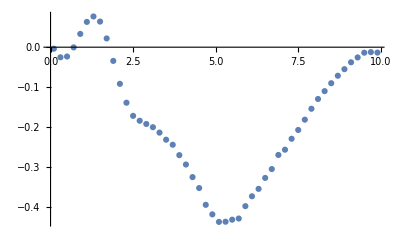

```mathematica
ListPlot[Transpose[{%[[All,1]],Re[%[[All,2,3]]]}]]
```

```mathematica
ParallelTable[{k,v2HZ[k,0.5,1.0,1.0]},{k,0.1,10,0.1}]
```

0.1 starts to run on kern 100 at Fri 3 Feb 2023 22:16:35GMT+1

0.2 starts to run on kern 99 at Fri 3 Feb 2023 22:16:35GMT+1

0.3 starts to run on kern 98 at Fri 3 Feb 2023 22:16:35GMT+1

0.4 starts to run on kern 97 at Fri 3 Feb 2023 22:16:35GMT+1

0.5 starts to run on kern 96 at Fri 3 Feb 2023 22:16:35GMT+1

0.6 starts to run on kern 95 at Fri 3 Feb 2023 22:16:35GMT+1

0.7 starts to run on kern 94 at Fri 3 Feb 2023 22:16:35GMT+1

0.8 starts to run on kern 93 at Fri 3 Feb 2023 22:16:35GMT+1

0.9 starts to run on kern 92 at Fri 3 Feb 2023 22:16:35GMT+1

1. starts to run on kern 91 at Fri 3 Feb 2023 22:16:35GMT+1

1.1 starts to run on kern 90 at Fri 3 Feb 2023 22:16:35GMT+1

1.2 starts to run on kern 89 at Fri 3 Feb 2023 22:16:35GMT+1

1.3 starts to run on kern 88 at Fri 3 Feb 2023 22:16:35GMT+1

1.4 starts to run on kern 87 at Fri 3 Feb 2023 22:16:35GMT+1

1.5 starts to run on kern 86 at Fri 3 Feb 2023 22:16:35GMT+1

1.6 starts to run on kern 85 at Fri 3 Feb 2023 22:16:35GMT+1

1.7 starts to run on kern 84 at Fri 3 Feb 2023 22:16:35GMT+1

1.8 starts to run on kern 83 at Fri 3 Feb 2023 22:16:35GMT+1

1.9 starts to run on kern 82 at Fri 3 Feb 2023 22:16:35GMT+1

2. starts to run on kern 81 at Fri 3 Feb 2023 22:16:35GMT+1

2.1 starts to run on kern 80 at Fri 3 Feb 2023 22:16:35GMT+1

2.2 starts to run on kern 79 at Fri 3 Feb 2023 22:16:35GMT+1

2.3 starts to run on kern 78 at Fri 3 Feb 2023 22:16:35GMT+1

2.4 starts to run on kern 77 at Fri 3 Feb 2023 22:16:35GMT+1

2.5 starts to run on kern 76 at Fri 3 Feb 2023 22:16:35GMT+1

2.6 starts to run on kern 75 at Fri 3 Feb 2023 22:16:35GMT+1

2.7 starts to run on kern 74 at Fri 3 Feb 2023 22:16:35GMT+1

2.8 starts to run on kern 73 at Fri 3 Feb 2023 22:16:35GMT+1

2.9 starts to run on kern 72 at Fri 3 Feb 2023 22:16:35GMT+1

3. starts to run on kern 71 at Fri 3 Feb 2023 22:16:35GMT+1

3.1 starts to run on kern 70 at Fri 3 Feb 2023 22:16:35GMT+1

3.2 starts to run on kern 69 at Fri 3 Feb 2023 22:16:35GMT+1

3.3 starts to run on kern 68 at Fri 3 Feb 2023 22:16:35GMT+1

3.4 starts to run on kern 67 at Fri 3 Feb 2023 22:16:35GMT+1

3.5 starts to run on kern 66 at Fri 3 Feb 2023 22:16:35GMT+1

3.6 starts to run on kern 65 at Fri 3 Feb 2023 22:16:35GMT+1

3.7 starts to run on kern 64 at Fri 3 Feb 2023 22:16:35GMT+1

3.8 starts to run on kern 63 at Fri 3 Feb 2023 22:16:35GMT+1

3.9 starts to run on kern 62 at Fri 3 Feb 2023 22:16:35GMT+1

4. starts to run on kern 61 at Fri 3 Feb 2023 22:16:35GMT+1

4.1 starts to run on kern 60 at Fri 3 Feb 2023 22:16:35GMT+1

4.2 starts to run on kern 59 at Fri 3 Feb 2023 22:16:35GMT+1

4.3 starts to run on kern 58 at Fri 3 Feb 2023 22:16:35GMT+1

4.4 starts to run on kern 57 at Fri 3 Feb 2023 22:16:35GMT+1

4.5 starts to run on kern 56 at Fri 3 Feb 2023 22:16:35GMT+1

4.6 starts to run on kern 55 at Fri 3 Feb 2023 22:16:35GMT+1

4.7 starts to run on kern 54 at Fri 3 Feb 2023 22:16:35GMT+1

4.8 starts to run on kern 53 at Fri 3 Feb 2023 22:16:35GMT+1

4.9 starts to run on kern 52 at Fri 3 Feb 2023 22:16:35GMT+1

5. starts to run on kern 51 at Fri 3 Feb 2023 22:16:35GMT+1

5.1 starts to run on kern 50 at Fri 3 Feb 2023 22:16:35GMT+1

5.2 starts to run on kern 49 at Fri 3 Feb 2023 22:16:35GMT+1

5.3 starts to run on kern 48 at Fri 3 Feb 2023 22:16:35GMT+1

5.4 starts to run on kern 47 at Fri 3 Feb 2023 22:16:35GMT+1

5.5 starts to run on kern 46 at Fri 3 Feb 2023 22:16:35GMT+1

5.6 starts to run on kern 45 at Fri 3 Feb 2023 22:16:35GMT+1

5.7 starts to run on kern 44 at Fri 3 Feb 2023 22:16:35GMT+1

5.8 starts to run on kern 43 at Fri 3 Feb 2023 22:16:35GMT+1

5.9 starts to run on kern 42 at Fri 3 Feb 2023 22:16:35GMT+1

6. starts to run on kern 41 at Fri 3 Feb 2023 22:16:35GMT+1

6.1 starts to run on kern 40 at Fri 3 Feb 2023 22:16:35GMT+1

6.2 starts to run on kern 39 at Fri 3 Feb 2023 22:16:35GMT+1

6.3 starts to run on kern 38 at Fri 3 Feb 2023 22:16:35GMT+1

6.4 starts to run on kern 37 at Fri 3 Feb 2023 22:16:35GMT+1

6.5 starts to run on kern 36 at Fri 3 Feb 2023 22:16:35GMT+1

6.6 starts to run on kern 35 at Fri 3 Feb 2023 22:16:35GMT+1

6.7 starts to run on kern 34 at Fri 3 Feb 2023 22:16:35GMT+1

6.8 starts to run on kern 33 at Fri 3 Feb 2023 22:16:35GMT+1

6.9 starts to run on kern 32 at Fri 3 Feb 2023 22:16:35GMT+1

7. starts to run on kern 31 at Fri 3 Feb 2023 22:16:35GMT+1

7.1 starts to run on kern 30 at Fri 3 Feb 2023 22:16:35GMT+1

7.2 starts to run on kern 29 at Fri 3 Feb 2023 22:16:35GMT+1

7.3 starts to run on kern 28 at Fri 3 Feb 2023 22:16:35GMT+1

7.4 starts to run on kern 27 at Fri 3 Feb 2023 22:16:35GMT+1

7.5 starts to run on kern 26 at Fri 3 Feb 2023 22:16:35GMT+1

7.6 starts to run on kern 25 at Fri 3 Feb 2023 22:16:35GMT+1

7.7 starts to run on kern 24 at Fri 3 Feb 2023 22:16:35GMT+1

7.8 starts to run on kern 23 at Fri 3 Feb 2023 22:16:35GMT+1

7.9 starts to run on kern 22 at Fri 3 Feb 2023 22:16:35GMT+1

8. starts to run on kern 21 at Fri 3 Feb 2023 22:16:35GMT+1

8.1 starts to run on kern 20 at Fri 3 Feb 2023 22:16:35GMT+1

8.2 starts to run on kern 19 at Fri 3 Feb 2023 22:16:35GMT+1

8.3 starts to run on kern 18 at Fri 3 Feb 2023 22:16:35GMT+1

8.4 starts to run on kern 17 at Fri 3 Feb 2023 22:16:35GMT+1

8.5 starts to run on kern 16 at Fri 3 Feb 2023 22:16:35GMT+1

8.6 starts to run on kern 15 at Fri 3 Feb 2023 22:16:35GMT+1

8.7 starts to run on kern 14 at Fri 3 Feb 2023 22:16:35GMT+1

8.8 starts to run on kern 13 at Fri 3 Feb 2023 22:16:35GMT+1

8.9 starts to run on kern 12 at Fri 3 Feb 2023 22:16:35GMT+1

9. starts to run on kern 11 at Fri 3 Feb 2023 22:16:35GMT+1

9.1 starts to run on kern 10 at Fri 3 Feb 2023 22:16:35GMT+1

9.2 starts to run on kern 9 at Fri 3 Feb 2023 22:16:35GMT+1

9.3 starts to run on kern 8 at Fri 3 Feb 2023 22:16:35GMT+1

9.4 starts to run on kern 7 at Fri 3 Feb 2023 22:16:35GMT+1

9.5 starts to run on kern 6 at Fri 3 Feb 2023 22:16:35GMT+1

9.6 starts to run on kern 5 at Fri 3 Feb 2023 22:16:35GMT+1

9.7 starts to run on kern 4 at Fri 3 Feb 2023 22:16:35GMT+1

9.8 starts to run on kern 3 at Fri 3 Feb 2023 22:16:35GMT+1

9.9 starts to run on kern 2 at Fri 3 Feb 2023 22:16:35GMT+1

10. starts to run on kern 1 at Fri 3 Feb 2023 22:16:35GMT+1

2.1 finishes num on kern 80 at Fri 3 Feb 2023 23:29:02GMT+1

Main calculation is done on kern 80 with k_T=2.1 at Fri 3 Feb 2023 23:30:05GMT+1

2.2 finishes num on kern 79 at Fri 3 Feb 2023 23:31:53GMT+1

Main calculation is done on kern 79 with k_T=2.2 at Fri 3 Feb 2023 23:32:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 1.60369+0. ⅈ and 1.14413 for the integral and error estimates.

0.1 finishes num on kern 100 at Fri 3 Feb 2023 23:40:11GMT+1

2.5 finishes num on kern 76 at Fri 3 Feb 2023 23:42:30GMT+1

Main calculation is done on kern 100 with k_T=0.1 at Fri 3 Feb 2023 23:42:41GMT+1

Main calculation is done on kern 76 with k_T=2.5 at Fri 3 Feb 2023 23:43:30GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.845062+0. ⅈ and 0.250049 for the integral and error estimates.

0.2 finishes num on kern 99 at Fri 3 Feb 2023 23:43:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.859115+0. ⅈ and 0.110315 for the integral and error estimates.

0.3 finishes num on kern 98 at Fri 3 Feb 2023 23:43:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.607773+0. ⅈ and 0.045627 for the integral and error estimates.

0.5 finishes num on kern 96 at Fri 3 Feb 2023 23:44:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.600877+0. ⅈ and 0.0189892 for the integral and error estimates.

0.7 finishes num on kern 94 at Fri 3 Feb 2023 23:45:02GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.522381+0. ⅈ and 0.0125174 for the integral and error estimates.

0.9 finishes num on kern 92 at Fri 3 Feb 2023 23:46:04GMT+1

Main calculation is done on kern 98 with k_T=0.3 at Fri 3 Feb 2023 23:46:07GMT+1

Main calculation is done on kern 99 with k_T=0.2 at Fri 3 Feb 2023 23:46:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.491223+0. ⅈ and 0.00862589 for the integral and error estimates.

1. finishes num on kern 91 at Fri 3 Feb 2023 23:46:26GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.630694+0. ⅈ and 0.029918 for the integral and error estimates.

0.6 finishes num on kern 95 at Fri 3 Feb 2023 23:46:41GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.743596+0. ⅈ and 0.0716836 for the integral and error estimates.

0.4 finishes num on kern 97 at Fri 3 Feb 2023 23:46:49GMT+1

Main calculation is done on kern 96 with k_T=0.5 at Fri 3 Feb 2023 23:47:09GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.579079+0. ⅈ and 0.0171269 for the integral and error estimates.

0.8 finishes num on kern 93 at Fri 3 Feb 2023 23:47:26GMT+1

Main calculation is done on kern 94 with k_T=0.7 at Fri 3 Feb 2023 23:47:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.414561+0. ⅈ and 0.0065793 for the integral and error estimates.

1.2 finishes num on kern 89 at Fri 3 Feb 2023 23:48:11GMT+1

Main calculation is done on kern 92 with k_T=0.9 at Fri 3 Feb 2023 23:48:31GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.446896+0. ⅈ and 0.00870581 for the integral and error estimates.

1.1 finishes num on kern 90 at Fri 3 Feb 2023 23:48:48GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.397175+0. ⅈ and 0.00563643 for the integral and error estimates.

1.3 finishes num on kern 88 at Fri 3 Feb 2023 23:48:58GMT+1

Main calculation is done on kern 91 with k_T=1. at Fri 3 Feb 2023 23:48:59GMT+1

Main calculation is done on kern 95 with k_T=0.6 at Fri 3 Feb 2023 23:49:17GMT+1

Main calculation is done on kern 97 with k_T=0.4 at Fri 3 Feb 2023 23:49:18GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.290063+0. ⅈ and 0.00298808 for the integral and error estimates.

1.6 finishes num on kern 85 at Fri 3 Feb 2023 23:49:58GMT+1

Main calculation is done on kern 93 with k_T=0.8 at Fri 3 Feb 2023 23:50:00GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.35626+0. ⅈ and 0.00410922 for the integral and error estimates.

1.4 finishes num on kern 87 at Fri 3 Feb 2023 23:50:22GMT+1

Main calculation is done on kern 89 with k_T=1.2 at Fri 3 Feb 2023 23:50:32GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.32642+0. ⅈ and 0.00437796 for the integral and error estimates.

1.5 finishes num on kern 86 at Fri 3 Feb 2023 23:50:58GMT+1

Main calculation is done on kern 88 with k_T=1.3 at Fri 3 Feb 2023 23:51:17GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.273029+0. ⅈ and 0.00293392 for the integral and error estimates.

1.7 finishes num on kern 84 at Fri 3 Feb 2023 23:51:23GMT+1

Main calculation is done on kern 90 with k_T=1.1 at Fri 3 Feb 2023 23:51:30GMT+1

1.8 finishes num on kern 83 at Fri 3 Feb 2023 23:51:32GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.197231+0. ⅈ and 0.00207517 for the integral and error estimates.

2. finishes num on kern 81 at Fri 3 Feb 2023 23:51:37GMT+1

Main calculation is done on kern 86 with k_T=1.5 at Fri 3 Feb 2023 23:51:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.221107+0. ⅈ and 0.00237867 for the integral and error estimates.

1.9 finishes num on kern 82 at Fri 3 Feb 2023 23:52:03GMT+1

Main calculation is done on kern 85 with k_T=1.6 at Fri 3 Feb 2023 23:52:20GMT+1

Main calculation is done on kern 83 with k_T=1.8 at Fri 3 Feb 2023 23:52:22GMT+1

Main calculation is done on kern 81 with k_T=2. at Fri 3 Feb 2023 23:52:24GMT+1

Main calculation is done on kern 87 with k_T=1.4 at Fri 3 Feb 2023 23:52:49GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.143538+0. ⅈ and 0.001822 for the integral and error estimates.

2.3 finishes num on kern 78 at Fri 3 Feb 2023 23:52:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0759049+0. ⅈ and 0.00109557 for the integral and error estimates.

2.8 finishes num on kern 73 at Fri 3 Feb 2023 23:53:00GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.084352+0. ⅈ and 0.00120611 for the integral and error estimates.

2.7 finishes num on kern 74 at Fri 3 Feb 2023 23:53:03GMT+1

Main calculation is done on kern 82 with k_T=1.9 at Fri 3 Feb 2023 23:53:03GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0663444+0. ⅈ and 0.00103022 for the integral and error estimates.

2.9 finishes num on kern 72 at Fri 3 Feb 2023 23:53:19GMT+1

Main calculation is done on kern 78 with k_T=2.3 at Fri 3 Feb 2023 23:53:41GMT+1

Main calculation is done on kern 74 with k_T=2.7 at Fri 3 Feb 2023 23:53:46GMT+1

Main calculation is done on kern 84 with k_T=1.7 at Fri 3 Feb 2023 23:53:46GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0966504+0. ⅈ and 0.00118663 for the integral and error estimates.

2.6 finishes num on kern 75 at Fri 3 Feb 2023 23:53:48GMT+1

Main calculation is done on kern 73 with k_T=2.8 at Fri 3 Feb 2023 23:53:49GMT+1

Main calculation is done on kern 72 with k_T=2.9 at Fri 3 Feb 2023 23:53:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0498523+0. ⅈ and 0.000754894 for the integral and error estimates.

3.1 finishes num on kern 70 at Fri 3 Feb 2023 23:53:56GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.127428+0. ⅈ and 0.00139083 for the integral and error estimates.

2.4 finishes num on kern 77 at Fri 3 Feb 2023 23:54:01GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0426496+0. ⅈ and 0.000635774 for the integral and error estimates.

3.2 finishes num on kern 69 at Fri 3 Feb 2023 23:54:05GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0265742+0. ⅈ and 0.000558935 for the integral and error estimates.

3.5 finishes num on kern 66 at Fri 3 Feb 2023 23:54:22GMT+1

Main calculation is done on kern 75 with k_T=2.6 at Fri 3 Feb 2023 23:54:36GMT+1

Main calculation is done on kern 70 with k_T=3.1 at Fri 3 Feb 2023 23:54:36GMT+1

Main calculation is done on kern 77 with k_T=2.4 at Fri 3 Feb 2023 23:54:47GMT+1

Main calculation is done on kern 69 with k_T=3.2 at Fri 3 Feb 2023 23:54:48GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0314068+0. ⅈ and 0.000637409 for the integral and error estimates.

3.4 finishes num on kern 67 at Fri 3 Feb 2023 23:54:58GMT+1

Main calculation is done on kern 66 with k_T=3.5 at Fri 3 Feb 2023 23:55:09GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0139433+0. ⅈ and 0.000383253 for the integral and error estimates.

3.9 finishes num on kern 62 at Fri 3 Feb 2023 23:55:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0572546+0. ⅈ and 0.000644843 for the integral and error estimates.

3. finishes num on kern 71 at Fri 3 Feb 2023 23:55:21GMT+1

Main calculation is done on kern 67 with k_T=3.4 at Fri 3 Feb 2023 23:55:35GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0224351+0. ⅈ and 0.000390245 for the integral and error estimates.

3.6 finishes num on kern 65 at Fri 3 Feb 2023 23:55:38GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0158329+0. ⅈ and 0.000332167 for the integral and error estimates.

3.8 finishes num on kern 63 at Fri 3 Feb 2023 23:55:38GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0195261+0. ⅈ and 0.000358888 for the integral and error estimates.

3.7 finishes num on kern 64 at Fri 3 Feb 2023 23:55:40GMT+1

Main calculation is done on kern 62 with k_T=3.9 at Fri 3 Feb 2023 23:55:57GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0372582+0. ⅈ and 0.000602706 for the integral and error estimates.

3.3 finishes num on kern 68 at Fri 3 Feb 2023 23:56:03GMT+1

Main calculation is done on kern 71 with k_T=3. at Fri 3 Feb 2023 23:56:05GMT+1

Main calculation is done on kern 63 with k_T=3.8 at Fri 3 Feb 2023 23:56:16GMT+1

Main calculation is done on kern 64 with k_T=3.7 at Fri 3 Feb 2023 23:56:18GMT+1

Main calculation is done on kern 65 with k_T=3.6 at Fri 3 Feb 2023 23:56:18GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00780609+0. ⅈ and 0.000243087 for the integral and error estimates.

4.2 finishes num on kern 59 at Fri 3 Feb 2023 23:56:23GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00443342+0. ⅈ and 0.000318998 for the integral and error estimates.

4.5 finishes num on kern 56 at Fri 3 Feb 2023 23:56:30GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00367963+0. ⅈ and 0.000300489 for the integral and error estimates.

4.6 finishes num on kern 55 at Fri 3 Feb 2023 23:56:39GMT+1

Main calculation is done on kern 68 with k_T=3.3 at Fri 3 Feb 2023 23:56:46GMT+1

Main calculation is done on kern 59 with k_T=4.2 at Fri 3 Feb 2023 23:57:01GMT+1

Main calculation is done on kern 56 with k_T=4.5 at Fri 3 Feb 2023 23:57:06GMT+1

Main calculation is done on kern 55 with k_T=4.6 at Fri 3 Feb 2023 23:57:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00258807+0. ⅈ and 0.00019109 for the integral and error estimates.

5. finishes num on kern 51 at Fri 3 Feb 2023 23:57:16GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.010932+0. ⅈ and 0.000287503 for the integral and error estimates.

4. finishes num on kern 61 at Fri 3 Feb 2023 23:57:24GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00693291+0. ⅈ and 0.000222423 for the integral and error estimates.

4.3 finishes num on kern 58 at Fri 3 Feb 2023 23:57:40GMT+1

Main calculation is done on kern 51 with k_T=5. at Fri 3 Feb 2023 23:57:52GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00949876+0. ⅈ and 0.000276475 for the integral and error estimates.

4.1 finishes num on kern 60 at Fri 3 Feb 2023 23:57:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00154043+0. ⅈ and 0.0000839837 for the integral and error estimates.

5.9 finishes num on kern 42 at Fri 3 Feb 2023 23:57:57GMT+1

Main calculation is done on kern 61 with k_T=4. at Fri 3 Feb 2023 23:58:04GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0050698+0. ⅈ and 0.000351083 for the integral and error estimates.

4.4 finishes num on kern 57 at Fri 3 Feb 2023 23:58:07GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00362348+0. ⅈ and 0.000168193 for the integral and error estimates.

4.7 finishes num on kern 54 at Fri 3 Feb 2023 23:58:09GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00150125+0. ⅈ and 0.000118358 for the integral and error estimates.

6. finishes num on kern 41 at Fri 3 Feb 2023 23:58:21GMT+1

Main calculation is done on kern 58 with k_T=4.3 at Fri 3 Feb 2023 23:58:22GMT+1

Main calculation is done on kern 42 with k_T=5.9 at Fri 3 Feb 2023 23:58:33GMT+1

Main calculation is done on kern 60 with k_T=4.1 at Fri 3 Feb 2023 23:58:33GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00154452+0. ⅈ and 0.0000785973 for the integral and error estimates.

6.1 finishes num on kern 40 at Fri 3 Feb 2023 23:58:37GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00282784+0. ⅈ and 0.000142981 for the integral and error estimates.

4.9 finishes num on kern 52 at Fri 3 Feb 2023 23:58:39GMT+1

Main calculation is done on kern 57 with k_T=4.4 at Fri 3 Feb 2023 23:58:43GMT+1

Main calculation is done on kern 54 with k_T=4.7 at Fri 3 Feb 2023 23:58:45GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000764225+0. ⅈ and 0.0000668542 for the integral and error estimates.

6.9 finishes num on kern 32 at Fri 3 Feb 2023 23:58:48GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0031524+0. ⅈ and 0.000161804 for the integral and error estimates.

4.8 finishes num on kern 53 at Fri 3 Feb 2023 23:58:50GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00200831+0. ⅈ and 0.000110696 for the integral and error estimates.

5.3 finishes num on kern 48 at Fri 3 Feb 2023 23:58:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0013301+0. ⅈ and 0.000103008 for the integral and error estimates.

6.5 finishes num on kern 36 at Fri 3 Feb 2023 23:58:56GMT+1

Main calculation is done on kern 41 with k_T=6. at Fri 3 Feb 2023 23:58:56GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000821995+0. ⅈ and 0.0000684941 for the integral and error estimates.

7. finishes num on kern 31 at Fri 3 Feb 2023 23:58:56GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00209825+0. ⅈ and 0.00017903 for the integral and error estimates.

5.2 finishes num on kern 49 at Fri 3 Feb 2023 23:59:03GMT+1

Main calculation is done on kern 40 with k_T=6.1 at Fri 3 Feb 2023 23:59:11GMT+1

Main calculation is done on kern 52 with k_T=4.9 at Fri 3 Feb 2023 23:59:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00218095+0. ⅈ and 0.000151167 for the integral and error estimates.

5.1 finishes num on kern 50 at Fri 3 Feb 2023 23:59:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00186203+0. ⅈ and 0.000192009 for the integral and error estimates.

5.4 finishes num on kern 47 at Fri 3 Feb 2023 23:59:18GMT+1

Main calculation is done on kern 32 with k_T=6.9 at Fri 3 Feb 2023 23:59:23GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000605832+0. ⅈ and 0.0000488601 for the integral and error estimates.

7.1 finishes num on kern 30 at Fri 3 Feb 2023 23:59:23GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00102981+0. ⅈ and 0.000104672 for the integral and error estimates.

6.8 finishes num on kern 33 at Fri 3 Feb 2023 23:59:24GMT+1

Main calculation is done on kern 53 with k_T=4.8 at Fri 3 Feb 2023 23:59:25GMT+1

Main calculation is done on kern 48 with k_T=5.3 at Fri 3 Feb 2023 23:59:30GMT+1

Main calculation is done on kern 36 with k_T=6.5 at Fri 3 Feb 2023 23:59:31GMT+1

Main calculation is done on kern 31 with k_T=7. at Fri 3 Feb 2023 23:59:31GMT+1

Main calculation is done on kern 49 with k_T=5.2 at Fri 3 Feb 2023 23:59:38GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00180744+0. ⅈ and 0.000145204 for the integral and error estimates.

5.8 finishes num on kern 43 at Fri 3 Feb 2023 23:59:47GMT+1

Main calculation is done on kern 50 with k_T=5.1 at Fri 3 Feb 2023 23:59:50GMT+1

Main calculation is done on kern 47 with k_T=5.4 at Fri 3 Feb 2023 23:59:51GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00160244+0. ⅈ and 0.000111457 for the integral and error estimates.

6.2 finishes num on kern 39 at Fri 3 Feb 2023 23:59:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0016452+0. ⅈ and 0.000111971 for the integral and error estimates.

5.6 finishes num on kern 45 at Fri 3 Feb 2023 23:59:56GMT+1

Main calculation is done on kern 30 with k_T=7.1 at Fri 3 Feb 2023 23:59:56GMT+1

Main calculation is done on kern 33 with k_T=6.8 at Fri 3 Feb 2023 23:59:57GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00185489+0. ⅈ and 0.000157884 for the integral and error estimates.

5.5 finishes num on kern 46 at Fri 3 Feb 2023 23:59:58GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00146887+0. ⅈ and 0.000104162 for the integral and error estimates.

6.4 finishes num on kern 37 at Sat 4 Feb 2023 00:00:18GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00174945+0. ⅈ and 0.0000961293 for the integral and error estimates.

5.7 finishes num on kern 44 at Sat 4 Feb 2023 00:00:19GMT+1

Main calculation is done on kern 43 with k_T=5.8 at Sat 4 Feb 2023 00:00:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00148932+0. ⅈ and 0.000110395 for the integral and error estimates.

6.3 finishes num on kern 38 at Sat 4 Feb 2023 00:00:21GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000134626+0. ⅈ and 0.0000562935 for the integral and error estimates.

7.8 finishes num on kern 23 at Sat 4 Feb 2023 00:00:22GMT+1

Main calculation is done on kern 39 with k_T=6.2 at Sat 4 Feb 2023 00:00:27GMT+1

Main calculation is done on kern 46 with k_T=5.5 at Sat 4 Feb 2023 00:00:29GMT+1

Main calculation is done on kern 45 with k_T=5.6 at Sat 4 Feb 2023 00:00:30GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000342187+0. ⅈ and 0.0000328928 for the integral and error estimates.

8.1 finishes num on kern 20 at Sat 4 Feb 2023 00:00:31GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000955892+0. ⅈ and 0.0000594342 for the integral and error estimates.

6.7 finishes num on kern 34 at Sat 4 Feb 2023 00:00:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000157143+0. ⅈ and 0.0000688097 for the integral and error estimates.

7.5 finishes num on kern 26 at Sat 4 Feb 2023 00:00:46GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00124569+0. ⅈ and 0.0000874653 for the integral and error estimates.

6.6 finishes num on kern 35 at Sat 4 Feb 2023 00:00:48GMT+1

Main calculation is done on kern 37 with k_T=6.4 at Sat 4 Feb 2023 00:00:49GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000508019+0. ⅈ and 0.0000530241 for the integral and error estimates.

7.2 finishes num on kern 29 at Sat 4 Feb 2023 00:00:49GMT+1

Main calculation is done on kern 44 with k_T=5.7 at Sat 4 Feb 2023 00:00:50GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000639735+0. ⅈ and 0.0000275713 for the integral and error estimates.

8.7 finishes num on kern 14 at Sat 4 Feb 2023 00:00:51GMT+1

Main calculation is done on kern 38 with k_T=6.3 at Sat 4 Feb 2023 00:00:53GMT+1

Main calculation is done on kern 23 with k_T=7.8 at Sat 4 Feb 2023 00:00:53GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000471843+0. ⅈ and 0.0000340778 for the integral and error estimates.

8.4 finishes num on kern 17 at Sat 4 Feb 2023 00:00:54GMT+1

Main calculation is done on kern 20 with k_T=8.1 at Sat 4 Feb 2023 00:01:02GMT+1

Main calculation is done on kern 34 with k_T=6.7 at Sat 4 Feb 2023 00:01:15GMT+1

Main calculation is done on kern 26 with k_T=7.5 at Sat 4 Feb 2023 00:01:17GMT+1

Main calculation is done on kern 35 with k_T=6.6 at Sat 4 Feb 2023 00:01:19GMT+1

Main calculation is done on kern 29 with k_T=7.2 at Sat 4 Feb 2023 00:01:19GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000339662+0. ⅈ and 0.0000431546 for the integral and error estimates.

7.4 finishes num on kern 27 at Sat 4 Feb 2023 00:01:20GMT+1

Main calculation is done on kern 14 with k_T=8.7 at Sat 4 Feb 2023 00:01:22GMT+1

Main calculation is done on kern 17 with k_T=8.4 at Sat 4 Feb 2023 00:01:25GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000289146+0. ⅈ and 0.0000326833 for the integral and error estimates.

8. finishes num on kern 21 at Sat 4 Feb 2023 00:01:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00010363+0. ⅈ and 0.000061868 for the integral and error estimates.

7.6 finishes num on kern 25 at Sat 4 Feb 2023 00:01:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000220376+0. ⅈ and 0.0000607489 for the integral and error estimates.

7.9 finishes num on kern 22 at Sat 4 Feb 2023 00:01:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000507212+0. ⅈ and 0.0000486839 for the integral and error estimates.

8.3 finishes num on kern 18 at Sat 4 Feb 2023 00:01:50GMT+1

Main calculation is done on kern 27 with k_T=7.4 at Sat 4 Feb 2023 00:01:50GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000373631+0. ⅈ and 0.0000502248 for the integral and error estimates.

7.7 finishes num on kern 24 at Sat 4 Feb 2023 00:02:07GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00033629+0. ⅈ and 0.0000635744 for the integral and error estimates.

7.3 finishes num on kern 28 at Sat 4 Feb 2023 00:02:08GMT+1

Main calculation is done on kern 21 with k_T=8. at Sat 4 Feb 2023 00:02:13GMT+1

Main calculation is done on kern 25 with k_T=7.6 at Sat 4 Feb 2023 00:02:14GMT+1

Main calculation is done on kern 22 with k_T=7.9 at Sat 4 Feb 2023 00:02:16GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000615985+0. ⅈ and 0.0000279431 for the integral and error estimates.

8.5 finishes num on kern 16 at Sat 4 Feb 2023 00:02:20GMT+1

Main calculation is done on kern 18 with k_T=8.3 at Sat 4 Feb 2023 00:02:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000452665+0. ⅈ and 0.0000435764 for the integral and error estimates.

8.2 finishes num on kern 19 at Sat 4 Feb 2023 00:02:29GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000641786+0. ⅈ and 0.0000318392 for the integral and error estimates.

9.1 finishes num on kern 10 at Sat 4 Feb 2023 00:02:30GMT+1

Main calculation is done on kern 24 with k_T=7.7 at Sat 4 Feb 2023 00:02:37GMT+1

Main calculation is done on kern 28 with k_T=7.3 at Sat 4 Feb 2023 00:02:37GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00068736+0. ⅈ and 0.0000261325 for the integral and error estimates.

8.8 finishes num on kern 13 at Sat 4 Feb 2023 00:02:44GMT+1

Main calculation is done on kern 16 with k_T=8.5 at Sat 4 Feb 2023 00:02:49GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00059507+0. ⅈ and 0.000042846 for the integral and error estimates.

8.6 finishes num on kern 15 at Sat 4 Feb 2023 00:02:49GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000651179+0. ⅈ and 0.0000315087 for the integral and error estimates.

9.2 finishes num on kern 9 at Sat 4 Feb 2023 00:02:55GMT+1

Main calculation is done on kern 19 with k_T=8.2 at Sat 4 Feb 2023 00:02:59GMT+1

Main calculation is done on kern 10 with k_T=9.1 at Sat 4 Feb 2023 00:03:00GMT+1

Main calculation is done on kern 13 with k_T=8.8 at Sat 4 Feb 2023 00:03:14GMT+1

Main calculation is done on kern 15 with k_T=8.6 at Sat 4 Feb 2023 00:03:18GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00064841+0. ⅈ and 0.0000250181 for the integral and error estimates.

8.9 finishes num on kern 12 at Sat 4 Feb 2023 00:03:20GMT+1

Main calculation is done on kern 9 with k_T=9.2 at Sat 4 Feb 2023 00:03:26GMT+1

Main calculation is done on kern 12 with k_T=8.9 at Sat 4 Feb 2023 00:03:50GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00065737+0. ⅈ and 0.0000230689 for the integral and error estimates.

9. finishes num on kern 11 at Sat 4 Feb 2023 00:03:58GMT+1

Main calculation is done on kern 11 with k_T=9. at Sat 4 Feb 2023 00:04:27GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000575763+0. ⅈ and 0.0000300725 for the integral and error estimates.

9.4 finishes num on kern 7 at Sat 4 Feb 2023 00:04:31GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000635651+0. ⅈ and 0.0000257007 for the integral and error estimates.

9.3 finishes num on kern 8 at Sat 4 Feb 2023 00:04:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000597837+0. ⅈ and 0.0000270423 for the integral and error estimates.

9.6 finishes num on kern 5 at Sat 4 Feb 2023 00:04:45GMT+1

Main calculation is done on kern 7 with k_T=9.4 at Sat 4 Feb 2023 00:05:02GMT+1

Main calculation is done on kern 8 with k_T=9.3 at Sat 4 Feb 2023 00:05:13GMT+1

Main calculation is done on kern 5 with k_T=9.6 at Sat 4 Feb 2023 00:05:16GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000454022+0. ⅈ and 0.0000213988 for the integral and error estimates.

10. finishes num on kern 1 at Sat 4 Feb 2023 00:05:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000628072+0. ⅈ and 0.0000199973 for the integral and error estimates.

9.5 finishes num on kern 6 at Sat 4 Feb 2023 00:06:06GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000551724+0. ⅈ and 0.0000222192 for the integral and error estimates.

9.7 finishes num on kern 4 at Sat 4 Feb 2023 00:06:06GMT+1

Main calculation is done on kern 1 with k_T=10. at Sat 4 Feb 2023 00:06:08GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000465788+0. ⅈ and 0.0000188158 for the integral and error estimates.

9.9 finishes num on kern 2 at Sat 4 Feb 2023 00:06:08GMT+1

Main calculation is done on kern 6 with k_T=9.5 at Sat 4 Feb 2023 00:06:37GMT+1

Main calculation is done on kern 4 with k_T=9.7 at Sat 4 Feb 2023 00:06:38GMT+1

Main calculation is done on kern 2 with k_T=9.9 at Sat 4 Feb 2023 00:06:40GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000531042+0. ⅈ and 0.000027955 for the integral and error estimates.

9.8 finishes num on kern 3 at Sat 4 Feb 2023 00:07:16GMT+1

Main calculation is done on kern 3 with k_T=9.8 at Sat 4 Feb 2023 00:07:47GMT+1

{{0.1,{1.60369,1030.02,0.00155695}},{0.2,{-0.845062+0. ⅈ,251.925,-0.00335442+0. ⅈ}},{0.3,{-0.859115+0. ⅈ,110.027,-0.00780823+0. ⅈ}},{0.4,{-0.743596+0. ⅈ,60.7523,-0.0122398+0. ⅈ}},{0.5,{-0.607773+0. ⅈ,38.289,-0.0158733+0. ⅈ}},{0.6,{-0.630694+0. ⅈ,25.3414,-0.0248879+0. ⅈ}},{0.7,{-0.600877+0. ⅈ,18.6334,-0.0322473+0. ⅈ}},{0.8,{-0.579079+0. ⅈ,13.6589,-0.0423956+0. ⅈ}},{0.9,{-0.522381+0. ⅈ,10.6792,-0.0489158+0. ⅈ}},{1.,{-0.491223+0. ⅈ,8.64431,-0.0568262+0. ⅈ}},{1.1,{-0.446896+0. ⅈ,7.0213,-0.0636485+0. ⅈ}},{1.2,{-0.414561+0. ⅈ,5.80352,-0.0714327+0. ⅈ}},{1.3,{-0.397175+0. ⅈ,4.82718,-0.0822789+0. ⅈ}},{1.4,{-0.35626+0. ⅈ,4.14953,-0.0858555+0. ⅈ}},{1.5,{-0.32642+0. ⅈ,3.56331,-0.0916058+0. ⅈ}},{1.6,{-0.290063+0. ⅈ,3.1747,-0.091367+0. ⅈ}},{1.7,{-0.273029+0. ⅈ,2.75227,-0.0992013+0. ⅈ}},{1.8,{-0.24417+0. ⅈ,2.41221,-0.101223+0. ⅈ}},{1.9,{-0.221107+0. ⅈ,2.17969,-0.10144+0. ⅈ}},{2.,{-0.197231+0. ⅈ,1.94214,-0.101553+0. ⅈ}},{2.1,{-0.1811+0. ⅈ,1.76617,-0.102539+0. ⅈ}},{2.2,{-0.1583+0. ⅈ,1.60616,-0.098558+0. ⅈ}},{2.3,{-0.143538+0. ⅈ,1.45969,-0.0983346+0. ⅈ}},{2.4,{-0.127428+0. ⅈ,1.33702,-0.0953076+0. ⅈ}},{2.5,{-0.111611+0. ⅈ,1.23027,-0.0907204+0. ⅈ}},{2.6,{-0.0966504+0. ⅈ,1.1151,-0.0866744+0. ⅈ}},{2.7,{-0.084352+0. ⅈ,1.0238,-0.0823908+0. ⅈ}},{2.8,{-0.0759049+0. ⅈ,0.947389,-0.0801201+0. ⅈ}},{2.9,{-0.0663444+0. ⅈ,0.878451,-0.0755243+0. ⅈ}},{3.,{-0.0572546+0. ⅈ,0.802046,-0.0713857+0. ⅈ}},{3.1,{-0.0498523+0. ⅈ,0.754626,-0.0660623+0. ⅈ}},{3.2,{-0.0426496+0. ⅈ,0.689209,-0.0618819+0. ⅈ}},{3.3,{-0.0372582+0. ⅈ,0.637748,-0.0584215+0. ⅈ}},{3.4,{-0.0314068+0. ⅈ,0.592524,-0.0530051+0. ⅈ}},{3.5,{-0.0265742+0. ⅈ,0.559391,-0.0475056+0. ⅈ}},{3.6,{-0.0224351+0. ⅈ,0.522023,-0.0429771+0. ⅈ}},{3.7,{-0.0195261+0. ⅈ,0.485181,-0.0402449+0. ⅈ}},{3.8,{-0.0158329+0. ⅈ,0.455001,-0.0347975+0. ⅈ}},{3.9,{-0.0139433+0. ⅈ,0.426876,-0.0326635+0. ⅈ}},{4.,{-0.010932+0. ⅈ,0.394264,-0.0277277+0. ⅈ}},{4.1,{-0.00949876+0. ⅈ,0.371672,-0.0255568+0. ⅈ}},{4.2,{-0.00780609+0. ⅈ,0.345117,-0.0226187+0. ⅈ}},{4.3,{-0.00693291+0. ⅈ,0.327706,-0.0211559+0. ⅈ}},{4.4,{-0.0050698+0. ⅈ,0.307285,-0.0164987+0. ⅈ}},{4.5,{-0.00443342+0. ⅈ,0.286627,-0.0154676+0. ⅈ}},{4.6,{-0.00367963+0. ⅈ,0.269774,-0.0136397+0. ⅈ}},{4.7,{-0.00362348+0. ⅈ,0.253556,-0.0142907+0. ⅈ}},{4.8,{-0.0031524+0. ⅈ,0.242483,-0.0130005+0. ⅈ}},{4.9,{-0.00282784+0. ⅈ,0.229143,-0.0123409+0. ⅈ}},{5.,{-0.00258807+0. ⅈ,0.21633,-0.0119635+0. ⅈ}},{5.1,{-0.00218095+0. ⅈ,0.203445,-0.0107201+0. ⅈ}},{5.2,{-0.00209825+0. ⅈ,0.191767,-0.0109416+0. ⅈ}},{5.3,{-0.00200831+0. ⅈ,0.18433,-0.0108952+0. ⅈ}},{5.4,{-0.00186203+0. ⅈ,0.17342,-0.0107371+0. ⅈ}},{5.5,{-0.00185489+0. ⅈ,0.164612,-0.0112683+0. ⅈ}},{5.6,{-0.0016452+0. ⅈ,0.156079,-0.0105409+0. ⅈ}},{5.7,{-0.00174945+0. ⅈ,0.148153,-0.0118083+0. ⅈ}},{5.8,{-0.00180744+0. ⅈ,0.139862,-0.012923+0. ⅈ}},{5.9,{-0.00154043+0. ⅈ,0.134083,-0.0114887+0. ⅈ}},{6.,{-0.00150125+0. ⅈ,0.129589,-0.0115847+0. ⅈ}},{6.1,{-0.00154452+0. ⅈ,0.120922,-0.0127728+0. ⅈ}},{6.2,{-0.00160244+0. ⅈ,0.11588,-0.0138285+0. ⅈ}},{6.3,{-0.00148932+0. ⅈ,0.110889,-0.0134307+0. ⅈ}},{6.4,{-0.00146887+0. ⅈ,0.105719,-0.0138941+0. ⅈ}},{6.5,{-0.0013301+0. ⅈ,0.10169,-0.01308+0. ⅈ}},{6.6,{-0.00124569+0. ⅈ,0.0976134,-0.0127614+0. ⅈ}},{6.7,{-0.000955892+0. ⅈ,0.0926334,-0.0103191+0. ⅈ}},{6.8,{-0.00102981+0. ⅈ,0.0886523,-0.0116163+0. ⅈ}},{6.9,{-0.000764225+0. ⅈ,0.084527,-0.00904118+0. ⅈ}},{7.,{-0.000821995+0. ⅈ,0.0797955,-0.0103013+0. ⅈ}},{7.1,{-0.000605832+0. ⅈ,0.0761667,-0.00795403+0. ⅈ}},{7.2,{-0.000508019+0. ⅈ,0.0734437,-0.00691712+0. ⅈ}},{7.3,{-0.00033629+0. ⅈ,0.0692353,-0.0048572+0. ⅈ}},{7.4,{-0.000339662+0. ⅈ,0.0662947,-0.00512352+0. ⅈ}},{7.5,{-0.000157143+0. ⅈ,0.0640462,-0.00245359+0. ⅈ}},{7.6,{-0.00010363+0. ⅈ,0.0607052,-0.0017071+0. ⅈ}},{7.7,{-0.0000373631+0. ⅈ,0.0584127,-0.00063964+0. ⅈ}},{7.8,{0.000134626,0.0551301,0.00244197}},{7.9,{0.000220376,0.0524562,0.00420115}},{8.,{0.000289146,0.0501812,0.00576203}},{8.1,{0.000342187,0.0479974,0.00712928}},{8.2,{0.000452665,0.0458183,0.00987957}},{8.3,{0.000507212,0.044247,0.0114632}},{8.4,{0.000471843,0.041222,0.0114464}},{8.5,{0.000615985,0.0397341,0.0155027}},{8.6,{0.00059507,0.0378208,0.0157339}},{8.7,{0.000639735,0.0359324,0.0178038}},{8.8,{0.00068736,0.0343823,0.0199917}},{8.9,{0.00064841,0.0330885,0.0195962}},{9.,{0.00065737,0.0317125,0.020729}},{9.1,{0.000641786,0.029895,0.021468}},{9.2,{0.000651179,0.0287374,0.0226596}},{9.3,{0.000635651,0.0270922,0.0234625}},{9.4,{0.000575763,0.0264328,0.0217822}},{9.5,{0.000628072,0.0249778,0.0251453}},{9.6,{0.000597837,0.0243141,0.0245881}},{9.7,{0.000551724,0.0230642,0.0239212}},{9.8,{0.000531042,0.0220579,0.0240749}},{9.9,{0.000465788,0.020967,0.0222154}},{10.,{0.000454022,0.0200368,0.0226595}}}

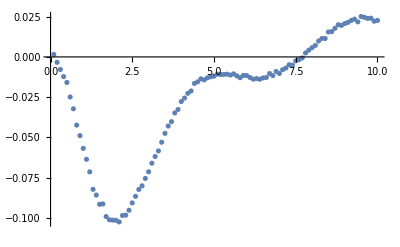

```mathematica
ListPlot[Transpose[{Out[25][[All,1]],Re[Out[25][[All,2,3]]]}]]
```

```mathematica
ParallelTable[{k,v2HZ[k,0.2,1.0,1.0]},{k,0.1,10,0.1}]
```

0.1 starts to run on kern 100 at Sat 4 Feb 2023 00:07:48GMT+1

0.2 starts to run on kern 99 at Sat 4 Feb 2023 00:07:48GMT+1

0.3 starts to run on kern 98 at Sat 4 Feb 2023 00:07:48GMT+1

0.4 starts to run on kern 97 at Sat 4 Feb 2023 00:07:48GMT+1

0.5 starts to run on kern 96 at Sat 4 Feb 2023 00:07:48GMT+1

0.6 starts to run on kern 95 at Sat 4 Feb 2023 00:07:48GMT+1

0.7 starts to run on kern 94 at Sat 4 Feb 2023 00:07:48GMT+1

0.8 starts to run on kern 93 at Sat 4 Feb 2023 00:07:48GMT+1

0.9 starts to run on kern 92 at Sat 4 Feb 2023 00:07:48GMT+1

1. starts to run on kern 91 at Sat 4 Feb 2023 00:07:48GMT+1

1.1 starts to run on kern 90 at Sat 4 Feb 2023 00:07:48GMT+1

1.2 starts to run on kern 89 at Sat 4 Feb 2023 00:07:48GMT+1

1.3 starts to run on kern 88 at Sat 4 Feb 2023 00:07:48GMT+1

1.4 starts to run on kern 87 at Sat 4 Feb 2023 00:07:48GMT+1

1.5 starts to run on kern 86 at Sat 4 Feb 2023 00:07:48GMT+1

1.6 starts to run on kern 85 at Sat 4 Feb 2023 00:07:48GMT+1

1.7 starts to run on kern 84 at Sat 4 Feb 2023 00:07:48GMT+1

1.8 starts to run on kern 83 at Sat 4 Feb 2023 00:07:48GMT+1

1.9 starts to run on kern 82 at Sat 4 Feb 2023 00:07:48GMT+1

2. starts to run on kern 81 at Sat 4 Feb 2023 00:07:48GMT+1

2.1 starts to run on kern 80 at Sat 4 Feb 2023 00:07:48GMT+1

2.2 starts to run on kern 79 at Sat 4 Feb 2023 00:07:48GMT+1

2.3 starts to run on kern 78 at Sat 4 Feb 2023 00:07:48GMT+1

2.4 starts to run on kern 77 at Sat 4 Feb 2023 00:07:48GMT+1

2.5 starts to run on kern 76 at Sat 4 Feb 2023 00:07:48GMT+1

2.6 starts to run on kern 75 at Sat 4 Feb 2023 00:07:48GMT+1

2.7 starts to run on kern 74 at Sat 4 Feb 2023 00:07:48GMT+1

2.8 starts to run on kern 73 at Sat 4 Feb 2023 00:07:48GMT+1

2.9 starts to run on kern 72 at Sat 4 Feb 2023 00:07:48GMT+1

3. starts to run on kern 71 at Sat 4 Feb 2023 00:07:48GMT+1

3.1 starts to run on kern 70 at Sat 4 Feb 2023 00:07:48GMT+1

3.2 starts to run on kern 69 at Sat 4 Feb 2023 00:07:48GMT+1

3.3 starts to run on kern 68 at Sat 4 Feb 2023 00:07:48GMT+1

3.4 starts to run on kern 67 at Sat 4 Feb 2023 00:07:48GMT+1

3.5 starts to run on kern 66 at Sat 4 Feb 2023 00:07:48GMT+1

3.6 starts to run on kern 65 at Sat 4 Feb 2023 00:07:48GMT+1

3.7 starts to run on kern 64 at Sat 4 Feb 2023 00:07:48GMT+1

3.8 starts to run on kern 63 at Sat 4 Feb 2023 00:07:48GMT+1

3.9 starts to run on kern 62 at Sat 4 Feb 2023 00:07:48GMT+1

4. starts to run on kern 61 at Sat 4 Feb 2023 00:07:48GMT+1

4.1 starts to run on kern 60 at Sat 4 Feb 2023 00:07:48GMT+1

4.2 starts to run on kern 59 at Sat 4 Feb 2023 00:07:48GMT+1

4.3 starts to run on kern 58 at Sat 4 Feb 2023 00:07:48GMT+1

4.4 starts to run on kern 57 at Sat 4 Feb 2023 00:07:48GMT+1

4.5 starts to run on kern 56 at Sat 4 Feb 2023 00:07:48GMT+1

4.6 starts to run on kern 55 at Sat 4 Feb 2023 00:07:48GMT+1

4.7 starts to run on kern 54 at Sat 4 Feb 2023 00:07:48GMT+1

4.8 starts to run on kern 53 at Sat 4 Feb 2023 00:07:48GMT+1

4.9 starts to run on kern 52 at Sat 4 Feb 2023 00:07:48GMT+1

5. starts to run on kern 51 at Sat 4 Feb 2023 00:07:48GMT+1

5.1 starts to run on kern 50 at Sat 4 Feb 2023 00:07:48GMT+1

5.2 starts to run on kern 49 at Sat 4 Feb 2023 00:07:48GMT+1

5.3 starts to run on kern 48 at Sat 4 Feb 2023 00:07:48GMT+1

5.4 starts to run on kern 47 at Sat 4 Feb 2023 00:07:48GMT+1

5.5 starts to run on kern 46 at Sat 4 Feb 2023 00:07:48GMT+1

5.6 starts to run on kern 45 at Sat 4 Feb 2023 00:07:48GMT+1

5.7 starts to run on kern 44 at Sat 4 Feb 2023 00:07:48GMT+1

5.8 starts to run on kern 43 at Sat 4 Feb 2023 00:07:48GMT+1

5.9 starts to run on kern 42 at Sat 4 Feb 2023 00:07:48GMT+1

6. starts to run on kern 41 at Sat 4 Feb 2023 00:07:48GMT+1

6.1 starts to run on kern 40 at Sat 4 Feb 2023 00:07:48GMT+1

6.2 starts to run on kern 39 at Sat 4 Feb 2023 00:07:48GMT+1

6.3 starts to run on kern 38 at Sat 4 Feb 2023 00:07:48GMT+1

6.4 starts to run on kern 37 at Sat 4 Feb 2023 00:07:48GMT+1

6.5 starts to run on kern 36 at Sat 4 Feb 2023 00:07:48GMT+1

6.6 starts to run on kern 35 at Sat 4 Feb 2023 00:07:48GMT+1

6.7 starts to run on kern 34 at Sat 4 Feb 2023 00:07:48GMT+1

6.8 starts to run on kern 33 at Sat 4 Feb 2023 00:07:48GMT+1

6.9 starts to run on kern 32 at Sat 4 Feb 2023 00:07:48GMT+1

7. starts to run on kern 31 at Sat 4 Feb 2023 00:07:48GMT+1

7.1 starts to run on kern 30 at Sat 4 Feb 2023 00:07:48GMT+1

7.2 starts to run on kern 29 at Sat 4 Feb 2023 00:07:48GMT+1

7.3 starts to run on kern 28 at Sat 4 Feb 2023 00:07:48GMT+1

7.4 starts to run on kern 27 at Sat 4 Feb 2023 00:07:48GMT+1

7.5 starts to run on kern 26 at Sat 4 Feb 2023 00:07:48GMT+1

7.6 starts to run on kern 25 at Sat 4 Feb 2023 00:07:48GMT+1

7.7 starts to run on kern 24 at Sat 4 Feb 2023 00:07:48GMT+1

7.8 starts to run on kern 23 at Sat 4 Feb 2023 00:07:48GMT+1

7.9 starts to run on kern 22 at Sat 4 Feb 2023 00:07:48GMT+1

8. starts to run on kern 21 at Sat 4 Feb 2023 00:07:48GMT+1

8.1 starts to run on kern 20 at Sat 4 Feb 2023 00:07:48GMT+1

8.2 starts to run on kern 19 at Sat 4 Feb 2023 00:07:48GMT+1

8.3 starts to run on kern 18 at Sat 4 Feb 2023 00:07:48GMT+1

8.4 starts to run on kern 17 at Sat 4 Feb 2023 00:07:48GMT+1

8.5 starts to run on kern 16 at Sat 4 Feb 2023 00:07:48GMT+1

8.6 starts to run on kern 15 at Sat 4 Feb 2023 00:07:48GMT+1

8.7 starts to run on kern 14 at Sat 4 Feb 2023 00:07:48GMT+1

8.8 starts to run on kern 13 at Sat 4 Feb 2023 00:07:48GMT+1

8.9 starts to run on kern 12 at Sat 4 Feb 2023 00:07:48GMT+1

9. starts to run on kern 11 at Sat 4 Feb 2023 00:07:48GMT+1

9.1 starts to run on kern 10 at Sat 4 Feb 2023 00:07:48GMT+1

9.2 starts to run on kern 9 at Sat 4 Feb 2023 00:07:48GMT+1

9.3 starts to run on kern 8 at Sat 4 Feb 2023 00:07:48GMT+1

9.4 starts to run on kern 7 at Sat 4 Feb 2023 00:07:48GMT+1

9.5 starts to run on kern 6 at Sat 4 Feb 2023 00:07:48GMT+1

9.6 starts to run on kern 5 at Sat 4 Feb 2023 00:07:48GMT+1

9.7 starts to run on kern 4 at Sat 4 Feb 2023 00:07:48GMT+1

9.8 starts to run on kern 3 at Sat 4 Feb 2023 00:07:48GMT+1

9.9 starts to run on kern 2 at Sat 4 Feb 2023 00:07:48GMT+1

10. starts to run on kern 1 at Sat 4 Feb 2023 00:07:48GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.583326+0. ⅈ and 2.76526 for the integral and error estimates.

0.1 finishes num on kern 100 at Sat 4 Feb 2023 01:31:20GMT+1

Main calculation is done on kern 100 with k_T=0.1 at Sat 4 Feb 2023 01:32:12GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 1.65086+0. ⅈ and 0.679285 for the integral and error estimates.

0.2 finishes num on kern 99 at Sat 4 Feb 2023 01:34:42GMT+1

Main calculation is done on kern 99 with k_T=0.2 at Sat 4 Feb 2023 01:35:34GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.136661+0. ⅈ and 0.0692999 for the integral and error estimates.

0.6 finishes num on kern 95 at Sat 4 Feb 2023 01:36:08GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.178352+0. ⅈ and 0.0288213 for the integral and error estimates.

1. finishes num on kern 91 at Sat 4 Feb 2023 01:36:49GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.255444+0. ⅈ and 0.42809 for the integral and error estimates.

0.3 finishes num on kern 98 at Sat 4 Feb 2023 01:36:53GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.2677+0. ⅈ and 0.163486 for the integral and error estimates.

0.4 finishes num on kern 97 at Sat 4 Feb 2023 01:36:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.135674+0. ⅈ and 0.0428912 for the integral and error estimates.

0.8 finishes num on kern 93 at Sat 4 Feb 2023 01:36:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.137022+0. ⅈ and 0.0275607 for the integral and error estimates.

0.9 finishes num on kern 92 at Sat 4 Feb 2023 01:37:04GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.161537+0. ⅈ and 0.0632918 for the integral and error estimates.

0.7 finishes num on kern 94 at Sat 4 Feb 2023 01:37:11GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.172285+0. ⅈ and 0.141009 for the integral and error estimates.

0.5 finishes num on kern 96 at Sat 4 Feb 2023 01:37:32GMT+1

Main calculation is done on kern 98 with k_T=0.3 at Sat 4 Feb 2023 01:37:44GMT+1

Main calculation is done on kern 91 with k_T=1. at Sat 4 Feb 2023 01:37:46GMT+1

Main calculation is done on kern 93 with k_T=0.8 at Sat 4 Feb 2023 01:37:49GMT+1

Main calculation is done on kern 92 with k_T=0.9 at Sat 4 Feb 2023 01:37:59GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.126814+0. ⅈ and 0.0168589 for the integral and error estimates.

1.1 finishes num on kern 90 at Sat 4 Feb 2023 01:38:12GMT+1

Main calculation is done on kern 96 with k_T=0.5 at Sat 4 Feb 2023 01:38:29GMT+1

Main calculation is done on kern 95 with k_T=0.6 at Sat 4 Feb 2023 01:38:36GMT+1

Main calculation is done on kern 90 with k_T=1.1 at Sat 4 Feb 2023 01:39:08GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.118487+0. ⅈ and 0.0110256 for the integral and error estimates.

1.3 finishes num on kern 88 at Sat 4 Feb 2023 01:39:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.122791+0. ⅈ and 0.017807 for the integral and error estimates.

1.2 finishes num on kern 89 at Sat 4 Feb 2023 01:39:23GMT+1

Main calculation is done on kern 97 with k_T=0.4 at Sat 4 Feb 2023 01:39:33GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0938826+0. ⅈ and 0.0114718 for the integral and error estimates.

1.4 finishes num on kern 87 at Sat 4 Feb 2023 01:39:44GMT+1

Main calculation is done on kern 94 with k_T=0.7 at Sat 4 Feb 2023 01:39:49GMT+1

Main calculation is done on kern 88 with k_T=1.3 at Sat 4 Feb 2023 01:39:56GMT+1

Main calculation is done on kern 89 with k_T=1.2 at Sat 4 Feb 2023 01:40:07GMT+1

Main calculation is done on kern 87 with k_T=1.4 at Sat 4 Feb 2023 01:40:30GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0866129+0. ⅈ and 0.01089 for the integral and error estimates.

1.5 finishes num on kern 86 at Sat 4 Feb 2023 01:40:52GMT+1

Main calculation is done on kern 86 with k_T=1.5 at Sat 4 Feb 2023 01:41:38GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0854374+0. ⅈ and 0.00901698 for the integral and error estimates.

1.6 finishes num on kern 85 at Sat 4 Feb 2023 01:42:16GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0707156+0. ⅈ and 0.00523444 for the integral and error estimates.

1.7 finishes num on kern 84 at Sat 4 Feb 2023 01:42:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0478592+0. ⅈ and 0.00277262 for the integral and error estimates.

2.1 finishes num on kern 80 at Sat 4 Feb 2023 01:43:03GMT+1

Main calculation is done on kern 85 with k_T=1.6 at Sat 4 Feb 2023 01:43:07GMT+1

Main calculation is done on kern 84 with k_T=1.7 at Sat 4 Feb 2023 01:43:28GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0583498+0. ⅈ and 0.00619917 for the integral and error estimates.

1.8 finishes num on kern 83 at Sat 4 Feb 2023 01:43:29GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0379336+0. ⅈ and 0.00354582 for the integral and error estimates.

2.2 finishes num on kern 79 at Sat 4 Feb 2023 01:43:30GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0543702+0. ⅈ and 0.00455016 for the integral and error estimates.

2. finishes num on kern 81 at Sat 4 Feb 2023 01:43:33GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0669034+0. ⅈ and 0.00497905 for the integral and error estimates.

1.9 finishes num on kern 82 at Sat 4 Feb 2023 01:43:42GMT+1

Main calculation is done on kern 80 with k_T=2.1 at Sat 4 Feb 2023 01:43:57GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0146296+0. ⅈ and 0.0010367 for the integral and error estimates.

2.8 finishes num on kern 73 at Sat 4 Feb 2023 01:44:11GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0347589+0. ⅈ and 0.00204467 for the integral and error estimates.

2.3 finishes num on kern 78 at Sat 4 Feb 2023 01:44:12GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00501606+0. ⅈ and 0.00128869 for the integral and error estimates.

3. finishes num on kern 71 at Sat 4 Feb 2023 01:44:16GMT+1

Main calculation is done on kern 83 with k_T=1.8 at Sat 4 Feb 2023 01:44:19GMT+1

Main calculation is done on kern 79 with k_T=2.2 at Sat 4 Feb 2023 01:44:21GMT+1

Main calculation is done on kern 82 with k_T=1.9 at Sat 4 Feb 2023 01:44:21GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0036377+0. ⅈ and 0.000742499 for the integral and error estimates.

3.1 finishes num on kern 70 at Sat 4 Feb 2023 01:44:27GMT+1

Main calculation is done on kern 81 with k_T=2. at Sat 4 Feb 2023 01:44:31GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0178272+0. ⅈ and 0.00119553 for the integral and error estimates.

2.7 finishes num on kern 74 at Sat 4 Feb 2023 01:44:37GMT+1

Main calculation is done on kern 73 with k_T=2.8 at Sat 4 Feb 2023 01:44:49GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0303731+0. ⅈ and 0.00177019 for the integral and error estimates.

2.4 finishes num on kern 77 at Sat 4 Feb 2023 01:44:56GMT+1

Main calculation is done on kern 78 with k_T=2.3 at Sat 4 Feb 2023 01:44:59GMT+1

Main calculation is done on kern 71 with k_T=3. at Sat 4 Feb 2023 01:45:05GMT+1

Main calculation is done on kern 70 with k_T=3.1 at Sat 4 Feb 2023 01:45:07GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0193295+0. ⅈ and 0.00132299 for the integral and error estimates.

2.6 finishes num on kern 75 at Sat 4 Feb 2023 01:45:09GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00178263+0. ⅈ and 0.000597404 for the integral and error estimates.

3.3 finishes num on kern 68 at Sat 4 Feb 2023 01:45:09GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0101947+0. ⅈ and 0.00140166 for the integral and error estimates.

2.9 finishes num on kern 72 at Sat 4 Feb 2023 01:45:13GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00414255+0. ⅈ and 0.0004875 for the integral and error estimates.

3.5 finishes num on kern 66 at Sat 4 Feb 2023 01:45:20GMT+1

Main calculation is done on kern 74 with k_T=2.7 at Sat 4 Feb 2023 01:45:24GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00590082+0. ⅈ and 0.000659155 for the integral and error estimates.

3.6 finishes num on kern 65 at Sat 4 Feb 2023 01:45:34GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00141576+0. ⅈ and 0.000669529 for the integral and error estimates.

3.2 finishes num on kern 69 at Sat 4 Feb 2023 01:45:35GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0245317+0. ⅈ and 0.00157643 for the integral and error estimates.

2.5 finishes num on kern 76 at Sat 4 Feb 2023 01:45:35GMT+1

Main calculation is done on kern 77 with k_T=2.4 at Sat 4 Feb 2023 01:45:36GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00953705+0. ⅈ and 0.000482439 for the integral and error estimates.

4.1 finishes num on kern 60 at Sat 4 Feb 2023 01:45:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00216912+0. ⅈ and 0.000913009 for the integral and error estimates.

3.4 finishes num on kern 67 at Sat 4 Feb 2023 01:45:44GMT+1

Main calculation is done on kern 68 with k_T=3.3 at Sat 4 Feb 2023 01:45:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0089174+0. ⅈ and 0.000328613 for the integral and error estimates.

4. finishes num on kern 61 at Sat 4 Feb 2023 01:45:49GMT+1

Main calculation is done on kern 75 with k_T=2.6 at Sat 4 Feb 2023 01:45:54GMT+1

Main calculation is done on kern 72 with k_T=2.9 at Sat 4 Feb 2023 01:45:56GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00745189+0. ⅈ and 0.000547914 for the integral and error estimates.

3.8 finishes num on kern 63 at Sat 4 Feb 2023 01:45:57GMT+1

Main calculation is done on kern 66 with k_T=3.5 at Sat 4 Feb 2023 01:46:05GMT+1

Main calculation is done on kern 65 with k_T=3.6 at Sat 4 Feb 2023 01:46:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00781183+0. ⅈ and 0.000745396 for the integral and error estimates.

3.7 finishes num on kern 64 at Sat 4 Feb 2023 01:46:16GMT+1

Main calculation is done on kern 69 with k_T=3.2 at Sat 4 Feb 2023 01:46:16GMT+1

Main calculation is done on kern 76 with k_T=2.5 at Sat 4 Feb 2023 01:46:18GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0073253+0. ⅈ and 0.000628515 for the integral and error estimates.

3.9 finishes num on kern 62 at Sat 4 Feb 2023 01:46:21GMT+1

Main calculation is done on kern 67 with k_T=3.4 at Sat 4 Feb 2023 01:46:26GMT+1

Main calculation is done on kern 60 with k_T=4.1 at Sat 4 Feb 2023 01:46:34GMT+1

Main calculation is done on kern 61 with k_T=4. at Sat 4 Feb 2023 01:46:34GMT+1

Main calculation is done on kern 63 with k_T=3.8 at Sat 4 Feb 2023 01:46:36GMT+1

Main calculation is done on kern 64 with k_T=3.7 at Sat 4 Feb 2023 01:46:57GMT+1

Main calculation is done on kern 62 with k_T=3.9 at Sat 4 Feb 2023 01:47:03GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0101625+0. ⅈ and 0.000292935 for the integral and error estimates.

4.2 finishes num on kern 59 at Sat 4 Feb 2023 01:47:23GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0106202+0. ⅈ and 0.000516355 for the integral and error estimates.

4.3 finishes num on kern 58 at Sat 4 Feb 2023 01:47:31GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00987918+0. ⅈ and 0.000252 for the integral and error estimates.

4.4 finishes num on kern 57 at Sat 4 Feb 2023 01:47:31GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0100192+0. ⅈ and 0.000450324 for the integral and error estimates.

4.5 finishes num on kern 56 at Sat 4 Feb 2023 01:47:38GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00837317+0. ⅈ and 0.000243205 for the integral and error estimates.

5. finishes num on kern 51 at Sat 4 Feb 2023 01:47:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00925169+0. ⅈ and 0.000189458 for the integral and error estimates.

4.8 finishes num on kern 53 at Sat 4 Feb 2023 01:47:51GMT+1

Main calculation is done on kern 59 with k_T=4.2 at Sat 4 Feb 2023 01:47:59GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00992315+0. ⅈ and 0.000450507 for the integral and error estimates.

4.6 finishes num on kern 55 at Sat 4 Feb 2023 01:48:00GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00926523+0. ⅈ and 0.000369047 for the integral and error estimates.

4.7 finishes num on kern 54 at Sat 4 Feb 2023 01:48:04GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00862359+0. ⅈ and 0.00028942 for the integral and error estimates.

4.9 finishes num on kern 52 at Sat 4 Feb 2023 01:48:08GMT+1

Main calculation is done on kern 57 with k_T=4.4 at Sat 4 Feb 2023 01:48:11GMT+1

Main calculation is done on kern 56 with k_T=4.5 at Sat 4 Feb 2023 01:48:14GMT+1

Main calculation is done on kern 58 with k_T=4.3 at Sat 4 Feb 2023 01:48:15GMT+1

Main calculation is done on kern 51 with k_T=5. at Sat 4 Feb 2023 01:48:23GMT+1

Main calculation is done on kern 53 with k_T=4.8 at Sat 4 Feb 2023 01:48:28GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00226685+0. ⅈ and 0.0000953607 for the integral and error estimates.

6.2 finishes num on kern 39 at Sat 4 Feb 2023 01:48:28GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00717106+0. ⅈ and 0.000147517 for the integral and error estimates.

5.2 finishes num on kern 49 at Sat 4 Feb 2023 01:48:33GMT+1

Main calculation is done on kern 55 with k_T=4.6 at Sat 4 Feb 2023 01:48:39GMT+1

Main calculation is done on kern 54 with k_T=4.7 at Sat 4 Feb 2023 01:48:42GMT+1

Main calculation is done on kern 52 with k_T=4.9 at Sat 4 Feb 2023 01:48:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00691636+0. ⅈ and 0.000207348 for the integral and error estimates.

5.3 finishes num on kern 48 at Sat 4 Feb 2023 01:48:59GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00324703+0. ⅈ and 0.000100256 for the integral and error estimates.

6. finishes num on kern 41 at Sat 4 Feb 2023 01:49:00GMT+1

Main calculation is done on kern 39 with k_T=6.2 at Sat 4 Feb 2023 01:49:03GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00793108+0. ⅈ and 0.000250132 for the integral and error estimates.

5.1 finishes num on kern 50 at Sat 4 Feb 2023 01:49:04GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.0041348+0. ⅈ and 0.000109332 for the integral and error estimates.

Main calculation is done on kern 49 with k_T=5.2 at Sat 4 Feb 2023 01:49:10GMT+1

5.8 finishes num on kern 43 at Sat 4 Feb 2023 01:49:10GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00440605+0. ⅈ and 0.000172804 for the integral and error estimates.

5.7 finishes num on kern 44 at Sat 4 Feb 2023 01:49:13GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00578228+0. ⅈ and 0.000261088 for the integral and error estimates.

5.4 finishes num on kern 47 at Sat 4 Feb 2023 01:49:18GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00521516+0. ⅈ and 0.000124054 for the integral and error estimates.

5.6 finishes num on kern 45 at Sat 4 Feb 2023 01:49:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00356697+0. ⅈ and 0.00010618 for the integral and error estimates.

5.9 finishes num on kern 42 at Sat 4 Feb 2023 01:49:24GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00133097+0. ⅈ and 0.000123422 for the integral and error estimates.

6.4 finishes num on kern 37 at Sat 4 Feb 2023 01:49:24GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00536528+0. ⅈ and 0.0002227 for the integral and error estimates.

5.5 finishes num on kern 46 at Sat 4 Feb 2023 01:49:32GMT+1

Main calculation is done on kern 48 with k_T=5.3 at Sat 4 Feb 2023 01:49:34GMT+1

Main calculation is done on kern 41 with k_T=6. at Sat 4 Feb 2023 01:49:34GMT+1

Main calculation is done on kern 50 with k_T=5.1 at Sat 4 Feb 2023 01:49:39GMT+1

Main calculation is done on kern 43 with k_T=5.8 at Sat 4 Feb 2023 01:49:43GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000304621+0. ⅈ and 0.000109235 for the integral and error estimates.

6.7 finishes num on kern 34 at Sat 4 Feb 2023 01:49:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00193716+0. ⅈ and 0.000128309 for the integral and error estimates.

6.3 finishes num on kern 38 at Sat 4 Feb 2023 01:49:46GMT+1

Main calculation is done on kern 44 with k_T=5.7 at Sat 4 Feb 2023 01:49:47GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00259733+0. ⅈ and 0.0000951971 for the integral and error estimates.

6.1 finishes num on kern 40 at Sat 4 Feb 2023 01:49:50GMT+1

Main calculation is done on kern 47 with k_T=5.4 at Sat 4 Feb 2023 01:49:51GMT+1

Main calculation is done on kern 45 with k_T=5.6 at Sat 4 Feb 2023 01:49:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.000685249+0. ⅈ and 0.0000997507 for the integral and error estimates.

6.6 finishes num on kern 35 at Sat 4 Feb 2023 01:49:55GMT+1

Main calculation is done on kern 42 with k_T=5.9 at Sat 4 Feb 2023 01:49:57GMT+1

Main calculation is done on kern 37 with k_T=6.4 at Sat 4 Feb 2023 01:49:58GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000288087+0. ⅈ and 0.0000856873 for the integral and error estimates.

6.9 finishes num on kern 32 at Sat 4 Feb 2023 01:49:59GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000816727+0. ⅈ and 0.0000842299 for the integral and error estimates.

7.2 finishes num on kern 29 at Sat 4 Feb 2023 01:50:00GMT+1

Main calculation is done on kern 46 with k_T=5.5 at Sat 4 Feb 2023 01:50:05GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000336205+0. ⅈ and 0.0000701837 for the integral and error estimates.

7. finishes num on kern 31 at Sat 4 Feb 2023 01:50:07GMT+1

Main calculation is done on kern 34 with k_T=6.7 at Sat 4 Feb 2023 01:50:17GMT+1

Main calculation is done on kern 38 with k_T=6.3 at Sat 4 Feb 2023 01:50:18GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained 0.00103053+0. ⅈ and 0.00013181 for the integral and error estimates.

6.5 finishes num on kern 36 at Sat 4 Feb 2023 01:50:20GMT+1

Main calculation is done on kern 40 with k_T=6.1 at Sat 4 Feb 2023 01:50:22GMT+1

Main calculation is done on kern 35 with k_T=6.6 at Sat 4 Feb 2023 01:50:26GMT+1

Main calculation is done on kern 32 with k_T=6.9 at Sat 4 Feb 2023 01:50:31GMT+1

Main calculation is done on kern 29 with k_T=7.2 at Sat 4 Feb 2023 01:50:33GMT+1

Main calculation is done on kern 31 with k_T=7. at Sat 4 Feb 2023 01:50:38GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00160588+0. ⅈ and 0.0000595341 for the integral and error estimates.

8.1 finishes num on kern 20 at Sat 4 Feb 2023 01:50:42GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00106736+0. ⅈ and 0.0000797418 for the integral and error estimates.

7.3 finishes num on kern 28 at Sat 4 Feb 2023 01:50:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00173162+0. ⅈ and 0.000072604 for the integral and error estimates.

7.8 finishes num on kern 23 at Sat 4 Feb 2023 01:50:50GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0010505+0. ⅈ and 0.0000783799 for the integral and error estimates.

7.4 finishes num on kern 27 at Sat 4 Feb 2023 01:50:50GMT+1

Main calculation is done on kern 36 with k_T=6.5 at Sat 4 Feb 2023 01:50:51GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00171505+0. ⅈ and 0.0000422695 for the integral and error estimates.

8.5 finishes num on kern 16 at Sat 4 Feb 2023 01:50:54GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0000306334+0. ⅈ and 0.0000976029 for the integral and error estimates.

6.8 finishes num on kern 33 at Sat 4 Feb 2023 01:50:55GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.000756681+0. ⅈ and 0.0000897481 for the integral and error estimates.

7.1 finishes num on kern 30 at Sat 4 Feb 2023 01:50:56GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00127135+0. ⅈ and 0.0000578881 for the integral and error estimates.

7.5 finishes num on kern 26 at Sat 4 Feb 2023 01:51:02GMT+1

Main calculation is done on kern 20 with k_T=8.1 at Sat 4 Feb 2023 01:51:12GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00134349+0. ⅈ and 0.0000561976 for the integral and error estimates.

7.6 finishes num on kern 25 at Sat 4 Feb 2023 01:51:14GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00173281+0. ⅈ and 0.0000435538 for the integral and error estimates.

Main calculation is done on kern 28 with k_T=7.3 at Sat 4 Feb 2023 01:51:15GMT+1

8.4 finishes num on kern 17 at Sat 4 Feb 2023 01:51:15GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00162283+0. ⅈ and 0.0000548668 for the integral and error estimates.

8.7 finishes num on kern 14 at Sat 4 Feb 2023 01:51:19GMT+1

Main calculation is done on kern 23 with k_T=7.8 at Sat 4 Feb 2023 01:51:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00151631+0. ⅈ and 0.0000553192 for the integral and error estimates.

7.7 finishes num on kern 24 at Sat 4 Feb 2023 01:51:23GMT+1

Main calculation is done on kern 33 with k_T=6.8 at Sat 4 Feb 2023 01:51:24GMT+1

Main calculation is done on kern 16 with k_T=8.5 at Sat 4 Feb 2023 01:51:25GMT+1

Main calculation is done on kern 30 with k_T=7.1 at Sat 4 Feb 2023 01:51:26GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00162236+0. ⅈ and 0.0000646737 for the integral and error estimates.

8. finishes num on kern 21 at Sat 4 Feb 2023 01:51:27GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00172148+0. ⅈ and 0.0000550182 for the integral and error estimates.

8.6 finishes num on kern 15 at Sat 4 Feb 2023 01:51:28GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0017158+0. ⅈ and 0.0000578495 for the integral and error estimates.

8.3 finishes num on kern 18 at Sat 4 Feb 2023 01:51:28GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00154443+0. ⅈ and 0.0000473635 for the integral and error estimates.

9.1 finishes num on kern 10 at Sat 4 Feb 2023 01:51:32GMT+1

Main calculation is done on kern 26 with k_T=7.5 at Sat 4 Feb 2023 01:51:32GMT+1

Main calculation is done on kern 17 with k_T=8.4 at Sat 4 Feb 2023 01:51:45GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00163598+0. ⅈ and 0.0000712487 for the integral and error estimates.

7.9 finishes num on kern 22 at Sat 4 Feb 2023 01:51:51GMT+1

Main calculation is done on kern 24 with k_T=7.7 at Sat 4 Feb 2023 01:51:52GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00178201+0. ⅈ and 0.0000469136 for the integral and error estimates.

8.2 finishes num on kern 19 at Sat 4 Feb 2023 01:51:54GMT+1

Main calculation is done on kern 10 with k_T=9.1 at Sat 4 Feb 2023 01:52:01GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00152743+0. ⅈ and 0.0000407062 for the integral and error estimates.

9.2 finishes num on kern 9 at Sat 4 Feb 2023 01:52:08GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00131922+0. ⅈ and 0.0000382766 for the integral and error estimates.

9.6 finishes num on kern 5 at Sat 4 Feb 2023 01:52:11GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00136984+0. ⅈ and 0.0000399149 for the integral and error estimates.

9.7 finishes num on kern 4 at Sat 4 Feb 2023 01:52:13GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00146577+0. ⅈ and 0.0000409487 for the integral and error estimates.

9.3 finishes num on kern 8 at Sat 4 Feb 2023 01:52:16GMT+1

Main calculation is done on kern 27 with k_T=7.4 at Sat 4 Feb 2023 01:52:17GMT+1

Main calculation is done on kern 22 with k_T=7.9 at Sat 4 Feb 2023 01:52:20GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00165104+0. ⅈ and 0.0000384283 for the integral and error estimates.

8.9 finishes num on kern 12 at Sat 4 Feb 2023 01:52:21GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00144984+0. ⅈ and 0.0000324995 for the integral and error estimates.

9.4 finishes num on kern 7 at Sat 4 Feb 2023 01:52:25GMT+1

Main calculation is done on kern 9 with k_T=9.2 at Sat 4 Feb 2023 01:52:37GMT+1

Main calculation is done on kern 25 with k_T=7.6 at Sat 4 Feb 2023 01:52:40GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00156849+0. ⅈ and 0.0000461137 for the integral and error estimates.

9. finishes num on kern 11 at Sat 4 Feb 2023 01:52:41GMT+1

Main calculation is done on kern 14 with k_T=8.7 at Sat 4 Feb 2023 01:52:44GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0016214+0. ⅈ and 0.0000382822 for the integral and error estimates.

8.8 finishes num on kern 13 at Sat 4 Feb 2023 01:52:52GMT+1

Main calculation is done on kern 15 with k_T=8.6 at Sat 4 Feb 2023 01:52:54GMT+1

Main calculation is done on kern 18 with k_T=8.3 at Sat 4 Feb 2023 01:52:54GMT+1

Main calculation is done on kern 21 with k_T=8. at Sat 4 Feb 2023 01:52:57GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00123947+0. ⅈ and 0.0000364228 for the integral and error estimates.

9.9 finishes num on kern 2 at Sat 4 Feb 2023 01:53:00GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00143028+0. ⅈ and 0.0000415387 for the integral and error estimates.

9.5 finishes num on kern 6 at Sat 4 Feb 2023 01:53:07GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.00119696+0. ⅈ and 0.0000280038 for the integral and error estimates.

10. finishes num on kern 1 at Sat 4 Feb 2023 01:53:08GMT+1

Main calculation is done on kern 19 with k_T=8.2 at Sat 4 Feb 2023 01:53:19GMT+1

Main calculation is done on kern 13 with k_T=8.8 at Sat 4 Feb 2023 01:53:21GMT+1

NIntegrate::maxp: The integral failed to converge after 1010000 integrand evaluations. NIntegrate obtained -0.0012208+0. ⅈ and 0.0000292537 for the integral and error estimates.

9.8 finishes num on kern 3 at Sat 4 Feb 2023 01:53:23GMT+1

Main calculation is done on kern 2 with k_T=9.9 at Sat 4 Feb 2023 01:53:29GMT+1

Main calculation is done on kern 5 with k_T=9.6 at Sat 4 Feb 2023 01:53:37GMT+1

Main calculation is done on kern 1 with k_T=10. at Sat 4 Feb 2023 01:53:37GMT+1

Main calculation is done on kern 4 with k_T=9.7 at Sat 4 Feb 2023 01:53:39GMT+1

Main calculation is done on kern 8 with k_T=9.3 at Sat 4 Feb 2023 01:53:41GMT+1

Main calculation is done on kern 12 with k_T=8.9 at Sat 4 Feb 2023 01:53:47GMT+1

Main calculation is done on kern 7 with k_T=9.4 at Sat 4 Feb 2023 01:53:49GMT+1

Main calculation is done on kern 11 with k_T=9. at Sat 4 Feb 2023 01:54:06GMT+1

Main calculation is done on kern 6 with k_T=9.5 at Sat 4 Feb 2023 01:54:31GMT+1

Main calculation is done on kern 3 with k_T=9.8 at Sat 4 Feb 2023 01:54:48GMT+1

{{0.1,{0.583326,2886.3,0.000202102}},{0.2,{1.65086,717.156,0.00230195}},{0.3,{-0.255444+0. ⅈ,305.801,-0.000835327+0. ⅈ}},{0.4,{-0.2677+0. ⅈ,171.68,-0.00155929+0. ⅈ}},{0.5,{-0.172285+0. ⅈ,106.814,-0.00161295+0. ⅈ}},{0.6,{-0.136661+0. ⅈ,71.1611,-0.00192045+0. ⅈ}},{0.7,{-0.161537+0. ⅈ,50.5104,-0.0031981+0. ⅈ}},{0.8,{-0.135674+0. ⅈ,38.0813,-0.00356274+0. ⅈ}},{0.9,{-0.137022+0. ⅈ,28.8082,-0.00475637+0. ⅈ}},{1.,{-0.178352+0. ⅈ,22.3196,-0.00799086+0. ⅈ}},{1.1,{-0.126814+0. ⅈ,18.0014,-0.00704468+0. ⅈ}},{1.2,{-0.122791+0. ⅈ,14.305,-0.00858377+0. ⅈ}},{1.3,{-0.118487+0. ⅈ,11.8899,-0.00996534+0. ⅈ}},{1.4,{-0.0938826+0. ⅈ,9.80159,-0.00957831+0. ⅈ}},{1.5,{-0.0866129+0. ⅈ,8.29295,-0.0104442+0. ⅈ}},{1.6,{-0.0854374+0. ⅈ,6.88254,-0.0124136+0. ⅈ}},{1.7,{-0.0707156+0. ⅈ,5.99009,-0.0118054+0. ⅈ}},{1.8,{-0.0583498+0. ⅈ,5.16695,-0.0112929+0. ⅈ}},{1.9,{-0.0669034+0. ⅈ,4.40435,-0.0151903+0. ⅈ}},{2.,{-0.0543702+0. ⅈ,3.94993,-0.0137649+0. ⅈ}},{2.1,{-0.0478592+0. ⅈ,3.44606,-0.0138881+0. ⅈ}},{2.2,{-0.0379336+0. ⅈ,3.05549,-0.0124149+0. ⅈ}},{2.3,{-0.0347589+0. ⅈ,2.70131,-0.0128674+0. ⅈ}},{2.4,{-0.0303731+0. ⅈ,2.40092,-0.0126506+0. ⅈ}},{2.5,{-0.0245317+0. ⅈ,2.15222,-0.0113983+0. ⅈ}},{2.6,{-0.0193295+0. ⅈ,1.96779,-0.00982295+0. ⅈ}},{2.7,{-0.0178272+0. ⅈ,1.77893,-0.0100213+0. ⅈ}},{2.8,{-0.0146296+0. ⅈ,1.61057,-0.0090835+0. ⅈ}},{2.9,{-0.0101947+0. ⅈ,1.46796,-0.00694481+0. ⅈ}},{3.,{-0.00501606+0. ⅈ,1.33079,-0.00376924+0. ⅈ}},{3.1,{-0.0036377+0. ⅈ,1.21896,-0.00298427+0. ⅈ}},{3.2,{-0.00141576+0. ⅈ,1.13452,-0.00124789+0. ⅈ}},{3.3,{0.00178263,1.03616,0.00172042}},{3.4,{0.00216912,0.966112,0.0022452}},{3.5,{0.00414255,0.887044,0.00467006}},{3.6,{0.00590082,0.825925,0.0071445}},{3.7,{0.00781183,0.763004,0.0102383}},{3.8,{0.00745189,0.702961,0.0106007}},{3.9,{0.0073253,0.655418,0.0111765}},{4.,{0.0089174,0.610484,0.0146071}},{4.1,{0.00953705,0.565328,0.0168699}},{4.2,{0.0101625,0.528271,0.0192373}},{4.3,{0.0106202,0.491799,0.0215947}},{4.4,{0.00987918,0.456083,0.0216609}},{4.5,{0.0100192,0.42659,0.0234868}},{4.6,{0.00992315,0.393848,0.0251954}},{4.7,{0.00926523,0.373302,0.0248197}},{4.8,{0.00925169,0.345976,0.0267408}},{4.9,{0.00862359,0.317376,0.0271715}},{5.,{0.00837317,0.296183,0.0282702}},{5.1,{0.00793108,0.278704,0.028457}},{5.2,{0.00717106,0.260919,0.0274839}},{5.3,{0.00691636,0.242106,0.0285675}},{5.4,{0.00578228,0.22145,0.026111}},{5.5,{0.00536528,0.210668,0.0254679}},{5.6,{0.00521516,0.195798,0.0266353}},{5.7,{0.00440605,0.180399,0.024424}},{5.8,{0.0041348,0.169703,0.0243649}},{5.9,{0.00356697,0.158884,0.0224501}},{6.,{0.00324703,0.148689,0.0218377}},{6.1,{0.00259733,0.136422,0.0190389}},{6.2,{0.00226685,0.129116,0.0175566}},{6.3,{0.00193716,0.120608,0.0160617}},{6.4,{0.00133097,0.112315,0.0118503}},{6.5,{0.00103053,0.105759,0.00974417}},{6.6,{0.000685249,0.0991628,0.00691034}},{6.7,{0.000304621,0.0919806,0.0033118}},{6.8,{-0.0000306334+0. ⅈ,0.0891497,-0.000343617+0. ⅈ}},{6.9,{-0.000288087+0. ⅈ,0.0832501,-0.00346051+0. ⅈ}},{7.,{-0.000336205+0. ⅈ,0.0773309,-0.00434762+0. ⅈ}},{7.1,{-0.000756681+0. ⅈ,0.0742278,-0.010194+0. ⅈ}},{7.2,{-0.000816727+0. ⅈ,0.0702901,-0.0116194+0. ⅈ}},{7.3,{-0.00106736+0. ⅈ,0.0678715,-0.0157262+0. ⅈ}},{7.4,{-0.0010505+0. ⅈ,0.0640505,-0.0164012+0. ⅈ}},{7.5,{-0.00127135+0. ⅈ,0.0608016,-0.0209099+0. ⅈ}},{7.6,{-0.00134349+0. ⅈ,0.0586696,-0.0228993+0. ⅈ}},{7.7,{-0.00151631+0. ⅈ,0.0560747,-0.0270409+0. ⅈ}},{7.8,{-0.00173162+0. ⅈ,0.0541478,-0.0319796+0. ⅈ}},{7.9,{-0.00163598+0. ⅈ,0.0513963,-0.0318307+0. ⅈ}},{8.,{-0.00162236+0. ⅈ,0.0500643,-0.0324055+0. ⅈ}},{8.1,{-0.00160588+0. ⅈ,0.0474252,-0.0338613+0. ⅈ}},{8.2,{-0.00178201+0. ⅈ,0.0460054,-0.0387347+0. ⅈ}},{8.3,{-0.0017158+0. ⅈ,0.0450138,-0.0381173+0. ⅈ}},{8.4,{-0.00173281+0. ⅈ,0.0429856,-0.0403114+0. ⅈ}},{8.5,{-0.00171505+0. ⅈ,0.0419642,-0.0408694+0. ⅈ}},{8.6,{-0.00172148+0. ⅈ,0.0403471,-0.0426668+0. ⅈ}},{8.7,{-0.00162283+0. ⅈ,0.0399012,-0.0406713+0. ⅈ}},{8.8,{-0.0016214+0. ⅈ,0.0381355,-0.0425168+0. ⅈ}},{8.9,{-0.00165104+0. ⅈ,0.0372723,-0.0442966+0. ⅈ}},{9.,{-0.00156849+0. ⅈ,0.0365901,-0.0428664+0. ⅈ}},{9.1,{-0.00154443+0. ⅈ,0.0347064,-0.0444997+0. ⅈ}},{9.2,{-0.00152743+0. ⅈ,0.0338811,-0.045082+0. ⅈ}},{9.3,{-0.00146577+0. ⅈ,0.033779,-0.0433929+0. ⅈ}},{9.4,{-0.00144984+0. ⅈ,0.0333035,-0.0435343+0. ⅈ}},{9.5,{-0.00143028+0. ⅈ,0.0318379,-0.0449239+0. ⅈ}},{9.6,{-0.00131922+0. ⅈ,0.0312087,-0.042271+0. ⅈ}},{9.7,{-0.00136984+0. ⅈ,0.0302009,-0.0453577+0. ⅈ}},{9.8,{-0.0012208+0. ⅈ,0.0301851,-0.0404438+0. ⅈ}},{9.9,{-0.00123947+0. ⅈ,0.0289885,-0.0427572+0. ⅈ}},{10.,{-0.00119696+0. ⅈ,0.027552,-0.0434437+0. ⅈ}}}

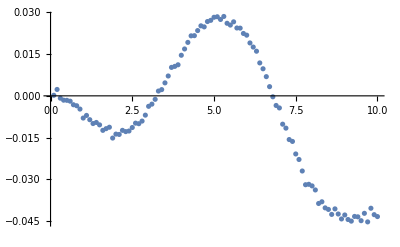

```mathematica
ListPlot[Transpose[{Out[27][[All,1]],Re[Out[27][[All,2,3]]]}]]
```

```mathematica
(*MonteCarlos*)
ParallelTable[{k,v2HZ[k,2.0,1.0,1.0]},{k,0.1,10,0.1}]
```

0.1 starts to run on kern 50

0.3 starts to run on kern 49

0.5 starts to run on kern 48

0.7 starts to run on kern 47

0.9 starts to run on kern 46

1.1 starts to run on kern 45

1.3 starts to run on kern 44

1.5 starts to run on kern 43

1.7 starts to run on kern 42

1.9 starts to run on kern 41

2.1 starts to run on kern 40

2.3 starts to run on kern 39

2.5 starts to run on kern 38

2.7 starts to run on kern 37

2.9 starts to run on kern 36

3.1 starts to run on kern 35

3.3 starts to run on kern 34

3.5 starts to run on kern 33

3.7 starts to run on kern 32

3.9 starts to run on kern 31

4.1 starts to run on kern 30

4.3 starts to run on kern 29

4.5 starts to run on kern 28

4.7 starts to run on kern 27

4.9 starts to run on kern 26

5.1 starts to run on kern 25

5.3 starts to run on kern 24

5.5 starts to run on kern 23

5.7 starts to run on kern 22

5.9 starts to run on kern 21

6.1 starts to run on kern 20

6.3 starts to run on kern 19

6.5 starts to run on kern 18

6.7 starts to run on kern 17

6.9 starts to run on kern 16

7.1 starts to run on kern 15

7.3 starts to run on kern 14

7.5 starts to run on kern 13

7.7 starts to run on kern 12

7.9 starts to run on kern 11

8.1 starts to run on kern 10

8.3 starts to run on kern 9

8.5 starts to run on kern 8

8.7 starts to run on kern 7

8.9 starts to run on kern 6

9.1 starts to run on kern 5

9.3 starts to run on kern 4

9.5 starts to run on kern 3

9.7 starts to run on kern 2

9.9 starts to run on kern 1

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0431093+0. ⅈ and 0.00924806 for the integral and error estimates.

0.3 finishes num on kern 49

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0193767+0. ⅈ and 0.078804 for the integral and error estimates.

0.1 finishes num on kern 50

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0235125+0. ⅈ and 0.00357182 for the integral and error estimates.

0.5 finishes num on kern 48

Main calculation is done on kern 49 with k_T=0.3

0.4 starts to run on kern 49

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.000299+0. ⅈ and 0.0018827 for the integral and error estimates.

0.7 finishes num on kern 47

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00900858+0. ⅈ and 0.00112946 for the integral and error estimates.

0.9 finishes num on kern 46

Main calculation is done on kern 50 with k_T=0.1

0.2 starts to run on kern 50

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0117775+0. ⅈ and 0.000722861 for the integral and error estimates.

1.1 finishes num on kern 45

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00576707+0. ⅈ and 0.000347281 for the integral and error estimates.

1.5 finishes num on kern 43

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00950883+0. ⅈ and 0.000485247 for the integral and error estimates.

1.3 finishes num on kern 44

Main calculation is done on kern 48 with k_T=0.5

0.6 starts to run on kern 48

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00141918+0. ⅈ and 0.000263651 for the integral and error estimates.

1.7 finishes num on kern 42

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00227938+0. ⅈ and 0.000213673 for the integral and error estimates.

1.9 finishes num on kern 41

Main calculation is done on kern 46 with k_T=0.9

1. starts to run on kern 46

Main calculation is done on kern 47 with k_T=0.7

0.8 starts to run on kern 47

Main calculation is done on kern 43 with k_T=1.5

1.6 starts to run on kern 43

Main calculation is done on kern 45 with k_T=1.1

1.2 starts to run on kern 45

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00467258+0. ⅈ and 0.000183415 for the integral and error estimates.

2.1 finishes num on kern 40

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00611573+0. ⅈ and 0.000162942 for the integral and error estimates.

2.3 finishes num on kern 39

Main calculation is done on kern 44 with k_T=1.3

1.4 starts to run on kern 44

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0066764+0. ⅈ and 0.000146113 for the integral and error estimates.

2.5 finishes num on kern 38

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00677421+0. ⅈ and 0.000124004 for the integral and error estimates.

2.9 finishes num on kern 36

Main calculation is done on kern 42 with k_T=1.7

1.8 starts to run on kern 42

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00677917+0. ⅈ and 0.00013411 for the integral and error estimates.

2.7 finishes num on kern 37

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00562827+0. ⅈ and 0.000101105 for the integral and error estimates.

3.3 finishes num on kern 34

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00529031+0. ⅈ and 0.0000894244 for the integral and error estimates.

3.5 finishes num on kern 33

Main calculation is done on kern 41 with k_T=1.9

2. starts to run on kern 41

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00360059+0. ⅈ and 0.0000452072 for the integral and error estimates.

4.3 finishes num on kern 29

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00478779+0. ⅈ and 0.0000764682 for the integral and error estimates.

3.7 finishes num on kern 32

Main calculation is done on kern 40 with k_T=2.1

2.2 starts to run on kern 40

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00438884+0. ⅈ and 0.0000649923 for the integral and error estimates.

3.9 finishes num on kern 31

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00408982+0. ⅈ and 0.0000542761 for the integral and error estimates.

4.1 finishes num on kern 30

Main calculation is done on kern 39 with k_T=2.3

2.4 starts to run on kern 39

Main calculation is done on kern 38 with k_T=2.5

2.6 starts to run on kern 38

Main calculation is done on kern 36 with k_T=2.9

3. starts to run on kern 36

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00613327+0. ⅈ and 0.000112943 for the integral and error estimates.

3.1 finishes num on kern 35

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00310878+0. ⅈ and 0.0000370727 for the integral and error estimates.

4.5 finishes num on kern 28

Main calculation is done on kern 34 with k_T=3.3

3.4 starts to run on kern 34

Main calculation is done on kern 37 with k_T=2.7

2.8 starts to run on kern 37

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00272962+0. ⅈ and 0.0000306659 for the integral and error estimates.

4.7 finishes num on kern 27

Main calculation is done on kern 33 with k_T=3.5

3.6 starts to run on kern 33

Main calculation is done on kern 32 with k_T=3.7

3.8 starts to run on kern 32

Main calculation is done on kern 31 with k_T=3.9

4. starts to run on kern 31

Main calculation is done on kern 29 with k_T=4.3

4.4 starts to run on kern 29

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0022792+0. ⅈ and 0.0000253133 for the integral and error estimates.

4.9 finishes num on kern 26

Main calculation is done on kern 30 with k_T=4.1

4.2 starts to run on kern 30

Main calculation is done on kern 35 with k_T=3.1

3.2 starts to run on kern 35

Main calculation is done on kern 28 with k_T=4.5

4.6 starts to run on kern 28

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00195081+0. ⅈ and 0.0000212451 for the integral and error estimates.

5.1 finishes num on kern 25

Main calculation is done on kern 27 with k_T=4.7

4.8 starts to run on kern 27

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00160444+0. ⅈ and 0.0000176353 for the integral and error estimates.

5.3 finishes num on kern 24

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00124983+0. ⅈ and 0.000014616 for the integral and error estimates.

5.5 finishes num on kern 23

Main calculation is done on kern 26 with k_T=4.9

5. starts to run on kern 26

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00101569+0. ⅈ and 0.0000123433 for the integral and error estimates.

5.7 finishes num on kern 22

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000792464+0. ⅈ and 0.0000102887 for the integral and error estimates.

5.9 finishes num on kern 21

Main calculation is done on kern 25 with k_T=5.1

5.2 starts to run on kern 25

Main calculation is done on kern 24 with k_T=5.3

5.4 starts to run on kern 24

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000626204+0. ⅈ and 8.75173×10^-6 for the integral and error estimates.

6.1 finishes num on kern 20

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000494134+0. ⅈ and 7.39732×10^-6 for the integral and error estimates.

6.3 finishes num on kern 19

Main calculation is done on kern 23 with k_T=5.5

5.6 starts to run on kern 23

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00038393+0. ⅈ and 6.24711×10^-6 for the integral and error estimates.

6.5 finishes num on kern 18

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0410288+0. ⅈ and 0.00541526 for the integral and error estimates.

0.4 finishes num on kern 49

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0497596+0. ⅈ and 0.020264 for the integral and error estimates.

0.2 finishes num on kern 50

Main calculation is done on kern 22 with k_T=5.7

5.8 starts to run on kern 22

Main calculation is done on kern 49 with k_T=0.4

Main calculation is done on kern 50 with k_T=0.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000319027+0. ⅈ and 5.36049×10^-6 for the integral and error estimates.

6.7 finishes num on kern 17

Main calculation is done on kern 21 with k_T=5.9

6. starts to run on kern 21

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00801521+0. ⅈ and 0.0025292 for the integral and error estimates.

0.6 finishes num on kern 48

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0111496+0. ⅈ and 0.00089874 for the integral and error estimates.

1. finishes num on kern 46

Main calculation is done on kern 20 with k_T=6.1

6.2 starts to run on kern 20

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00647569+0. ⅈ and 0.00145481 for the integral and error estimates.

0.8 finishes num on kern 47

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000252039+0. ⅈ and 4.58672×10^-6 for the integral and error estimates.

6.9 finishes num on kern 16

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.0111754+0. ⅈ and 0.000588213 for the integral and error estimates.

1.2 finishes num on kern 45

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00339214+0. ⅈ and 0.000299641 for the integral and error estimates.

1.6 finishes num on kern 43

Main calculation is done on kern 48 with k_T=0.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained 0.00804437+0. ⅈ and 0.000408482 for the integral and error estimates.

1.4 finishes num on kern 44

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000195766+0. ⅈ and 3.9251×10^-6 for the integral and error estimates.

7.1 finishes num on kern 15

Main calculation is done on kern 46 with k_T=1.

Main calculation is done on kern 45 with k_T=1.2

Main calculation is done on kern 43 with k_T=1.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000151811+0. ⅈ and 3.34022×10^-6 for the integral and error estimates.

7.3 finishes num on kern 14

Main calculation is done on kern 47 with k_T=0.8

Main calculation is done on kern 19 with k_T=6.3

6.4 starts to run on kern 19

Main calculation is done on kern 44 with k_T=1.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000266956+0. ⅈ and 0.000236254 for the integral and error estimates.

1.8 finishes num on kern 42

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000120864+0. ⅈ and 2.94041×10^-6 for the integral and error estimates.

7.5 finishes num on kern 13

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00349355+0. ⅈ and 0.000196076 for the integral and error estimates.

2. finishes num on kern 41

Main calculation is done on kern 18 with k_T=6.5

6.6 starts to run on kern 18

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00528632+0. ⅈ and 0.000171523 for the integral and error estimates.

2.2 finishes num on kern 40

Main calculation is done on kern 42 with k_T=1.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00010054+0. ⅈ and 2.59958×10^-6 for the integral and error estimates.

7.7 finishes num on kern 12

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00646178+0. ⅈ and 0.000153812 for the integral and error estimates.

2.4 finishes num on kern 39

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00685461+0. ⅈ and 0.000139819 for the integral and error estimates.

2.6 finishes num on kern 38

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00643624+0. ⅈ and 0.000118645 for the integral and error estimates.

3. finishes num on kern 36

Main calculation is done on kern 41 with k_T=2.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00703449+0. ⅈ and 0.000129909 for the integral and error estimates.

2.8 finishes num on kern 37

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00538396+0. ⅈ and 0.0000950801 for the integral and error estimates.

3.4 finishes num on kern 34

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000603078+0. ⅈ and 2.06505×10^-6 for the integral and error estimates.

8.1 finishes num on kern 10

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000482643+0. ⅈ and 1.91242×10^-6 for the integral and error estimates.

Main calculation is done on kern 40 with k_T=2.2

8.3 finishes num on kern 9

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00515279+0. ⅈ and 0.0000833286 for the integral and error estimates.

3.6 finishes num on kern 33

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000748166+0. ⅈ and 2.30324×10^-6 for the integral and error estimates.

7.9 finishes num on kern 11

Main calculation is done on kern 17 with k_T=6.7

6.8 starts to run on kern 17

Main calculation is done on kern 39 with k_T=2.4

Main calculation is done on kern 38 with k_T=2.6

Main calculation is done on kern 36 with k_T=3.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00457221+0. ⅈ and 0.0000705717 for the integral and error estimates.

3.8 finishes num on kern 32

Main calculation is done on kern 37 with k_T=2.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00329948+0. ⅈ and 0.0000406293 for the integral and error estimates.

4.4 finishes num on kern 29

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000259608+0. ⅈ and 1.60148×10^-6 for the integral and error estimates.

8.7 finishes num on kern 7

Main calculation is done on kern 34 with k_T=3.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000177499+0. ⅈ and 1.50391×10^-6 for the integral and error estimates.

8.9 finishes num on kern 6

Main calculation is done on kern 16 with k_T=6.9

7. starts to run on kern 16

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00418582+0. ⅈ and 0.000059274 for the integral and error estimates.

4. finishes num on kern 31

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000350907+0. ⅈ and 1.72898×10^-6 for the integral and error estimates.

8.5 finishes num on kern 8

Main calculation is done on kern 33 with k_T=3.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -5.03638×10^-6+0. ⅈ and 1.26443×10^-6 for the integral and error estimates.

9.5 finishes num on kern 3

Main calculation is done on kern 15 with k_T=7.1

7.2 starts to run on kern 15

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0038097+0. ⅈ and 0.0000496876 for the integral and error estimates.

4.2 finishes num on kern 30

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00602672+0. ⅈ and 0.000107732 for the integral and error estimates.

3.2 finishes num on kern 35

Main calculation is done on kern 32 with k_T=3.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000125351+0. ⅈ and 1.39468×10^-6 for the integral and error estimates.

9.1 finishes num on kern 5

Main calculation is done on kern 14 with k_T=7.3

7.4 starts to run on kern 14

Main calculation is done on kern 13 with k_T=7.5

7.6 starts to run on kern 13

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -3.90246×10^-6+0. ⅈ and 1.17835×10^-6 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -7.71072×10^-6+0. ⅈ and 1.33238×10^-6 for the integral and error estimates.

9.7 finishes num on kern 2

9.3 finishes num on kern 4

Main calculation is done on kern 31 with k_T=4.

Main calculation is done on kern 29 with k_T=4.4

Main calculation is done on kern 12 with k_T=7.7

7.8 starts to run on kern 12

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -1.61757×10^-6+0. ⅈ and 1.07989×10^-6 for the integral and error estimates.

9.9 finishes num on kern 1

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00292999+0. ⅈ and 0.0000339532 for the integral and error estimates.

4.6 finishes num on kern 28

Main calculation is done on kern 35 with k_T=3.2

Main calculation is done on kern 30 with k_T=4.2

Main calculation is done on kern 9 with k_T=8.3

8.4 starts to run on kern 9

Main calculation is done on kern 10 with k_T=8.1

8.2 starts to run on kern 10

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00246892+0. ⅈ and 0.0000278418 for the integral and error estimates.

4.8 finishes num on kern 27

Main calculation is done on kern 7 with k_T=8.7

8.8 starts to run on kern 7

Main calculation is done on kern 11 with k_T=7.9

8. starts to run on kern 11

Main calculation is done on kern 6 with k_T=8.9

9. starts to run on kern 6

Main calculation is done on kern 8 with k_T=8.5

8.6 starts to run on kern 8

Main calculation is done on kern 3 with k_T=9.5

9.6 starts to run on kern 3

Main calculation is done on kern 28 with k_T=4.6

Main calculation is done on kern 5 with k_T=9.1

9.2 starts to run on kern 5

Main calculation is done on kern 4 with k_T=9.3

9.4 starts to run on kern 4

Main calculation is done on kern 2 with k_T=9.7

9.8 starts to run on kern 2

Main calculation is done on kern 1 with k_T=9.9

10. starts to run on kern 1

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00210434+0. ⅈ and 0.0000230316 for the integral and error estimates.

5. finishes num on kern 26

Main calculation is done on kern 27 with k_T=4.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00172721+0. ⅈ and 0.0000191955 for the integral and error estimates.

5.2 finishes num on kern 25

Main calculation is done on kern 26 with k_T=5.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00139337+0. ⅈ and 0.0000159813 for the integral and error estimates.

5.4 finishes num on kern 24

Main calculation is done on kern 25 with k_T=5.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.00113878+0. ⅈ and 0.0000133991 for the integral and error estimates.

5.6 finishes num on kern 23

Main calculation is done on kern 24 with k_T=5.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000903523+0. ⅈ and 0.0000113264 for the integral and error estimates.

5.8 finishes num on kern 22

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000697745+0. ⅈ and 9.43764×10^-6 for the integral and error estimates.

6. finishes num on kern 21

Main calculation is done on kern 23 with k_T=5.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000545531+0. ⅈ and 7.9887×10^-6 for the integral and error estimates.

6.2 finishes num on kern 20

Main calculation is done on kern 22 with k_T=5.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000435128+0. ⅈ and 6.78757×10^-6 for the integral and error estimates.

6.4 finishes num on kern 19

Main calculation is done on kern 21 with k_T=6.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000343224+0. ⅈ and 5.75236×10^-6 for the integral and error estimates.

6.6 finishes num on kern 18

Main calculation is done on kern 20 with k_T=6.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000276704+0. ⅈ and 4.93152×10^-6 for the integral and error estimates.

6.8 finishes num on kern 17

Main calculation is done on kern 19 with k_T=6.4

Main calculation is done on kern 18 with k_T=6.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000217532+0. ⅈ and 4.2111×10^-6 for the integral and error estimates.

7. finishes num on kern 16

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000175794+0. ⅈ and 3.66371×10^-6 for the integral and error estimates.

7.2 finishes num on kern 15

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000139146+0. ⅈ and 3.17008×10^-6 for the integral and error estimates.

7.4 finishes num on kern 14

Main calculation is done on kern 17 with k_T=6.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000108399+0. ⅈ and 2.74329×10^-6 for the integral and error estimates.

7.6 finishes num on kern 13

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000916455+0. ⅈ and 2.45824×10^-6 for the integral and error estimates.

7.8 finishes num on kern 12

Main calculation is done on kern 16 with k_T=7.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.000054667+0. ⅈ and 1.97577×10^-6 for the integral and error estimates.

8.2 finishes num on kern 10

Main calculation is done on kern 15 with k_T=7.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000420314+0. ⅈ and 1.80706×10^-6 for the integral and error estimates.

8.4 finishes num on kern 9

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000710551+0. ⅈ and 2.18517×10^-6 for the integral and error estimates.

8. finishes num on kern 11

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000199399+0. ⅈ and 1.53133×10^-6 for the integral and error estimates.

8.8 finishes num on kern 7

Main calculation is done on kern 14 with k_T=7.4

Main calculation is done on kern 13 with k_T=7.6

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000304911+0. ⅈ and 1.65412×10^-6 for the integral and error estimates.

8.6 finishes num on kern 8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -0.0000133854+0. ⅈ and 1.44792×10^-6 for the integral and error estimates.

9. finishes num on kern 6

Main calculation is done on kern 12 with k_T=7.8

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -9.57391×10^-6+0. ⅈ and 1.37835×10^-6 for the integral and error estimates.

9.2 finishes num on kern 5

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -5.48769×10^-6+0. ⅈ and 1.2093×10^-6 for the integral and error estimates.

9.6 finishes num on kern 3

Main calculation is done on kern 10 with k_T=8.2

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -2.70446×10^-6+0. ⅈ and 1.13914×10^-6 for the integral and error estimates.

9.8 finishes num on kern 2

Main calculation is done on kern 9 with k_T=8.4

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -6.00608×10^-6+0. ⅈ and 1.29892×10^-6 for the integral and error estimates.

9.4 finishes num on kern 4

Main calculation is done on kern 7 with k_T=8.8

Main calculation is done on kern 11 with k_T=8.

NIntegrate::maxp: The integral failed to converge after 50100 integrand evaluations. NIntegrate obtained -4.45558×10^-6+0. ⅈ and 1.04752×10^-6 for the integral and error estimates.

10. finishes num on kern 1

Main calculation is done on kern 8 with k_T=8.6

Main calculation is done on kern 6 with k_T=9.

Main calculation is done on kern 5 with k_T=9.2

Main calculation is done on kern 3 with k_T=9.6

Main calculation is done on kern 2 with k_T=9.8

Main calculation is done on kern 4 with k_T=9.4

Main calculation is done on kern 1 with k_T=10.

{{0.1,{0.0193767,19.7853,0.000979347}},{0.2,{-0.0497596+0. ⅈ,5.14103,-0.00967893+0. ⅈ}},{0.3,{-0.0431093+0. ⅈ,2.37059,-0.018185+0. ⅈ}},{0.4,{-0.0410288+0. ⅈ,1.40039,-0.0292981+0. ⅈ}},{0.5,{-0.0235125+0. ⅈ,0.923367,-0.0254638+0. ⅈ}},{0.6,{-0.00801521+0. ⅈ,0.64749,-0.0123789+0. ⅈ}},{0.7,{0.000299,0.500544,0.00059735}},{0.8,{0.00647569,0.38877,0.0166569}},{0.9,{0.00900858,0.298778,0.0301515}},{1.,{0.0111496,0.244728,0.045559}},{1.1,{0.0117775,0.198251,0.0594068}},{1.2,{0.0111754,0.155247,0.0719843}},{1.3,{0.00950883,0.129997,0.0731467}},{1.4,{0.00804437,0.109293,0.0736035}},{1.5,{0.00576707,0.0919185,0.0627411}},{1.6,{0.00339214,0.080468,0.0421552}},{1.7,{0.00141918,0.0694774,0.0204264}},{1.8,{-0.000266956+0. ⅈ,0.0634968,-0.00420424+0. ⅈ}},{1.9,{-0.00227938+0. ⅈ,0.0569149,-0.0400489+0. ⅈ}},{2.,{-0.00349355+0. ⅈ,0.0534443,-0.0653681+0. ⅈ}},{2.1,{-0.00467258+0. ⅈ,0.0510484,-0.0915323+0. ⅈ}},{2.2,{-0.00528632+0. ⅈ,0.0466081,-0.113421+0. ⅈ}},{2.3,{-0.00611573+0. ⅈ,0.0447654,-0.136617+0. ⅈ}},{2.4,{-0.00646178+0. ⅈ,0.0421233,-0.153402+0. ⅈ}},{2.5,{-0.0066764+0. ⅈ,0.0397446,-0.167983+0. ⅈ}},{2.6,{-0.00685461+0. ⅈ,0.0384855,-0.178109+0. ⅈ}},{2.7,{-0.00677917+0. ⅈ,0.0372226,-0.182125+0. ⅈ}},{2.8,{-0.00703449+0. ⅈ,0.0351532,-0.200109+0. ⅈ}},{2.9,{-0.00677421+0. ⅈ,0.0345175,-0.196254+0. ⅈ}},{3.,{-0.00643624+0. ⅈ,0.0323013,-0.199256+0. ⅈ}},{3.1,{-0.00613327+0. ⅈ,0.030558,-0.200709+0. ⅈ}},{3.2,{-0.00602672+0. ⅈ,0.0282545,-0.213301+0. ⅈ}},{3.3,{-0.00562827+0. ⅈ,0.0268886,-0.209318+0. ⅈ}},{3.4,{-0.00538396+0. ⅈ,0.0252735,-0.213028+0. ⅈ}},{3.5,{-0.00529031+0. ⅈ,0.0233068,-0.226986+0. ⅈ}},{3.6,{-0.00515279+0. ⅈ,0.0212472,-0.242516+0. ⅈ}},{3.7,{-0.00478779+0. ⅈ,0.019655,-0.243592+0. ⅈ}},{3.8,{-0.00457221+0. ⅈ,0.0180796,-0.252894+0. ⅈ}},{3.9,{-0.00438884+0. ⅈ,0.0164961,-0.266053+0. ⅈ}},{4.,{-0.00418582+0. ⅈ,0.0150862,-0.27746+0. ⅈ}},{4.1,{-0.00408982+0. ⅈ,0.0133028,-0.30744+0. ⅈ}},{4.2,{-0.0038097+0. ⅈ,0.0118653,-0.321078+0. ⅈ}},{4.3,{-0.00360059+0. ⅈ,0.0108249,-0.332622+0. ⅈ}},{4.4,{-0.00329948+0. ⅈ,0.00962919,-0.342654+0. ⅈ}},{4.5,{-0.00310878+0. ⅈ,0.00872964,-0.356118+0. ⅈ}},{4.6,{-0.00292999+0. ⅈ,0.00772015,-0.379525+0. ⅈ}},{4.7,{-0.00272962+0. ⅈ,0.00686939,-0.39736+0. ⅈ}},{4.8,{-0.00246892+0. ⅈ,0.00619371,-0.398618+0. ⅈ}},{4.9,{-0.0022792+0. ⅈ,0.00544686,-0.418442+0. ⅈ}},{5.,{-0.00210434+0. ⅈ,0.00496618,-0.423735+0. ⅈ}},{5.1,{-0.00195081+0. ⅈ,0.00438435,-0.444949+0. ⅈ}},{5.2,{-0.00172721+0. ⅈ,0.00391699,-0.440955+0. ⅈ}},{5.3,{-0.00160444+0. ⅈ,0.00358047,-0.448108+0. ⅈ}},{5.4,{-0.00139337+0. ⅈ,0.00318278,-0.437784+0. ⅈ}},{5.5,{-0.00124983+0. ⅈ,0.00287868,-0.434169+0. ⅈ}},{5.6,{-0.00113878+0. ⅈ,0.00262818,-0.433295+0. ⅈ}},{5.7,{-0.00101569+0. ⅈ,0.00236615,-0.429259+0. ⅈ}},{5.8,{-0.000903523+0. ⅈ,0.00218552,-0.413413+0. ⅈ}},{5.9,{-0.000792464+0. ⅈ,0.00197737,-0.400766+0. ⅈ}},{6.,{-0.000697745+0. ⅈ,0.00178901,-0.390017+0. ⅈ}},{6.1,{-0.000626204+0. ⅈ,0.00165465,-0.378451+0. ⅈ}},{6.2,{-0.000545531+0. ⅈ,0.00153488,-0.355424+0. ⅈ}},{6.3,{-0.000494134+0. ⅈ,0.00141367,-0.349541+0. ⅈ}},{6.4,{-0.000435128+0. ⅈ,0.00130805,-0.332654+0. ⅈ}},{6.5,{-0.00038393+0. ⅈ,0.00119979,-0.319998+0. ⅈ}},{6.6,{-0.000343224+0. ⅈ,0.00110226,-0.311381+0. ⅈ}},{6.7,{-0.000319027+0. ⅈ,0.00102759,-0.31046+0. ⅈ}},{6.8,{-0.000276704+0. ⅈ,0.000939111,-0.294645+0. ⅈ}},{6.9,{-0.000252039+0. ⅈ,0.000876916,-0.287416+0. ⅈ}},{7.,{-0.000217532+0. ⅈ,0.00080563,-0.270015+0. ⅈ}},{7.1,{-0.000195766+0. ⅈ,0.000771814,-0.253645+0. ⅈ}},{7.2,{-0.000175794+0. ⅈ,0.000721795,-0.243551+0. ⅈ}},{7.3,{-0.000151811+0. ⅈ,0.000685101,-0.221589+0. ⅈ}},{7.4,{-0.000139146+0. ⅈ,0.000638215,-0.218024+0. ⅈ}},{7.5,{-0.000120864+0. ⅈ,0.000610169,-0.198082+0. ⅈ}},{7.6,{-0.000108399+0. ⅈ,0.000568835,-0.190563+0. ⅈ}},{7.7,{-0.00010054+0. ⅈ,0.000539549,-0.186341+0. ⅈ}},{7.8,{-0.0000916455+0. ⅈ,0.000511264,-0.179253+0. ⅈ}},{7.9,{-0.0000748166+0. ⅈ,0.000503684,-0.148539+0. ⅈ}},{8.,{-0.0000710551+0. ⅈ,0.000478847,-0.148388+0. ⅈ}},{8.1,{-0.0000603078+0. ⅈ,0.000461368,-0.130715+0. ⅈ}},{8.2,{-0.000054667+0. ⅈ,0.000444492,-0.122987+0. ⅈ}},{8.3,{-0.0000482643+0. ⅈ,0.000434681,-0.111034+0. ⅈ}},{8.4,{-0.0000420314+0. ⅈ,0.000418533,-0.100426+0. ⅈ}},{8.5,{-0.0000350907+0. ⅈ,0.000399547,-0.0878264+0. ⅈ}},{8.6,{-0.0000304911+0. ⅈ,0.000395828,-0.0770312+0. ⅈ}},{8.7,{-0.0000259608+0. ⅈ,0.000380089,-0.0683018+0. ⅈ}},{8.8,{-0.0000199399+0. ⅈ,0.000370739,-0.0537842+0. ⅈ}},{8.9,{-0.0000177499+0. ⅈ,0.00035906,-0.0494343+0. ⅈ}},{9.,{-0.0000133854+0. ⅈ,0.000353006,-0.0379185+0. ⅈ}},{9.1,{-0.0000125351+0. ⅈ,0.000346034,-0.036225+0. ⅈ}},{9.2,{-9.57391×10^-6+0. ⅈ,0.00033376,-0.028685+0. ⅈ}},{9.3,{-7.71072×10^-6+0. ⅈ,0.000320118,-0.0240871+0. ⅈ}},{9.4,{-6.00608×10^-6+0. ⅈ,0.000314145,-0.0191188+0. ⅈ}},{9.5,{-5.03638×10^-6+0. ⅈ,0.000300881,-0.0167388+0. ⅈ}},{9.6,{-5.48769×10^-6+0. ⅈ,0.000297138,-0.0184685+0. ⅈ}},{9.7,{-3.90246×10^-6+0. ⅈ,0.000285891,-0.0136502+0. ⅈ}},{9.8,{-2.70446×10^-6+0. ⅈ,0.000273171,-0.00990024+0. ⅈ}},{9.9,{-1.61757×10^-6+0. ⅈ,0.000268954,-0.00601431+0. ⅈ}},{10.,{-4.45558×10^-6+0. ⅈ,0.000251404,-0.0177228+0. ⅈ}}}

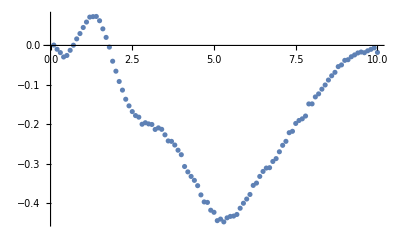

```mathematica
ListPlot[Transpose[{%[[All,1]],Re[%[[All,2,3]]]}]]
```

```mathematica
Getv2kT[b_,rA_,rB_]:=Module[{v2kTb05,i,kT,x1u,x3u,bu,ti},
ti=AbsoluteTime[];
v2kTb05=ParallelTable[{kT,v2HZ[kT,b,rA,rB]},{kT,0.2,10,0.2}];
Print[ListPlot[{Transpose[{v2kTb05[[All,1]],Re[v2kTb05[[All,2,3]]]}]},PlotStyle->{Red,Blue}]];
Print["Computatino time: ", AbsoluteTime[]-ti];
v2kTb05
]
```

```mathematica
LaunchKernels[50];
$KernelCount
```

50

```mathematica
(*CloseKernels[]*)
```

```mathematica
Getv2kT[2.0,1.0,1.0]
```

0.2 starts to run on kern 189

0.4 starts to run on kern 188

0.6 starts to run on kern 187

0.8 starts to run on kern 186

1. starts to run on kern 185

1.2 starts to run on kern 184

1.4 starts to run on kern 183

1.6 starts to run on kern 182

1.8 starts to run on kern 181

2. starts to run on kern 180

2.2 starts to run on kern 179

2.4 starts to run on kern 178

2.6 starts to run on kern 177

2.8 starts to run on kern 176

3. starts to run on kern 175

3.2 starts to run on kern 174

3.4 starts to run on kern 173

3.6 starts to run on kern 172

3.8 starts to run on kern 171

4. starts to run on kern 170

4.2 starts to run on kern 169

4.4 starts to run on kern 168

4.6 starts to run on kern 167

4.8 starts to run on kern 166

5. starts to run on kern 165

5.2 starts to run on kern 164

5.4 starts to run on kern 163

5.6 starts to run on kern 162

5.8 starts to run on kern 161

6. starts to run on kern 160

6.2 starts to run on kern 159

6.4 starts to run on kern 158

6.6 starts to run on kern 157

6.8 starts to run on kern 156

7. starts to run on kern 155

7.2 starts to run on kern 154

7.4 starts to run on kern 153

7.6 starts to run on kern 152

7.8 starts to run on kern 151

8. starts to run on kern 150

8.2 starts to run on kern 149

8.4 starts to run on kern 148

8.6 starts to run on kern 147

8.8 starts to run on kern 146

9. starts to run on kern 145

9.2 starts to run on kern 144

9.4 starts to run on kern 143

9.6 starts to run on kern 142

9.8 starts to run on kern 141

10. starts to run on kern 140